## Common elements

```mathematica
(* Load HEPMath package *)
Needs["HEPMath`"]
normKinVars={s-> sp+q2,s4-> sp+t1+u1,t-> t1+m2,u1p->u1-q2};
physAssump={m2>0,q2<0,s>0,sp>0,t1<0,u1<0,sp+t1+u1>0,s4>0,
s-s4-2m2>0,sp+t1>0,(s-s4)^2-4m2 s>0,(sp+u1p)^2-4q2 t>0,
(q2*s4-s*u1)>0,((q2*s4+4*m2*(q2-s-t1)-s*u1)>0)
}/.normKinVars;

physParameterPoints={
{q2->-5,u1->-25,t1->-15,sp->115,m2->0.5},
{q2->-5,u1->-25,t1->-15,sp->115,m2->1.0},
{q2->-6,u1->-25,t1->-15,sp->115,m2->0.5},
{q2->-5,u1->-25,t1->-15,sp->120,m2->0.5}
};
Do[Module[{l,v},l=physAssump/.p;v=And@@l;If[Not[v],Print[p, " doesn't match assumptions: ",l]]],{p,physParameterPoints}]

(* total cross section parameters *)
ηOfs[s_]=s/(4m2)-1;
sOfη[η_]=(1+η)*(4m2);
ρOfs[s_]=4m2/s;
sOfρ[ρ_]=4m2/ρ;
βOfρ[ρ_]=Sqrt[1-ρ];
ρOfβ[β_]=1-β^2;
χOfβ[β_]=(1-β)/(1+β);
normTotalCSVars={ρ-> ρOfs[s],β-> βOfρ@ρOfs[s],η-> ηOfs[s],χ->χOfβ@βOfρ@ρOfs[s]};
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-ρq],ρq-> 4m2/q2};

(* color factors *)
normColor={Kgγ-> 1/(NC^2-1),Kqγ-> 1/NC,CA->NC,CF-> (NC^2-1)/(2NC),NC-> 3};
normColor=(First@#-> (Last@#/.normColor))&/@normColor;

(* tools *)
getLinearCoefficientList[e_,logs_]:=Module[{ar,pos0,pos1,allPos},
ar=CoefficientList[e,logs];
pos0=Table[1,{Length@logs}];
pos1=pos0;
pos1[[1]]=2;
allPos=Join[{pos0},Table[RotateRight[pos1,n-1],{n,Length@logs}]];
Table[Part@@Flatten[{{ar},p},1],{p,allPos}]
];
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

## Matrix elements

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Born.m";
```

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Soft.m";
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Virt.m";
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Hard.m";
```

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Real.m";
(* TODO: track down *)
{CoeffAG1,CoeffAL1,CoeffAP1k0,CoeffAP1k2,
CoeffAG2,CoeffAL2,CoeffAP2,
CoeffAG3,CoeffAL3,CoeffAP3}={CoeffAG1,CoeffAL1,CoeffAP1k0,CoeffAP1k2,
CoeffAG2,CoeffAL2,CoeffAP2,
CoeffAG3,CoeffAL3,CoeffAP3}/2;
```

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.SV.m";
<<"~/Physik/PhD/MMa/data/ElProduction.Hard.m";
```

## Born γ*+g → Q+Qbar

### Total cross sections

```mathematica
Module[{a,bϵ,Sϵ,Eϵ,nLaenen,nMe},
Sϵ=(4π)^(-2-ϵ/2);
a[G]=1;
a[L]=2(1+ϵ/2);
a[P]=2(1+ϵ/2);

Eϵ[G]=1/(1+ϵ/2);
Eϵ[L]=1/(1+ϵ/2);
Eϵ[P]=1;

Print["Laenen:"];
nLaenen[k_]:=32α αS eH^2 Kgγ NC CF Eϵ[k] 1/(1+ϵ/2) π^3 Sϵ/Gamma[1+ϵ/2] a[k];
Do[
Print@FullSimplify@Series[nLaenen[proj],{ϵ,0,1}];
,{proj,{G,L,P}}];

bϵ[G]=1/(2(1+ϵ/2));
bϵ[L]=1;
bϵ[P]=1;

Print["Me:"];
nMe[k_]:=1/2 α αS eH^2 Kgγ NC CF Eϵ[k]*2bϵ[k]*π^3/Gamma[1+ϵ/2]Sϵ*2^6;
Do[
Print@FullSimplify@Series[nMe[proj],{ϵ,0,1}];
,{proj,{G,L,P}}];
]
```

Laenen:

2 CF eH^2 Kgγ NC π α αS+CF eH^2 Kgγ NC π α αS (-2+EulerGamma-Log[4 π]) ϵ+O[ϵ]^2

4 CF eH^2 Kgγ NC π α αS+2 CF eH^2 Kgγ NC π α αS (-1+EulerGamma-Log[4 π]) ϵ+O[ϵ]^2

4 CF eH^2 Kgγ NC π α αS+2 CF eH^2 Kgγ NC π α αS (EulerGamma-Log[4 π]) ϵ+O[ϵ]^2

Me:

2 CF eH^2 Kgγ NC π α αS+CF eH^2 Kgγ NC π α αS (-2+EulerGamma-Log[4 π]) ϵ+O[ϵ]^2

4 CF eH^2 Kgγ NC π α αS+2 CF eH^2 Kgγ NC π α αS (-1+EulerGamma-Log[4 π]) ϵ+O[ϵ]^2

4 CF eH^2 Kgγ NC π α αS+2 CF eH^2 Kgγ NC π α αS (EulerGamma-Log[4 π]) ϵ+O[ϵ]^2

```mathematica
Module[{f,int},
f[t1_]=Integrate[Limit[BQED[G]/.{Dim->4+ϵ,u1-> -t1 - sp},ϵ-> 0],t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]]/.{ (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])-> 2Log[χ]};
σGg=FullSimplify[2π*int/sp^2/.{β^2-> 1-4m2/(sp+q2)}]
]
Module[{f,int},
f[t1_]=Integrate[BQED[L]/.{u1-> -t1 - sp},t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]]/.{ (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])-> 2Log[χ]};
σLg=4π*int/sp^2
]
σTg=σGg+1/2σLg;
Module[{f,int},
f[t1_]=Integrate[Limit[BQED[P]/.{Dim->4+ϵ,u1-> -t1 - sp},ϵ-> 0],t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]]/.{ (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])-> 2Log[χ],-1+β^2-> -4m2/(sp+q2)};
σPg=Simplify[4π*int/sp^2]
]
```

-(4 π ((2 q2^2+2 q2 sp+sp^2+4 m2 (q2+sp)) β+(-8 m2^2+2 q2^2+4 m2 sp+2 q2 sp+sp^2) Log[χ]))/sp^3

-(16 π q2 ((q2+sp) β+2 m2 Log[χ]))/sp^3

(4 π ((4 q2+3 sp) β+(2 q2+sp) Log[χ]))/sp^2

```mathematica
FullSimplify[(-4π/sp^3((s^2+q2^2+4m2 s)β+((s)^2+q2^2-4m2(2m2-sp)) Log[χ])-σGg)/.normKinVars]
```

0

```mathematica
FullSimplify@Series[σGg/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,3}]
FullSimplify@Series[σLg/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,5}]
FullSimplify@Series[σTg/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,5}]
FullSimplify@Series[σPg/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,3}]
```

-(4 π β)/(-4 m2+q2)+(8 π (2 m2+q2) (12 m2+q2) β^3)/(3 (4 m2-q2)^3)+O[β]^4

-(128 (m2 π q2) β^3)/(3 (4 m2-q2)^3)+(256 m2 π q2 (6 m2+q2) β^5)/(5 (-4 m2+q2)^4)+O[β]^6

-(4 π β)/(-4 m2+q2)+(8 π (24 m2^2+6 m2 q2+q2^2) β^3)/(3 (4 m2-q2)^3)-(8 (π (384 m2^3+104 m2^2 q2+26 m2 q2^2+q2^3)) β^5)/(5 (-4 m2+q2)^4)+O[β]^6

-(4 π β)/(-4 m2+q2)-(8 (π (10 m2+q2)) β^3)/(3 (-4 m2+q2)^2)+O[β]^4

```mathematica
FullSimplify@Series[q2/sp^3/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,5}]
FullSimplify@Series[s β/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,5}]
FullSimplify@Series[2m2 Log[χ]/.{χ-> (1-β)/(1+β)}//.{sp-> s-q2,s-> 4m2/(1-β^2)},{β,0,5}]
4-4/3
```

q2/(4 m2-q2)^3-(12 (m2 q2) β^2)/(-4 m2+q2)^4+(12 m2 q2 (4 m2+q2) β^4)/(4 m2-q2)^5+O[β]^6

4 m2 β+4 m2 β^3+4 m2 β^5+O[β]^6

-4 m2 β-(4 m2 β^3)/3-(4 m2 β^5)/5+O[β]^6

8/3

```mathematica
FullSimplify[D[σGg//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/(sp+q2)]},m2]]//.{Sqrt[1-4m2/(sp+q2)]-> β,1/Sqrt[1-4m2/(sp+q2)]-> 1/β,(1-β)/(1+β)-> χ} //FullSimplify
FullSimplify[D[σLg//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/(sp+q2)]},m2]]//.{Sqrt[1-4m2/(sp+q2)]-> β,(1-β)/(1+β)-> χ}
```

-(4 π (-32 m2^2 (q2+sp)+2 m2 sp (4 q2+3 sp)+(q2+sp) (2 q2^2+2 q2 sp+sp^2)+4 m2 (-4 m2+sp) (q2+sp) β Log[χ]))/(m2 sp^3 (q2+sp) β)

-(32 π q2 Log[χ])/sp^3

```mathematica
Series[1/(1-4/3 x +x^2(1.0414 nl - 14.3323)),{x,0,2}]
```

1+(4 x)/3+(16.1101-1.0414 nl) x^2+O[x]^3

#### Check to Nucl.Phys.B 392-162

```mathematica
Module[{σLgref,σTref},
σLgref=16π(-q2 s)/sp^3 (β + 2m2/s Log[χ]);
σTref=4π/sp^3(-((s+q2)^2 + 4m2 s)β-(s^2+q2^2 + 4m2 s -8m2^2)Log[χ]);
Print@FullSimplify[(σLgref-σLg)/.normTotalCSVars/.normKinVars,Assumptions-> {m2>0,0≤ 4m2/(sp+q2)≤ 1}];
Print@FullSimplify[(σTref-σTg)/.normTotalCSVars/.normKinVars,Assumptions-> {m2>0,0≤ 4m2/(sp+q2)≤ 1}];
]
```

0

0

```mathematica
Kgγ * NC *CF/.normColor
```

1/2

#### plots

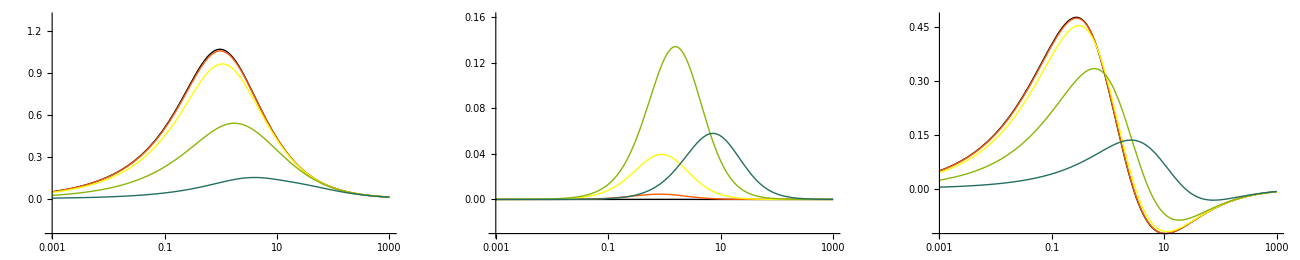

```mathematica
Module[{c0g},
c0g[var_][sV_,Q2V_,m2V_]:=Module[{sig,psNorm},
sig[T]=σTg;
sig[L]=σLg;
sig[P]=σPg;
psNorm[T]=psNorm[L]=psNorm[P]=Kgγ*NC*CF/.normColor;
(psNorm[var]*m2*(sig[var]/.normTotalCSVars/.normKinVars))//.{sp-> sV+Q2V,q2->-Q2V,m2-> m2V}
];
Show[GraphicsRow[{
LogLinearPlot[Evaluate@Table[c0g[T][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> {Full,{-.25,1.3}},PlotStyle->ColorData[3,"ColorList"]],
LogLinearPlot[Evaluate@Table[c0g[L][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> {Full,{-.03,.16}},PlotStyle->ColorData[3,"ColorList"]],
LogLinearPlot[Evaluate@Table[c0g[P][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

## Common NLO

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
```

```mathematica
Module[{refG,refL,ShiftedBorn},
refG=(-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2));
ShiftedBorn[G]=(BQED[G]/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
Print@FullSimplify[refG-ShiftedBorn[G]/.{ϵ-> 0}];
refL=4q2/sp(sp t1 u1p - m2 sp^2-q2 t1^2)(sp+t1)/(sp t1 u1^2)/.normKinVars;
ShiftedBorn[L]=(BQED[L]/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
Print@FullSimplify[refL-ShiftedBorn[L]/.{ϵ-> 0}];
]
```

0

0

```mathematica
Sqrt[1-β^2]/.{β-> Sqrt[1-ρ]}
```

√ρ

{s-s √(1-β^2),{t1→1/2 (q2-s) √(1-β^2)}}

(s (4 t1^2+sp^2 (-1+β^2)))/(4 sp t1^2)

s-s √ρ

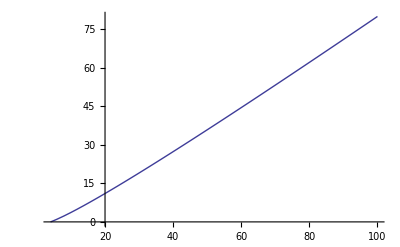

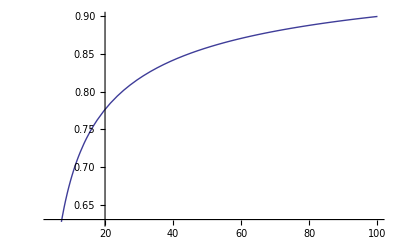

```mathematica
Module[{s4max,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2));
Print@FullSimplify[Maximize[{s4max,t1>-sp/2(1+β),t1<-sp/2(1-β),0<β<1,s>0,q2<0}/.{sp-> s-q2},t1],Assumptions-> {0<β<1,0<ρ<1,q2<0,s>0}];
Print@Simplify@Together@D[s4max,t1];
s4MaxVal=FullSimplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]},0<ρ<1];
Print@FullSimplify[s4MaxVal/.{β-> Sqrt[1-ρ]}];
Print@Plot[s4MaxVal/.normTotalCSVars/.{m2-> 1},{s,4,100}];
Print@Plot[D[s4MaxVal/.normTotalCSVars/.{m2-> 1},s]/.{s-> sv},{sv,4,100}];
]
```

```mathematica
Module[{s4max,Mt1min,Mt1max,m2V,q2V,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
s4MaxVal=s(1-Sqrt[4m2/s]);(*Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;*)
m2V=4.74^2;
q2V=1.;
Print[{-Mt1max,-Mt1min,s4MaxVal}/.{m2-> m2V,q2-> q2V,sp-> s-q2V}/.{s-> 4*m2V(1+10*^2)}];
RegionPlot3D[(sp>4m2 && -Mt1max<t1<-Mt1min && s4 < s4max)//.{m2-> m2V,q2-> q2V,sp-> 4m2(1+Exp[lnη])-q2V},{lnη,-2,2},{t1,-1000,-20},{s4,0,500},AxesLabel->Automatic]
]
```

{-89936.8,-22.473,87116.9}

-Graphics3D-

1/2 sp (√((-4 m2+q2+sp)/(q2+sp)) (q2+sp-2 Δ)+2 m2 Log[(1-√(1-(4 m2)/(q2+sp)))/(1+√(1-(4 m2)/(q2+sp)))])

-1/2 (√(1/m2) (4 m2-q2) Δ) √(s-4 m2)+1/48 (1/m2)^(3/2) (32 m2^2-8 m2 q2-12 m2 Δ-3 q2 Δ) (s-4 m2)^(3/2)+((1/m2)^(5/2) (448 m2^2+48 m2 q2+60 m2 Δ+45 q2 Δ) (s-4 m2)^(5/2))/3840+((1/m2)^(7/2) (-416 m2^2-120 m2 q2-140 m2 Δ-175 q2 Δ) (s-4 m2)^(7/2))/71680+O[s-4 m2]^(9/2)

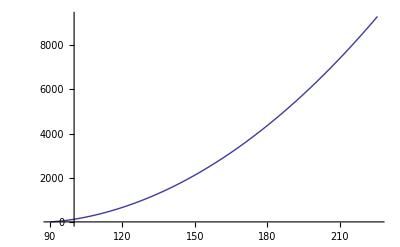

```mathematica
Module[{s4max,Mt1min,Mt1max,A},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
A=Integrate[Integrate[1,{s4,Δ,s4max}],{t1,-Mt1max,-Mt1min},Assumptions-> {0<4m2< q2+sp,sp>0,Δ>0}];
Print[A];
Print@Series[A/.{sp-> s-q2},{s,4m2,4}];
Plot[A//.{m2-> 4.75^2,q2-> 1.,Δ-> 1*^-6},{sp,4.*4.75^2,10*4.75^2}]
]
```

```mathematica
Module[{Sϵ,h2,h2ϵ,h3,diff,Cϵ,ser,ser2},
Sϵ:=(4π)^(-2-ϵ/2);
h2[n_]:=1/(2sp Gamma[(n-2)/2](4π)^((n-2)/2));
h2ϵ=2π Sϵ/(sp Gamma[1+ϵ/2]);
Print@FullSimplify[h2[4+ϵ]/h2ϵ];
h3[n_]:=1/((4π)^(n)Gamma[n-3]sp) s4^(n-3)/(s4+m2)^(n/2-1);
Print@FullSimplify[h3[n]/h2[n]];
Print@Simplify[h3[4+ϵ]/h2[4+ϵ]];
diff=s4^(1+ϵ)/(s4+m2)^(1+ϵ/2)Gamma[1+ϵ/2]/Gamma[1+ϵ]1/(2π(4π)^(2+ϵ/2));
Print@Simplify[h3[4+ϵ]/h2[4+ϵ]/diff];
Print@FullSimplify@Series[h3[4+ϵ]/h2[4+ϵ],{ϵ,0,3}];
Cϵ=1/(16π^2)Exp[ϵ/2(EulerGamma-Log[4π])];
ser = Cϵ/(2π) (1-3/8Zeta[2]ϵ^2)s4^(1+ϵ)/(s4+m2)^(1+ϵ/2);
Print@FullSimplify@Series[h3[4+ϵ]/h2[4+ϵ]-ser,{ϵ,0,4}];
ser2 = Cϵ/(2π) (1-3/8Zeta[2]ϵ^2+7/24Zeta[3]ϵ^3-15/256Zeta[4]ϵ^4)s4^(1+ϵ)/(s4+m2)^(1+ϵ/2);
Print@FullSimplify@Series[h3[4+ϵ]/h2[4+ϵ]-ser2,{ϵ,0,4}];
Print@h3[4];
]
```

1

(2^(3-2 n) π^(-1/2-n/2) s4^(-3+n) (m2+s4)^(1-n/2))/Gamma[1/2 (-3+n)]

(2^(-5-ϵ) π^(-3-ϵ/2) s4^(1+ϵ) (m2+s4)^(-1-ϵ/2) Gamma[(2+ϵ)/2])/Gamma[1+ϵ]

1

s4/(32 π^3 (m2+s4))+(s4 (EulerGamma+2 Log[s4]-Log[4 π (m2+s4)]) ϵ)/(64 π^3 (m2+s4))+(s4 (2 EulerGamma^2-π^2+8 Log[2]^2+2 Log[π] Log[16 π]+8 Log[s4] (EulerGamma+Log[s4])-4 (EulerGamma+2 Log[s4]) Log[4 π (m2+s4)]+2 Log[m2+s4] Log[16 π^2 (m2+s4)]) ϵ^2)/(512 π^3 (m2+s4))+1/(3072 π^3 (m2+s4))s4 (2 EulerGamma^3-3 EulerGamma (π^2-2 (4 Log[2]^2+Log[π]^2))-2 (8 Log[2]^3+Log[π]^2 Log[64 π])-3 (2 EulerGamma^2-π^2+8 Log[s4] (EulerGamma+Log[s4])) Log[4 π (m2+s4)]+2 (12 EulerGamma Log[s4]^2+8 Log[s4]^3-Log[m2+s4] (3 Log[π] (-2 EulerGamma+Log[16 π])+Log[m2+s4] (-3 EulerGamma+3 Log[4 π]+Log[m2+s4]))+12 (EulerGamma-Log[2]) Log[2] Log[π (m2+s4)]+3 Log[s4] (2 EulerGamma^2-π^2+8 Log[2]^2+2 Log[π] Log[16 π]+2 Log[m2+s4] Log[16 π^2 (m2+s4)]))+28 Zeta[3]) ϵ^3+O[ϵ]^4

(7 s4 Zeta[3] ϵ^3)/(768 π^3 (m2+s4))+(s4 (-π^4+224 (EulerGamma+2 Log[s4]-Log[4 π (m2+s4)]) Zeta[3]) ϵ^4)/(49152 π^3 (m2+s4))+O[ϵ]^5

O[ϵ]^5

s4/(256 π^4 (m2+s4) sp)

```mathematica
Module[{Sϵ},
Sϵ:=(4π)^(-2-ϵ/2);
Limit[2^6Sϵ^2π^3,ϵ-> 0]
]
```

1/(4 π)

## NLO γ*+q → Q+Qbar+q

### ∫ A1 dΩ_n

#### Compute

```mathematica
(* build integrals *)
getPsIA1[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
getPsIA1k2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
psIAG1=getPsIA1[CoeffAG1];
psIAL1=getPsIA1[CoeffAL1];
psIAP1k0=getPsIA1[CoeffAP1k0];
psIAP1k2=getPsIA1k2[CoeffAP1k2];
psLogsA1={psLog2[S1][u7],psLog3[S1][u7]};
```

```mathematica
(* compute pole terms *)
IntAG1pole =Coefficient[Total[CoeffAG1*psIAG1,2],ϵ,-1];
IntAL1pole =Coefficient[Total[CoeffAL1*psIAL1,2],ϵ,-1];
IntAP1pole =Coefficient[Total[CoeffAP1k0*psIAP1k0,2],ϵ,-1];
(* compute finite terms *)
IntAG1finite =SeriesCoefficient[Total[CoeffAG1*psIAG1,2],{ϵ,0,0}];
IntAL1finite =SeriesCoefficient[Total[CoeffAL1*psIAL1,2],{ϵ,0,0}];
IntAP1finite =SeriesCoefficient[Total[CoeffAP1k0*psIAP1k0,2]+ Total[CoeffAP1k2*psIAP1k2,2],{ϵ,0,0}];
```

```mathematica
Module[{poles,ShiftedBorn,Pgq,ana,n},
poles[G]=CF FullSimplify[IntAG1pole];
poles[L]=CF FullSimplify[IntAL1pole];
poles[P]=CF FullSimplify[IntAP1pole/.{h-> 1}];
ShiftedBorn[G]=(BQED[G]/.{ϵ-> 0}/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
ShiftedBorn[L]=(BQED[L]/.{ϵ-> 0}/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
ShiftedBorn[P]=(BQED[P]/.{ϵ-> 0}/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
Pgq[G][x_]:= CF (1+(1-x)^2)/x;
Pgq[L][x_]:= Pgq[G][x];
Pgq[P][x_]:= CF (2-x);
ana[G]=-2ShiftedBorn[G]*Pgq[G][x1]/u1/.{x1-> -u1/(sp+t1)};
ana[L]=-2ShiftedBorn[L]*Pgq[L][x1]/u1/.{x1-> -u1/(sp+t1)};
ana[P]=-2ShiftedBorn[P]*Pgq[P][x1]/u1/.{x1-> -u1/(sp+t1)};
n=s4/(2π(s4+m2));
Print@FullSimplify[(n poles[G]-ana[G])/.{u1-> s4-sp-t1}];
Print@FullSimplify[(n poles[L]-ana[L])/.{u1-> s4-sp-t1}];
Print@FullSimplify[(n poles[P]-ana[P])/.{u1-> s4-sp-t1}];
]
```

0

0

0

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{IntAG1poleref,IntAL1poleref},
IntAG1poleref=((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2)
);
IntAL1poleref = (sp+t1)^3/u1^4(s4^2+(sp+t1)^2)/(sp+t1)^2 4q2/sp^2*(sp t1 (u1-q2) - m2 sp^2 - q2 t1^2)/t1/(sp+t1);

Print@FullSimplify[((IntAG1pole)/IntAG1poleref)/.normKinVars];
Print@FullSimplify[((IntAG1pole*s4/(2π(s4+m2)))-2IntAG1poleref)/.normKinVars];
Print@FullSimplify[((IntAL1pole)/IntAL1poleref)/.normKinVars];
Print@FullSimplify[(IntAL1pole*s4/(2π(s4+m2))-2IntAL1poleref)/.normKinVars];
]
```

(4 π (m2+sp+t1+u1))/(sp+t1+u1)

0

(4 π (m2+sp+t1+u1))/(sp+t1+u1)

0

```mathematica
Module[{IntAG1poleRestref,diff},
IntAG1poleRestref=-((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-2+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))-4m2 q2/(t1 u1^2)(sp+t1)
)
-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2);
diff=(s4/((s4+m2)2π))*Total[Coefficient[CoeffAG1,ϵ,1]*Coefficient[psIAG1,ϵ,-1],2];
(*Print@Simplify@Expand[diff/.normKinVars];
Print@Simplify@Expand[(IntAG1poleRestref)/.normKinVars];
Print@Simplify@Expand[(IntAG1poleref)/.normKinVars];*)
Print@Simplify@Expand[((IntAG1poleref+IntAG1poleRestref)-diff)/.normKinVars];
]
```

0

#### Check to Marco

```mathematica
Marco`IntAG1= << "~/Physik/PhD/Marco/recalc/data/IntAG1";
Marco`IntAL1= << "~/Physik/PhD/Marco/recalc/data/IntAL1";
Marco`IntAP1pole= << "~/Physik/PhD/Marco/recalc/data/IntAP1pole.m"/2;
Marco`IntAP1finite= << "~/Physik/PhD/Marco/recalc/data/IntAP1finite.m"/2;
```

```mathematica
(* pole *)
Simplify[((Coefficient[Marco`IntAG1,eps,-1]/8)-(IntAG1pole))/.normKinVars]
Simplify[((Coefficient[Marco`IntAL1,eps,-1]/8)-(IntAL1pole))/.normKinVars]
Module[{me,marco,diff},
marco = Coefficient[Marco`IntAP1pole/.{khat2-> 0},eps,-1]/8/.normKinVars;
me = IntAP1pole/.{h-> 1}/.normKinVars;
diff = Simplify[(me-marco)]
]
```

0

0

0

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Coefficient[Marco`IntAG1,eps,0]/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Coefficient[Marco`IntAL1,eps,0]/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAP1finite/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))}

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

```mathematica
(* finite terms *)
Module[{me,marco,diff},
Marco`IntAG1finite=(Coefficient[Marco`IntAG1,eps,0]/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=CoefficientList[IntAG1finite/.normKinVars,psLogsA1];
marco=CoefficientList[Marco`IntAG1finite,psLogsA1];
diff=Simplify[(me-marco)]
]
Module[{me,marco,diff},
Marco`IntAL1finite=(Coefficient[Marco`IntAL1,eps,0]/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=CoefficientList[IntAL1finite,psLogsA1]/.normKinVars;
marco=CoefficientList[Marco`IntAL1finite,psLogsA1];
diff=Simplify[(me-marco)]
]
Module[{me,marco,diff},
marco = CoefficientList[(Marco`IntAP1finite)/8/.{Log[x_]:> getPsLog[x]},psLogsA1]/.normKinVars;
me = CoefficientList[IntAP1finite/.{h-> 1},psLogsA1]/.normKinVars;
diff = Simplify[(me-marco)]
]
```

{{0,0},{0,0}}

{{0,0},{0,0}}

{{0,0},{0,0}}

#### Check to Ingo (hep-ph/0005120)

```mathematica
Module[{n,BojakIntAP1pole,BojakIntAG1pole,x1,x2,me0},
n=(s+t1+u1)/(4π(s+t1+u1+m2));
x1 = -t1/(s+u1);
x2=-u1/(s+t1);
BojakIntAG1pole=-1/u1(1+(1-x2)^2)/x2*(x2*t1/u1+u1/x2/t1+4m2(x2 s)/(x2 t1)/u1*(1-m2(x2 s)/(x2 t1)/u1));
me0=Simplify@Limit[IntAG1pole/.{s4-> sp+t1+u1}/.{sp-> s-q2,h-> 1},q2-> 0];
Print@FullSimplify[n*me0-BojakIntAG1pole];

BojakIntAP1pole=-1/(u1)*(2-x2)*(x2*t1/u1 +u1/(x2 t1))*(2*m2*(x2 s)/((x2 t1) u1)-1);
me0=Simplify@Limit[IntAP1pole/.{s4-> sp+t1+u1}/.{sp-> s-q2,h-> 1},q2-> 0];
Print@FullSimplify[n*me0-y BojakIntAP1pole];
]
```

0

((s^2+2 s t1+2 t1^2) (2 (s+t1)+u1) (-2 m2 s+t1 u1) (-1+2 y))/(2 t1^2 (s+t1)^2 u1^2)

### ∫ A2 dΩ_n

#### Compute

```mathematica
(* build integrals *)
getPsIA2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({s5,up}^({3,3}-path))]],coeff,{2}];
psIAG2=getPsIA2[CoeffAG2];
psIAL2=getPsIA2[CoeffAL2];
psIAP2=getPsIA2[CoeffAP2];
psLogsA2={psLog3[S1][up],psLog3[S1][s5],psLog4[S1][tpsp,up],psLog4[S1][tpsp,s5]};
```

```mathematica
(* compute finite terms *)
IntAG2finite =Expand[Total[Coefficient[CoeffAG2,ϵ,0]*Coefficient[psIAG2,ϵ,0],2]/.normKinVars];
IntAL2finite =Expand[Total[Coefficient[CoeffAL2,ϵ,0]*Coefficient[psIAL2,ϵ,0],2]/.normKinVars];
IntAP2finite =Expand[Total[Coefficient[CoeffAP2,ϵ,0]*Coefficient[psIAP2,ϵ,0],2]/.normKinVars];

IntAG2finiteCoeffs=getLinearCoefficientList[IntAG2finite,psLogsA2];
IntAL2finiteCoeffs=getLinearCoefficientList[IntAL2finite,psLogsA2];
IntAP2finiteCoeffs=getLinearCoefficientList[IntAP2finite,psLogsA2];
```

#### Check to Blümlein

```mathematica
Module[{BluemleinL,dL,dT,dP,ds,Bluemlein2,BluemleinT,BluemleinP},
BluemleinL=(z*4/3*1/2/(16π^2))*(
96z^3/ξ^2(ln[1/χ]ln[1/χp]
+2(-Li2[(1-z)(1+β)/(1+βp)]+Li2[(1-βp)/(1+β)]
+Li2[(1-β)/(1+βp)]-Li2[(1+β)/(1+βp)]))
-16/3/ξ(22z^2-z ξ)βp ln[(βp+β)/(βp-β)]
-8/(9ξ(1-z))β(60z-478z^2+372z^3
-ξ(6-31z+25z^2))+ln[1/χ]*
((32(6z^2-9z+2)z^2)/((1-z)^2ξ^2) + 96z^3/ξ^2ln[(1-z)/z^2])
);
Print[BluemleinL];
dL=BluemleinL/.{χp-> (1-βp)/(1+βp),χ-> (1-β)/(1+β)}
/.{βp-> Sqrt[1-ρp],β-> Sqrt[1-ρ]}
/.{ρp-> 4z/ξ,ρ-> 4z/(1-z)/ξ};
dL=dL/(-q2/(π m2))/.{z-> -q2/sp,ξ-> -q2/m2}/.{sp-> s-q2}/.{s-> 4m2(1+η)}/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
ds=Table[dL/.{q2->q2V},{q2V, {-1*^-2,-1*^0,-1*^1, -1*^2, -1*^3}}]/.{m2-> 4.75^2};
(*Print@LogLinearPlot[ds,{η,1*^-3,1*^3},ImageSize->800];
Print[FindMaximum[{#,η>0},{η,3}]&/@ds];*)

Bluemlein2=(z*4/3*1/2/(16π^2))*(
(-16z^2/(ξ^2(1-z))(1-9z+9z^2) + 4/3(1+z^2)/(1-z))*(
(ln[1/χp]+ln[(1-z)/z^2])ln[1/χ]
+2(-Li2[(1-z)(1+β)/(1+βp)]+Li2[(1-βp)/(1+β)]
+Li2[(1-β)/(1+βp)]-Li2[(1+β)/(1+βp)]))
+8/(9(1-z)ξ)(26z-168z^2+188z^3-(8-6z+17z^2)ξ)βp*
ln[(βp+β)/(βp-β)]+2/(27(1-z)^2ξ)β*
(-1702z+9516z^2-14260z^3+6456z^4
+(223-709z+1108z^2-622z^3)*ξ)
-4/(3(1-z)^3ξ^2)(6z^2(-15+70z-90z^2+36z^3)-ξ^2(1-3z^2+2z^3))*
ln[1/χ]
);
BluemleinT=Bluemlein2-BluemleinL;
Print@FullSimplify[BluemleinT];
dT=BluemleinT/.{χp-> (1-βp)/(1+βp),χ-> (1-β)/(1+β)}
/.{βp-> Sqrt[1-ρp],β-> Sqrt[1-ρ]}
/.{ρp-> 4z/ξ,ρ-> 4z/(1-z)/ξ};
dT=dT/(-q2/(π m2))/.{z-> -q2/sp,ξ-> -q2/m2}/.{sp-> s-q2}/.{s-> 4m2(1+η)}/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
ds=Table[dT/.{q2->q2V},{q2V, {-1*^-2,-1*^0,-1*^1, -1*^2, -1*^3}}]/.{m2-> 4.75^2};
(*Print@LogLinearPlot[ds,{η,1*^-3,1*^3},ImageSize->800];
Print[FindMaximum[{#,η>0},{η,3}]&/@ds];*)

BluemleinP= (4/3*1/2/(16π^2)/2)*(
((4/3)(1+z^2)/(1-z)-16z/(1-z) (z/ξ)^2)((ln[(1-z)/z^2]
+ln[1/χp])ln[1/χ]
+2(-Li2[(1-z)(1+β)/(1+βp)]+Li2[(1-βp)/(1+β)]
+Li2[(1-β)/(1+βp)]-Li2[(1+β)/(1+βp)]))
+(-8/3+4/(1-z)+(z/((1-z)ξ))^2(-16+32z-8/(1-z)))*ln[1/χ]
+(64/9+112/9z-152/9/(1-z)+z/((1-z)ξ)*
(512/9-128/3z+848/9z^2)+(z/((1-z)ξ))^2*(-640/9+1408/9z-2368/9z^2
+1600/9z^3))*1/βp ln[(βp+β)/(βp-β)]+(-188/27
-872/27z+718/27/(1-z)+(z/((1-z)ξ))*(-952/27+1520/27z-800/9z^2
+20/27/(1-z)))*β
);
Print[BluemleinP];
dP=BluemleinP/.{χp-> (1-βp)/(1+βp),χ-> (1-β)/(1+β)}
/.{βp-> Sqrt[1-ρp],β-> Sqrt[1-ρ]}
/.{ρp-> 4z/ξ,ρ-> 4z/(1-z)/ξ};
dP=dP*(2z)/(-q2/(π m2))/.{z-> -q2/sp,ξ-> -q2/m2}/.{sp-> s-q2}/.{s-> 4m2(1+η)}/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
ds=Table[dP/.{q2->q2V},{q2V, {-1*^-2,-1*^0,-1*^1, -1*^2, -1*^3}}]/.{m2-> 4.75^2};
(*Print@LogLinearPlot[ds,{η,1*^-3,1*^3},ImageSize->800,PlotRange-> Full];
Print[FindMaximum[{#,η>0},{η,11}]&/@ds];*)

Module[{m2V,Neta,etas,q2V,l,out,fp},
m2V=4.75^2;
Neta=101;
etas=Table[10^(-3+6/(Neta-1)*j),{j,0,Neta-1}];
Do[
q2V=-10^p;
l=p;
fp="~/Physik/PhD/data/partonic/Bluemlein/dq1-q2_"<>ToString@p<>"-Bluemlein.dat";
out=OpenWrite[fp];
Do[
Block[{$ContectPath},
<<MathPrintF`;
MathPrintF`fprintf[out,"%.6e\t%.6e\t%.6e\t%.6e\n",etaV,(dT/.{q2-> q2V,m2-> m2V,η-> etaV}),(dL/.{q2-> q2V,m2-> m2V,η-> etaV}),(dP/.{q2-> q2V,m2-> m2V,η-> etaV})];
];
,{etaV,etas}];
Close[out];
,{p,{-2,0,1,2,3}}];
];
]
```

1/(24 π^2)z (-(8 β (60 z-478 z^2+372 z^3-(6-31 z+25 z^2) ξ))/(9 (1-z) ξ)-(16 βp (22 z^2-z ξ) ln[(β+βp)/(-β+βp)])/(3 ξ)+((32 z^2 (2-9 z+6 z^2))/((1-z)^2 ξ^2)+(96 z^3 ln[(1-z)/z^2])/ξ^2) ln[1/χ]+(96 z^3 (2 (Li2[(1-βp)/(1+β)]+Li2[(1-β)/(1+βp)]-Li2[(1+β)/(1+βp)]-Li2[((1-z) (1+β))/(1+βp)])+ln[1/χ] ln[1/χp]))/ξ^2)

1/(324 π^2)z (-(12 β (-6 ξ+z (60+z (-478+372 z-25 ξ)+31 ξ)))/((-1+z) ξ)+(β (223 ξ+z (-1702-709 ξ+2 z (4758+z (-7130+3228 z-311 ξ)+554 ξ))))/((-1+z)^2 ξ)+(72 z βp (22 z-ξ) ln[(β+βp)/(-β+βp)])/ξ-(12 βp (-8 ξ+z (26+z (-168+188 z-17 ξ)+6 ξ)) ln[(β+βp)/(-β+βp)])/((-1+z) ξ)+(18 (6 z^2 (-15+2 z (35+9 z (-5+2 z)))-(-1+z)^2 (1+2 z) ξ^2) ln[1/χ])/((-1+z)^3 ξ^2)-(432 z^2 (2-9 z+6 z^2+3 (-1+z)^2 z ln[(1-z)/z^2]) ln[1/χ])/((-1+z)^2 ξ^2)-(1296 z^3 (2 Li2[(1-βp)/(1+β)]+2 Li2[(1-β)/(1+βp)]-2 (Li2[(1+β)/(1+βp)]+Li2[-((-1+z) (1+β))/(1+βp)])+ln[1/χ] ln[1/χp]))/ξ^2+1/(1-z)18 (1+z^2-(12 z^2 (1+9 (-1+z) z))/ξ^2) (2 (Li2[(1-βp)/(1+β)]+Li2[(1-β)/(1+βp)]-Li2[(1+β)/(1+βp)]-Li2[-((-1+z) (1+β))/(1+βp)])+ln[1/χ] (ln[(1-z)/z^2]+ln[1/χp])))

1/(48 π^2)(β (-188/27+718/(27 (1-z))-(872 z)/27+(z (-952/27+20/(27 (1-z))+(1520 z)/27-(800 z^2)/9))/((1-z) ξ))+((64/9-152/(9 (1-z))+(112 z)/9+(z^2 (-640/9+(1408 z)/9-(2368 z^2)/9+(1600 z^3)/9))/((1-z)^2 ξ^2)+(z (512/9-(128 z)/3+(848 z^2)/9))/((1-z) ξ)) ln[(β+βp)/(-β+βp)])/βp+(-8/3+4/(1-z)+(z^2 (-16-8/(1-z)+32 z))/((1-z)^2 ξ^2)) ln[1/χ]+((4 (1+z^2))/(3 (1-z))-(16 z^3)/((1-z) ξ^2)) (2 (Li2[(1-βp)/(1+β)]+Li2[(1-β)/(1+βp)]-Li2[(1+β)/(1+βp)]-Li2[((1-z) (1+β))/(1+βp)])+ln[1/χ] (ln[(1-z)/z^2]+ln[1/χp])))

#### Check to Marco

```mathematica
Marco`IntAG2= << "~/Physik/PhD/Marco/recalc/data/IntAG2";
Marco`IntAL2= << "~/Physik/PhD/Marco/recalc/data/IntAL2";
```

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Marco`IntAG2/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAL2/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

```mathematica
(* finite terms *)
Module[{me,marco,logs,diff},
logs=psLogsA2;
Marco`IntAG2finite=(Marco`IntAG2/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=IntAG2finiteCoeffs;
marco=getLinearCoefficientList[Marco`IntAG2finite,logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntAL2finite=(Marco`IntAL2/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=IntAL2finiteCoeffs;
marco=getLinearCoefficientList[Marco`IntAL2finite,logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0}

{0,0,0,0,0}

### ∫ A3 dΩ_n

```mathematica
(* build integrals *)
getPsIA3[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7,s5,up}^({2,2,2,2}-path))]],coeff,{4}];
psIAG3=getPsIA3[CoeffAG3];
psIAL3=getPsIA3[CoeffAL3];
psIAP3=getPsIA3[CoeffAP3];
psLogsA3={psLog2[S1][u7],psLog2[S1][s5],psLog2[S1][up],psLog3[S1][u7],psLog3[S1][s5],psLog3[S1][up],psLog4[S1][tpsp,s5],psLog4[S1][tpsp,up],psLog4[S2][u7,s5]};
```

```mathematica
(* check poles vanish *)
Module[{f,g0,g1,h},
h[ar_,pos_]:=Part@@Flatten[{{ar},{2,2,2,2}-pos},1];
f[l_]:=Select[l,First@#≥1&];
g0[l_,coeffs_,ints_]:=Sum[Coefficient[h[coeffs,e],ϵ,0]*Coefficient[h[ints,e],ϵ,-1],{e,f@l}];
g1[l_,coeffs_,ints_]:=Sum[Coefficient[h[coeffs,e],ϵ,1]*Coefficient[h[ints,e],ϵ,-1],{e,f@l}];
Print[(gj↦Simplify[gj@@{AG3List,CoeffAG3,psIAG3}/.normKinVars])/@{g0,g1}];
Print[(gj↦Simplify[gj@@{AL3List,CoeffAL3,psIAL3}/.normKinVars])/@{g0,g1}];
Print[(gj↦Simplify[gj@@{AP3List,CoeffAP3,psIAP3}/.normKinVars])/@{g0,g1}];
]
```

{0,0}

{0,0}

{0,0}

```mathematica
(* compute finite terms *)
IntAG3finite =Expand@Total[Coefficient[CoeffAG3,ϵ,0]*Coefficient[psIAG3,ϵ,0],4];
IntAL3finite =Expand@Total[Coefficient[CoeffAL3,ϵ,0]*Coefficient[psIAL3,ϵ,0],4];
IntAP3finite =Expand@Total[Coefficient[CoeffAP3,ϵ,0]*Coefficient[psIAP3,ϵ,0],4];
```

#### Check to Marco

```mathematica
Marco`IntAG3= (<< "~/Physik/PhD/Marco/recalc/data/IntAG3");
Marco`IntAL3= (<< "~/Physik/PhD/Marco/recalc/data/IntAL3");
```

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Marco`IntAG3/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAL3/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),((m2+s4) (q2 s4-s u1)^2)/(m2 s^2 (-q2+s+t1)^2),((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),((m2+s4) (2 q2^2+s s4-q2 (2 (s+t1)+u1))^2)/(q2 (-q2+s+t1)^2 (m2 q2+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1-√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))/(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1+√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))}

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),((m2+s4) (q2 s4-s u1)^2)/(m2 s^2 (-q2+s+t1)^2),((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),((m2+s4) (2 q2^2+s s4-q2 (2 (s+t1)+u1))^2)/(q2 (-q2+s+t1)^2 (m2 q2+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1-√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))/(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1+√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))}

```mathematica
Simplify[Coefficient[Marco`IntAG3,eps,-1]/.normKinVars]
Simplify[Coefficient[Marco`IntAL3,eps,-1]/.normKinVars]
```

0

0

```mathematica
(* finite terms *)
Module[{logs,me,marco,diff},
(* all logs appear as single element -> linearize *)
logs=psLogsA3;

Marco`IntAG3finite=(Coefficient[Marco`IntAG3,eps,0]/16/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=getLinearCoefficientList[Expand@IntAG3finite/.normKinVars,logs];
marco=getLinearCoefficientList[Expand@Marco`IntAG3finite,logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntAL3finite=(Coefficient[Marco`IntAL3,eps,0]/16/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=getLinearCoefficientList[Expand@IntAL3finite/.normKinVars,logs];
marco=getLinearCoefficientList[Expand@Marco`IntAL3finite,logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

### Mass factorization

```mathematica
Module[{a,bϵ,Eϵ,Sϵ,Pgq,
ps2to3AtNLOG,ps2to3AtNLOL,
split,BornFactor,ps2to3,x1,
shiftedBorn,massCounter,finiteFromPoles,ana
},
Sϵ=(4π)^(-2-ϵ/2);

(*a[G]=1;
a[L]=2(1+ϵ/2);
a[P]=1;*)
bϵ[G]=1/(2(1+ϵ/2));
bϵ[L]=1;
bϵ[P]=1;
Eϵ[G]=1/(1+ϵ/2);
Eϵ[L]=1/(1+ϵ/2);
Eϵ[P]=1;

BornFactor[i_]=32 α αS eH^2 Kgγ NC CF (Eϵ[i]*2bϵ[i])π^3 Sϵ/Gamma[1+ϵ/2]*(μ2/m2)^(-ϵ/2)/.{Kgγ-> Kqγ/(2CF)};
ps2to3[i_]=64 Kqγ α αS^2NC CF (2bϵ[i])π^3 Sϵ^2 /Gamma[1+ϵ](μ2/m2)^(-ϵ) (s4/(s4+m2))(s4^2/(m2(s4+m2)))^(ϵ/2);
ps2to3AtNLOG=1/2 Kqγ α αS^2 NC CF 1/(4π)^(ϵ/2)*1/Gamma[1+ϵ/2]*(μ2/m2)^(-ϵ/2);
ps2to3AtNLOL=2ps2to3AtNLOG;
Print["ps2to3[G]: ",ps2to3[G]/.{ϵ-> 0}, " ps2to3[L]: ",ps2to3[L]/.{ϵ-> 0}, " ps2to3[P]: ",ps2to3[P]/.{ϵ-> 0}];
Print[];
Print["ps2to3[G]: ",Simplify@Series[ps2to3[G],{ϵ,0,1}]];
Print["BornFactor[G]: ",Simplify@Series[BornFactor[G],{ϵ,0,1}]];
Print["ps2to3AtNLOG: ",Simplify@Series[ps2to3AtNLOG,{ϵ,0,1}]];
Print["ps2to3[G]/ps2to3AtNLOG: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[G]/ps2to3AtNLOG],{ϵ,0,1}]]];
Print[];
Print["ps2to3[L]: ",Simplify@Series[ps2to3[L],{ϵ,0,1}]];
Print["BornFactor[L]: ",Simplify@Series[BornFactor[L],{ϵ,0,1}]];
Print["ps2to3AtNLOL: ",Simplify@Series[ps2to3AtNLOL,{ϵ,0,1}]];
Print["ps2to3[L]/ps2to3AtNLOL: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[L]/ps2to3AtNLOL],{ϵ,0,1}]]];
Print[];


Pgq[G][x_]:= CF (1+(1-x)^2)/x;
Pgq[L][x_]:= Pgq[G][x];
Pgq[P][x_]:= CF (2-x);
split[m_][x_]:=Pgq[m][x](2/ϵ+EulerGamma-Log[4π]+Log[μF2/m2]-Log[μ2/m2]);
x1=-u1/(sp+t1);
Do[
shiftedBorn[proj]=((BornFactor[proj]*(BQED[proj]/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
massCounter[proj]=αS/(2π)*split[proj][x1]*shiftedBorn[proj] * 1/x1*1/(sp+t1);
massCounterPole[proj]=Simplify@SeriesCoefficient[massCounter[proj],{ϵ,0,-1}];
,{proj,{G,L,P}}];

Print["check poles G: ", Simplify[massCounterPole[G]-Simplify[((ps2to3[G]/.{ϵ-> 0})*eH^2IntAG1pole/.normKinVars)]]];
Print["check poles L: ", Simplify[massCounterPole[L]-Simplify[((ps2to3[L]/.{ϵ-> 0})*eH^2IntAL1pole/.normKinVars)]]];
Print["check poles P: ", Simplify[massCounterPole[P]-Simplify[((ps2to3[P]/.{ϵ-> 0})*eH^2(IntAP1pole/.{h-> 1})/.normKinVars)]]];
Print[];

Do[
massCounterFinite[proj]=Simplify@SeriesCoefficient[massCounter[proj],{ϵ,0,0}];
,{proj,{G,L,P}}];

(* compute finite contributions from poles *)
finiteFromPolesG=FullSimplify@Limit[(ps2to3[G]*IntAG1pole*eH^2/ϵ-massCounter[G])/.normKinVars,ϵ-> 0];
finiteFromPolesL=FullSimplify@Limit[(ps2to3[L]*IntAL1pole*eH^2/ϵ-massCounter[L])/.normKinVars,ϵ-> 0];
finiteFromPolesP=FullSimplify@Limit[(ps2to3[P]*(IntAP1pole/.{h-> 1})*eH^2/ϵ-massCounter[P])/.normKinVars,ϵ-> 0];
Print["finiteFromPolesG: ",finiteFromPolesG];
Print["finiteFromPolesL:",finiteFromPolesL];
Print["finiteFromPolesP:",finiteFromPolesP];
Print[];

finiteFromPoles[G]=finiteFromPolesG/.{Log[z_]:> ln[z]}/.{u1-> s4-sp-t1};
finiteFromPoles[L]=finiteFromPolesL/.{Log[z_]:> ln[z]}/.{u1-> s4-sp-t1};
finiteFromPoles[P]=finiteFromPolesP/.{Log[z_]:> ln[z]}/.{u1-> s4-sp-t1};

ana[proj_]:=1/(2π)α αS^2 eH^2Kqγ NC (bϵ[proj]/.{ϵ->0}) (-1/u1)Pgq[proj][x1]*(2π(BQED[proj]/.{sp-> x1 sp, t1-> x1 t1,ϵ->0})(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2]+1-If[P===proj,1,0](*-2 (D[Eϵ[proj],ϵ])/.{ϵ-> 0}*))-4π(Coefficient[BQED[proj],ϵ]/.{sp-> x1 sp, t1-> x1 t1,ϵ->0}));
Print@FullSimplify[(finiteFromPoles[G]-ana[G])/.{u1-> s4-sp-t1}];
Print@FullSimplify[(finiteFromPoles[L]-ana[L])/.{u1-> s4-sp-t1}];
Print@FullSimplify[(finiteFromPoles[P]-ana[P])/.{u1-> s4-sp-t1}];
]
```

ps2to3[G]: (CF Kqγ NC s4 α αS^2)/(4 π (m2+s4)) ps2to3[L]: (CF Kqγ NC s4 α αS^2)/(2 π (m2+s4)) ps2to3[P]: (CF Kqγ NC s4 α αS^2)/(2 π (m2+s4))

ps2to3[G]: (CF Kqγ NC s4 α αS^2)/(4 m2 π+4 π s4)+(CF Kqγ NC s4 α αS^2 (-1+2 EulerGamma-2 Log[π]+Log[s4^2/(16 m2 (m2+s4))]-2 Log[μ2/m2]) ϵ)/(8 π (m2+s4))+O[ϵ]^2

BornFactor[G]: eH^2 Kqγ NC π α αS+1/2 eH^2 Kqγ NC π α αS (-2+EulerGamma-Log[(4 π μ2)/m2]) ϵ+O[ϵ]^2

ps2to3AtNLOG: 1/2 CF Kqγ NC α αS^2+1/4 CF Kqγ NC α αS^2 (EulerGamma-Log[(4 π μ2)/m2]) ϵ+O[ϵ]^2

ps2to3[G]/ps2to3AtNLOG: s4/(2 m2 π+2 π s4)+(s4 (-1+EulerGamma+Log[s4^2/(4 m2^2 π+4 m2 π s4)]-Log[μ2/m2]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

ps2to3[L]: (CF Kqγ NC s4 α αS^2)/(2 m2 π+2 π s4)+(CF Kqγ NC s4 α αS^2 (2 EulerGamma+Log[s4^2/(16 m2 (m2+s4))]-2 Log[(π μ2)/m2]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

BornFactor[L]: 2 eH^2 Kqγ NC π α αS+eH^2 Kqγ NC π α αS (-1+EulerGamma-Log[(4 π μ2)/m2]) ϵ+O[ϵ]^2

ps2to3AtNLOL: CF Kqγ NC α αS^2+1/2 CF Kqγ NC α αS^2 (EulerGamma-Log[(4 π μ2)/m2]) ϵ+O[ϵ]^2

ps2to3[L]/ps2to3AtNLOL: s4/(2 m2 π+2 π s4)+(s4 (EulerGamma+Log[s4^2/(4 m2^2 π+4 m2 π s4)]-Log[μ2/m2]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

check poles G: 0

check poles L: 0

check poles P: 0

finiteFromPolesG: 1/(2 t1^2 (sp+t1)^2 u1^4)CF eH^2 Kqγ NC (2 (sp+t1)^2+2 (sp+t1) u1+u1^2) α αS^2 (-4 m2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))+4 m2 sp t1 (sp+t1) u1+sp^2 t1 u1^2-(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) (Log[(sp+t1+u1)^2/(m2 (m2+sp+t1+u1))]-Log[μF2/m2]))

finiteFromPolesL:-(4 CF eH^2 Kqγ NC q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) (2 (sp+t1)^2+2 (sp+t1) u1+u1^2) α αS^2 (1+Log[(sp+t1+u1)^2/(m2 (m2+sp+t1+u1))]-Log[μF2/m2]))/(sp^2 t1 u1^4)

finiteFromPolesP:(CF eH^2 Kqγ NC (sp^2+2 sp t1+2 t1^2) (2 (sp+t1)+u1) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1) α αS^2 (Log[(sp+t1+u1)^2/(m2 (m2+sp+t1+u1))]-Log[μF2/m2]))/(2 sp t1^2 (sp+t1)^2 u1^2)

0

0

0

```mathematica
Series[1/(1+ϵ/2),{ϵ,0,2}]
```

1-ϵ/2+ϵ^2/4+O[ϵ]^3

```mathematica
D[1/(1+ϵ/2),ϵ]
```

-1/(2 (1+ϵ/2)^2)

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{normLogs,diffG,finiteFromPolesGref,finiteFromPolesLref},
normLogs={Log[z_]:> ln[z]};
finiteFromPolesGref=1/2Kqγ α αS^2 eH^2NC CF(
(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2])*
((sp+t1)/u1^2)*((s4^2+(sp+t1)^2)/(sp+t1)^2)((-(t1^2+(sp+t1)^2))/(t1(sp+t1))+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))
+2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)-2m2 q2/(t1^2 u1^2)(t1^2+(sp+t1)^2)
)
+(sp+t1)/(u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)(4m2 sp/(t1 u1))(1-m2 sp/(t1 u1))+2(sp+t1)/(u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)(sp q2/(t1 u1)-(m2 q2(t1^2+(sp+t1)^2)/(t1^2 u1^2))-q2^2(sp+t1)/(t1 u1^2))-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2)
);
diffG=1/(4π)Kqγ α αS^2eH^2CF  NC (s4/(s4+m2))*Total[Coefficient[Take[CoeffAG1,2],ϵ,1]*Coefficient[Take[psIAG1,2],ϵ,-1],2];
finiteFromPolesLref=Kqγ α αS^2 eH^2NC CF(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2]+1)*((sp+t1)^3/(u1^4))((s4^2+(sp+t1)^2)/(sp+t1)^2)(4q2/sp^2)((sp t1 u1 - m2 sp^2 -q2 t1 (sp+t1))/(t1 (sp+t1)));
Print[Simplify@Expand[(finiteFromPolesG+diffG-finiteFromPolesGref)//.normLogs/.normKinVars]];
Print[Simplify@Expand[(finiteFromPolesL-finiteFromPolesLref)//.normLogs/.normKinVars]];
]
```

0

0

#### check to Marco

```mathematica
Marco`massCounterGpole =<<"~/Physik/PhD/Marco/recalc/data/factPoleG";
Marco`massCounterLpole =<<"~/Physik/PhD/Marco/recalc/data/factPoleL";
```

```mathematica
Module[{r,me,marco,diff},
r={AEM-> α, ALPS-> αS, EH-> eH,mu^2-> μ2,m-> Sqrt[m2]};
me=massCounterPole[G];
marco=-Simplify@Coefficient[Marco`massCounterGpole,eps,-1]//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;

me=massCounterPole[L];
marco=-Simplify@Coefficient[Marco`massCounterLpole,eps,-1]//.r;
diff=Simplify[((me/(Kqγ NC))-y marco)/.normKinVars];
Print@diff;
]
```

0

(CF eH^2 (-(8 q2 t1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)))/sp^2+((4 m2^2 (q2+sp)^2 (q2+sp+t1)-4 m2 (q2+sp) t1 (q2+sp+t1) u1+t1 ((q2+sp)^2+2 (q2+sp) t1+2 t1^2) u1^2) (2 (q2+sp)^2+2 t1^2+2 t1 u1+u1^2+2 (q2+sp) (2 t1+u1)) y)/(q2+sp+t1)^2) α αS^2)/(t1^2 u1^4)

```mathematica
Marco`massCounterGfinite =<<"~/Physik/PhD/Marco/recalc/data/factFiniteG";
Marco`massCounterLfinite =<<"~/Physik/PhD/Marco/recalc/data/factFiniteL";
```

```mathematica
Module[{r,me,marco,diff},
r={AEM-> α, ALPS-> αS, EH-> eH,Log[muf^2/mu^2]-> Log[μF2/m2]-Log[μ2/m2],1/mu^2-> 1/μ2};
me=massCounterFinite[G];
marco=-Marco`massCounterGfinite//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;

me=massCounterFinite[L];
marco=-Marco`massCounterLfinite//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;
]
```

(CF eH^2 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (4 m2^2 sp^2 (sp+t1)+2 m2 (sp+t1) (q2 (sp^2+2 sp t1+2 t1^2)-2 sp t1 u1)+t1 (2 q2^2 (sp+t1)^2-2 q2 sp (sp+t1) u1+(sp^2+2 sp t1+2 t1^2) u1^2)) α αS^2 (Log[-(m2 sp^2+t1 (q2 (sp+t1)-sp u1))/(sp^2 μ2)]+Log[μ2/m2]))/(2 t1^2 (sp+t1)^2 u1^4)

1/(2 t1^2 u1^4)CF eH^2 α αS^2 (1/(q2+sp+t1)^2(2 (q2+sp)^2+4 (q2+sp) t1+2 t1^2+2 (q2+sp) u1+2 t1 u1+u1^2) (-8 m^4 (q2+sp)^3+8 EulerGamma m^4 (q2+sp)^3-8 m^4 (q2+sp)^2 t1+8 EulerGamma m^4 (q2+sp)^2 t1+8 m^2 (q2+sp)^2 t1 u1-8 EulerGamma m^2 (q2+sp)^2 t1 u1+8 m^2 (q2+sp) t1^2 u1-8 EulerGamma m^2 (q2+sp) t1^2 u1+2 EulerGamma (q2+sp)^2 t1 u1^2-2 (q2+sp) t1^2 u1^2+4 EulerGamma (q2+sp) t1^2 u1^2-2 t1^3 u1^2+4 EulerGamma t1^3 u1^2-8 m^4 (q2+sp)^3 Log[2]-8 m^4 (q2+sp)^2 t1 Log[2]+8 m^2 (q2+sp)^2 t1 u1 Log[2]+8 m^2 (q2+sp) t1^2 u1 Log[2]-2 (q2+sp)^2 t1 u1^2 Log[2]-4 (q2+sp) t1^2 u1^2 Log[2]-4 t1^3 u1^2 Log[2]-4 m^4 (q2+sp)^3 Log[π]-4 m^4 (q2+sp)^2 t1 Log[π]+4 m^2 (q2+sp)^2 t1 u1 Log[π]+4 m^2 (q2+sp) t1^2 u1 Log[π]-(q2+sp)^2 t1 u1^2 Log[π]-2 (q2+sp) t1^2 u1^2 Log[π]-2 t1^3 u1^2 Log[π]-4 m^4 (q2+sp)^3 Log[4 π]-4 m^4 (q2+sp)^2 t1 Log[4 π]+4 m^2 (q2+sp)^2 t1 u1 Log[4 π]+4 m^2 (q2+sp) t1^2 u1 Log[4 π]-(q2+sp)^2 t1 u1^2 Log[4 π]-2 (q2+sp) t1^2 u1^2 Log[4 π]-2 t1^3 u1^2 Log[4 π]+4 m^4 (q2+sp)^3 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+4 m^4 (q2+sp)^2 t1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]-4 m^2 (q2+sp)^2 t1 u1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]-4 m^2 (q2+sp) t1^2 u1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+(q2+sp)^2 t1 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+2 (q2+sp) t1^2 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+2 t1^3 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+4 m^2 (q2+sp)^2 t1 u1 (Log[μ2/m2]-Log[μF2/m2])+4 m^2 (q2+sp) t1^2 u1 (Log[μ2/m2]-Log[μF2/m2])+4 m^4 (q2+sp)^3 (-Log[μ2/m2]+Log[μF2/m2])+4 m^4 (q2+sp)^2 t1 (-Log[μ2/m2]+Log[μF2/m2])+(q2+sp)^2 t1 u1^2 (-Log[μ2/m2]+Log[μF2/m2])+2 (q2+sp) t1^2 u1^2 (-Log[μ2/m2]+Log[μF2/m2])+2 t1^3 u1^2 (-Log[μ2/m2]+Log[μF2/m2]))-(8 q2 t1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)) (-1+2 EulerGamma-2 Log[μ2/m2]+Log[μF2/(16 m2 π^2)]))/sp^2)

#### check to Marcos Code

```mathematica
Kqγ NC /.normColor
```

1

```mathematica
Module[{logs,meC,me,me0,part1,part2,part3,n,diff},
n[e_]:=e//.{cf-> 1,s4-> s+t1+u1,t12-> t1^2,u12-> u1^2,Log[x_]:> 1};
logs={((m2 + s4)*t1^2*u1^2)/((-q2 + s + t1)^2*(q2*s4*t1 + m2*(-q2 + s + u1)^2)), (2*m2*(q2 - s - u1) + s4*(2*q2 - s - u1 + Sqrt[-4*m2*q2 + s^2 - 4*q2*s4 + 2*s*u1 + u1^2]))/
   (2*m2*(q2 - s - u1) - s4*(-2*q2 + s + u1 + Sqrt[-4*m2*q2 + s^2 - 4*q2*s4 + 2*s*u1 + u1^2]))};
Print[getPsLog/@ logs];
meC=Simplify@CoefficientList[s4/(2π(s4+m2))IntAP1finite/.{h-> 1},psLogsA1];
Print[];

me0=Limit[meC[[1,2]]/.{s4-> sp+t1+u1}/.{sp-> s-q2,u1p-> u1-q2},q2->0];
Print@FullSimplify@me0;
part2=cf*s*Log[m2/(m2+s4)]/(u1*(s+u1));
diff=FullSimplify[me0-n@part2,Assumptions-> physAssump~Join~{s+u1>0}];
Print@diff;
Print[];

me0=Limit[meC[[2,1]]/.{s4-> sp+t1+u1}/.{sp-> s-q2,u1p-> u1-q2},q2->0];
Print@FullSimplify@me0;
part3=-(cf*(2*s+2*t1+u1)*(-2*m2*s+t1*u1)*Log[((m2+s4)*t12*u12)/(m2*(s+t1)^2*(s+u1)^2)])/(2*t12*u12);
diff=FullSimplify[me0-n@part3,Assumptions-> physAssump~Join~{s+u1>0}];
Print@diff;
]
```

{psLog2[S1][u7],psLog3[S1][u7]}

s/(u1 √((s+u1)^2))

0

((2 (s+t1)+u1) (2 m2 s-t1 u1))/(2 t1^2 u1^2)

0

```mathematica
Module[{me,me0,Marco,n,diff},
me=Coefficient[finiteFromPolesP/(CF eH^2 Kqγ NC α αS^2),Log[μF2/m2],0];
me0=Limit[me/.{s4-> sp+t1+u1}/.{sp-> s-q2},q2->0];
(* qeh2pole *)
Marco = cf*(s^2+2*s*t1+2*t1^2)*(2*s+2*t1+u1)*(2*m2*s-t1*u1)*Log[s4^2/(m2*(m2+s4))]/(2*t1^2*(s+t1)^2*u1^2);
n[e_]:= e//.{cf-> 1,s4-> s+t1+u1};
diff=FullSimplify[me0-n@Marco]
]
```

0

```mathematica
Module[{me,me0,Marco,n,diff},
me=Total[s4/(2π(s4+m2))(CoeffAP1k2/.{h-> 1})*psIAP1k2,2];
me0=Limit[me/.{s4-> sp+t1+u1}/.{sp-> s-q2},q2->0];
(* HAT CONTRIBUTION@qeh2finite *)
Marco = -((cf*s4*(s2+2*s*t1+2*t12)*(2*m2*s-t1*u1))/(t12*(s+t1)^2*u12));
n[e_]:=e//.{cf-> 1,s2-> s^2,t12-> t1^2,u12-> u1^2,s4-> s+t1+u1};
diff=FullSimplify[me0-n@Marco]
]
```

0

```mathematica
Module[{me,me0,Marco,n,diff},
me=Coefficient[finiteFromPolesP/(CF eH^2 Kqγ NC α αS^2),Log[μF2/m2]];
me0=Limit[me/.{s4-> sp+t1+u1}/.{sp-> s-q2},q2->0];
(* qeh2fact *)
Marco = -cf*(s^2+2*s*t1+2*t1^2)*(2*s+2*t1+u1)*(2*m2*s-t1*u1)/(2*t1^2*(s+t1)^2*u1^2);
n[e_]:=e//.{cf-> 1,s4-> s+t1+u1};
diff=FullSimplify[me0-n@Marco]
]
```

0

### Export to c++

```mathematica
Module[{n,nFin,logs,put,path},
n[G]=(1/(4π)(s4/(s4+m2)));
n[L]=n[P]=(1/(2π)(s4/(s4+m2)));
nFin=eH^2 α αS^2Kqγ NC CF;
logs=(r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]];
put[c_,nps_,fin_,fp_]:=Module[{f,out},
f=(Total[(Simplify@Coefficient[c,ϵ,0])*Simplify@Coefficient[nps,ϵ,0],2]+Total[(Simplify@Coefficient[c,ϵ,1])*Simplify@Coefficient[nps,ϵ,-1],2] + fin)/.logs;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/tmpl/";
put[CoeffAG1,n[G]*psIAG1,Simplify[(finiteFromPolesG/nFin)/.{μF2-> m2}],path<>"IntAG1.c"];
put[CoeffAL1,n[L]*psIAL1,Simplify[(finiteFromPolesL/nFin)/.{μF2-> m2}],path<>"IntAL1.c"];
put[CoeffAP1k0/.{h-> 1},n[P]*psIAP1k0,Simplify[(finiteFromPolesP/nFin)/.{μF2-> m2}]+Total[(CoeffAP1k2/.{h-> 1})*n[P]psIAP1k2,2],path<>"IntAP1.c"];
];
```

```mathematica
Module[{n,path,put},
n=eH^2 α αS^2Kqγ NC CF;
put[e_,fp_]:=Module[{f,out},
f=e;
f=FullSimplify@f;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
Print@f;
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/Inclusive/tmpl/";
put[Expand[Coefficient[finiteFromPolesG,Log[μF2/m2]]/n],path<>"IntAG1ScaleF.c"];
put[Expand[Coefficient[finiteFromPolesL,Log[μF2/m2]]/n],path<>"IntAL1ScaleF.c"];
put[Expand[Coefficient[finiteFromPolesP/.{h-> 1},Log[μF2/m2]]/n],path<>"IntAP1ScaleF.c"];
]
```

((2 (sp+t1)^2+2 (sp+t1) u1+u1^2) (2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2))/(2 t1^2 (sp+t1)^2 u1^4)

(4 q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) (2 (sp+t1)^2+2 (sp+t1) u1+u1^2))/(sp^2 t1 u1^4)

-((sp^2+2 sp t1+2 t1^2) (2 (sp+t1)+u1) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1))/(2 sp t1^2 (sp+t1)^2 u1^2)

```mathematica
Module[{n,logs,put,path},
n[G]=(1/(4π)(s4/(s4+m2)));
n[L]=n[P]=(1/(2π)(s4/(s4+m2)));
logs=(r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]];
put[c_,nps_,fp_]:=Module[{f,out},
f=Total[(Simplify[c/.{ϵ->0}])*Simplify[nps/.{ϵ-> 0}],2]/.logs;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/Inclusive/tmpl/";
put[CoeffAG2,n[G]*psIAG2,path<>"IntAG2.c"];
put[CoeffAL2,n[L]*psIAL2,path<>"IntAL2.c"];
put[CoeffAP2/.{h-> 1},n[P]*psIAP2,path<>"IntAP2.c"];
];
```

```mathematica
physAssump
physAssump/.{u1-> s4-sp-t1}/. {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]}
```

{m2>0,q2<0,q2+sp>0,sp>0,t1<0,u1<0,sp+t1+u1>0,sp+t1+u1>0,-2 m2+q2-t1-u1>0,sp+t1>0,-4 m2 (q2+sp)+(q2-t1-u1)^2>0,-4 q2 (m2+t1)+(-q2+sp+u1)^2>0,-(q2+sp) u1+q2 (sp+t1+u1)>0,4 m2 (-sp-t1)-(q2+sp) u1+q2 (sp+t1+u1)>0}

{True,True,True,True,True,True,True,True,True,True,False,True,True,True}

```mathematica
physAssump[[-4]]/.{{},{u1-> s4-sp-t1}}
physAssump[[-4]]/.{u1-> s4-sp-t1}/. {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]}
N@(-4 m2 (q2+sp))/.{u1-> s4-sp-t1}/. {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]}
N@((q2-s4+sp)^2)/.{u1-> s4-sp-t1}/. {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]}
N@(-4 m2 (q2+sp)+(q2-s4+sp)^2)/.{u1-> s4-sp-t1}/. {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]}
(-4 m2 (q2+sp)+(q2-s4+sp)^2)/.{u1-> s4-sp-t1}/. {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]}
```

{-4 m2 (q2+sp)+(q2-t1-u1)^2>0,-4 m2 (q2+sp)+(q2-s4+sp)^2>0}

False

-16.0016

16.0016

-1.97886×10^-12

-827518791998711/419156552054528883056250000

```mathematica
Module[{f,l,vs,cc,logs,pE,eCc,eVs},
f=(1/(4π) (s4/(s4+m2)))*IntAG2finite;
l=Reap[f//.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]],
psDiLog1[S_][ABC_]:> Sow[psDiLog1[S][ABC]],
psDiLog2[S_][ABC_]:> Sow[psDiLog2[S][ABC]],
psDiLog3[S_][ABC_]:> Sow[psDiLog3[S][ABC]],
Log[z_]:> Sow[Log[z],ln],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[l];
Print@vs;
PrintTemporary["compute coeffs"];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el->If[0===Total@First@el,Simplify[Last@el/.normKinVars],FullSimplify[Last@el]]),cc];
PrintTemporary["simplify logs"];
logs=(((r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]]));

(*pE = {m2-> Rationalize[2.25,0],q2-> -1000,sp-> Rationalize[1009.009,0],s4-> Rationalize[1.1153579464537023*^-6,0],t1-> Rationalize[-519.81269239429935,0]};*)
pE = {m2-> Rationalize[1,0],q2-> -1*^4,sp-> Rationalize[10004.000400000001,0],s4-> Rationalize[0.00020000499999678424,0],t1-> Rationalize[-5001.750668256841,0]};
eCc=cc/.{u1-> s4-sp-t1}//.pE;
eVs=vs/.logs/.normKinVars/.{u1-> s4-sp-t1}//.pE;
Print[eCc];
Print[eVs];
Print[f/.logs/.normKinVars/.{u1-> s4-sp-t1}//.pE];
Print[(First@#-> N@Last@#)&/@eCc];
Print@N[eVs];
Print@N[f/.logs/.normKinVars/.{u1-> s4-sp-t1}//.pE];
Print@N@FromCoefficientRules[eCc,eVs];
(*Print@N[(1/(4π) (s4/(s4+m2)))*Total[Simplify[Simplify@Coefficient[psIAG2,psLog3[S1][s5]]*Simplify@Coefficient[CoeffAG2,ϵ,0]],2]/.normKinVars/.{u1-> s4-sp-t1}//.pE];*)
(*Print[];
Print@N[eCc[[1,2]]*eVs[[1]]];
Print@N[eCc[[2,2]]*eVs[[2]]];
Print@N[eCc[[3,2]]*eVs[[3]]];
Print@N[eCc[[4,2]]*eVs[[4]]];
Print[];
Print[N[eCc[[1,2]]*eVs[[1]]]+
N[eCc[[2,2]]*eVs[[2]]]+
N[eCc[[3,2]]*eVs[[3]]]+
N[eCc[[4,2]]*eVs[[4]]]+
N[eCc[[5,2]]]];
Print[];
Print[N[eCc[[1,2]]*eVs[[1]]]+
N[eCc[[2,2]]*eVs[[2]]]+
N[eCc[[3,2]]*eVs[[3]]]+
N[eCc[[4,2]]*eVs[[4]]]+
N[eCc[[5,2]]]];
Print@N[eCc[[5,2]]];*)
]
```

{psLog3[S1][s5],psLog3[S1][up],psLog4[S1][tpsp,s5],psLog4[S1][tpsp,up]}

{{1,0,0,0}→(73760500586266524244625025325815955273783060156250 ⅈ)/(12943078841165876789683370047 √827518791998711),{0,1,0,0}→126124007651435155564504414285496946727633703864907735097566476/(6566533216860267889532278346524637126022089 √656587662919734815471680666585805132089),{0,0,1,0}→7025323559855666248175121751403967244255072204153051124932081443130918438/3212976508533320550373532327415569736564302940693023028106677891070929,{0,0,0,1}→-7025323559855666248175121751403967244255072204153051124932081443130918438/3212976508533320550373532327415569736564302940693023028106677891070929,{0,0,0,0}→1629063263514637063382723372473718361234522281046391177437386262038240553217193518773914830277735922378091097206885928684793382409846519116815502174/117071891901809692189944325813237506065002126749432340853136344318998887304571874440565510687382324802757034352661942148198503406892548368110979}

{Log[(10001/1250+(1637906 (81897347230267/20473313167500+(ⅈ √827518791998711)/20473313167500))/8189325267)/(10001/1250-(1637906 (-81897347230267/20473313167500+(ⅈ √827518791998711)/20473313167500))/8189325267)],Log[(20000+(1637906 (76846295839141751467/5122488469110636-(√656587662919734815471680666585805132089)/5122488469110636))/8189325267)/(20000+(1637906 (76846295839141751467/5122488469110636+(√656587662919734815471680666585805132089)/5122488469110636))/8189325267)],Log[32031563190068663018909/32028360433736368867659],-Log[640631289425986123797225321/640631263801373260378180000]}

1/(16381926346 π)818953 ((3978404776622436362972535353002475993700547604188252994829706373963440034329670979345371053717944552075860512646967356331299555431988207178716 π)/14292811410471921088924706097349402167187857133029786221593642650235229827540072428129998953833939402422586664541696645740553790046023+(115088333114374046868363001441082313487583184485347158839809802453844093486649367548 π Log[640631289425986123797225321/640631263801373260378180000])/2631276750592888464690055420133963082468545586189373287937048178926210517337+(115088333114374046868363001441082313487583184485347158839809802453844093486649367548 π Log[32031563190068663018909/32028360433736368867659])/2631276750592888464690055420133963082468545586189373287937048178926210517337+(1208339087848308019300870451275901631646744356262174751562500 ⅈ π Log[(10001/1250+(1637906 (81897347230267/20473313167500+(ⅈ √827518791998711)/20473313167500))/8189325267)/(10001/1250-(1637906 (-81897347230267/20473313167500+(ⅈ √827518791998711)/20473313167500))/8189325267)])/(10599773246209318294541564950100791 √827518791998711)+(2066154203808151159652763366816881197299981059582094050454013133670776696 π Log[(20000+(1637906 (76846295839141751467/5122488469110636-(√656587662919734815471680666585805132089)/5122488469110636))/8189325267)/(20000+(1637906 (76846295839141751467/5122488469110636+(√656587662919734815471680666585805132089)/5122488469110636))/8189325267)])/(5377682077547366968936127948721391148267167852817 √656587662919734815471680666585805132089))

{{1,0,0,0}→0.+1.98106×10^14 ⅈ,{0,1,0,0}→0.749575,{0,0,1,0}→2186.55,{0,0,0,1}→-2186.55,{0,0,0,0}→13915.1}

{2.46695×10^-21+7.02417×10^-11 ⅈ,-0.000100032,0.0000999925,-3.9999×10^-8}

9.37291×10^-6+4.88716×10^-7 ⅈ

9.37291×10^-6+4.88716×10^-7 ⅈ

### Total cross sections

```mathematica
Module[{s4max,Mt1min,Mt1max,psNorm,ker,int,logs,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kqγ NC CF (s4/(s4+m2)))/.normColor;
psNorm[L]=(1/(2π) Kqγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
ker[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.logs/.normKinVars/.{u1-> s4-sp-t1};
(*int[p_,psTimesSig_]:=NIntegrate[(ker[psTimesSig]//.p) Boole[s4<(s4max//.p)],{s4,0,s4MaxVal//.p},{t1,-Mt1max//.p,-Mt1min//.p},Method->"AdaptiveMonteCarlo"];*)
int[p_,psTimesSig_]:=NIntegrate[(ker[psTimesSig]*((-Mt1min-(-Mt1max))*s4max))//.{s4-> s4max*x2,t1-> -Mt1max+(-Mt1min-(-Mt1max))*x1}//.p,{x1,0,1},{x2,0,1},Method->{"AdaptiveMonteCarlo"}];

c1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,psTimesSigPole,s4MaxValV,n},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
n=eH^2 α αS^2;
sig[G]=IntAG1finite;
sig[L]=IntAL1finite;
sig[P]=IntAP1finite/.{h-> 1};
psTimesSigPole[G]=(finiteFromPolesG/.{Log[μF2/m2]-> 0}/.normColor)/(n);
psTimesSigPole[L]=(finiteFromPolesL/.{Log[μF2/m2]-> 0}/.normColor)/(n);
psTimesSigPole[P]=(finiteFromPolesP/.{Log[μF2/m2]-> 0,h-> 1}/.normColor)/(n);
int[p,psNorm[proj]*sig[proj]+psTimesSigPole[proj]]
];

cbar1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,psTimesSig,s4MaxValV,n},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
n=eH^2 α αS^2;
psTimesSig[G]=Coefficient[finiteFromPolesG/.normColor,Log[μF2/m2]]/(n);
psTimesSig[L]=Coefficient[finiteFromPolesL/.normColor,Log[μF2/m2]]/n;
psTimesSig[P]=Coefficient[finiteFromPolesP/.normColor/.{h-> 1},Log[μF2/m2]]/n;
int[p,psTimesSig[proj]]
];

d1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,s4MaxValV},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
sig[G]=IntAG2finite;
sig[L]=IntAL2finite;
sig[P]=IntAP2finite/.{h-> 1};
int[p,psNorm[proj]*sig[proj]]
];

cd1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,s4MaxValV},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
sig[G]=IntAG3finite;
sig[L]=IntAL3finite;
sig[P]=IntAP3finite/.{h-> 1};
int[p,psNorm[proj]*sig[proj]]
];
]
```

#### plots

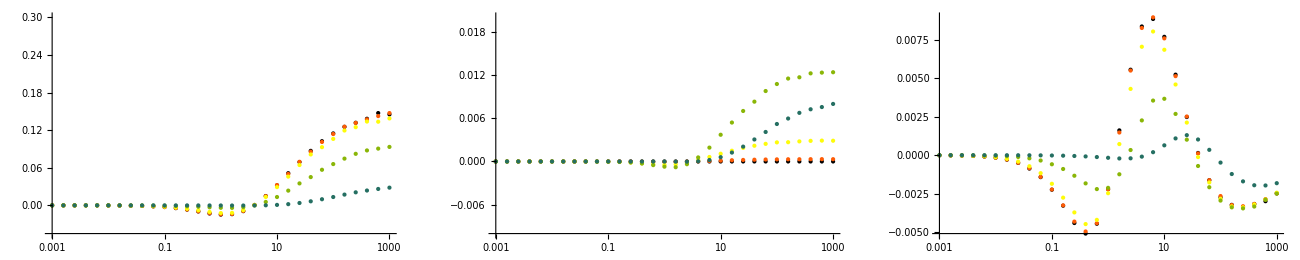

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1*^-2,1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[c1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[c1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[c1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,{-.045,.3}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,{-.01,.02}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

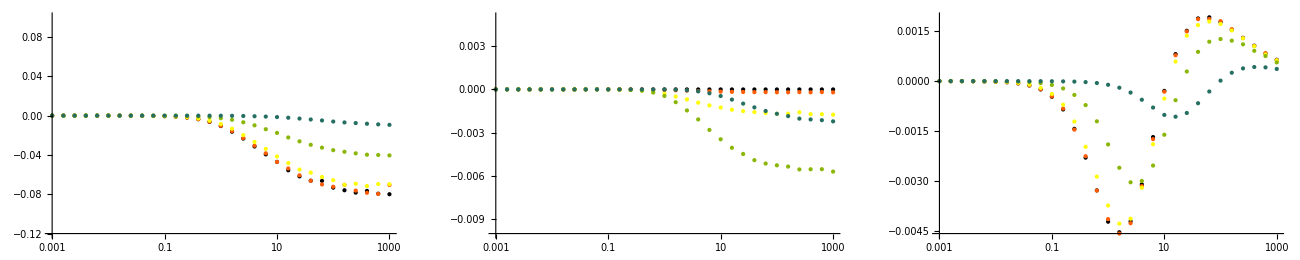

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1*^-2,1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[cbar1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[cbar1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[cbar1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,{-.12,.1}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,{-.01,.005}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

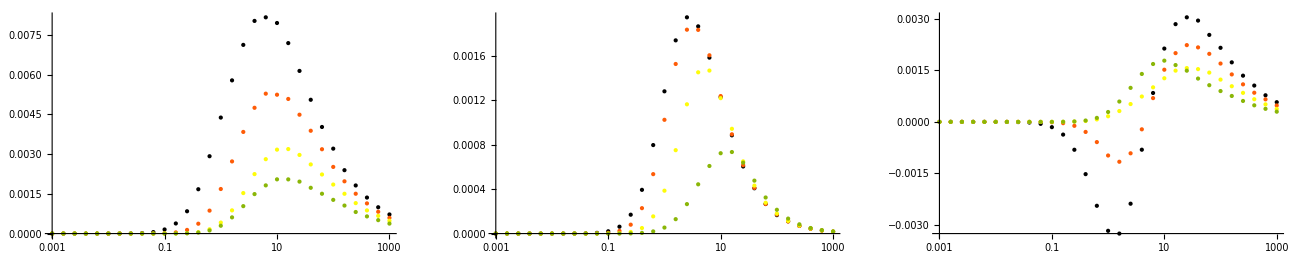

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[d1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[d1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[d1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

```mathematica
Module[{ηs,Qs,lL,lG,lT,lP},
ηs=Table[10^k,{k,-3,3,.2}];
lG=Parallelize@Table[cd1q[G][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lG;
lL=Parallelize@Table[cd1q[L][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lL;
lT=lG+1/2lL;
lP=Parallelize@Table[cd1q[P][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lP;
]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.90037×10^-16 and 2.19324×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.18412×10^-15 and 5.09297×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.26183×10^-13 and 8.44903×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.28532×10^-11 and 1.17689×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.67782×10^-13 and 6.75741×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.78144×10^-10 and 1.56842×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.45424×10^-14 and 1.49066×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.75512×10^-16 and 1.06644×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 6.60218×10^-12 and 3.37677×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.22019×10^-10 and 4.18957×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.78525×10^-13 and 2.26007×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.0786×10^-7 and 1.13987×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.728×10^-9 and 5.66466×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.72914×10^-8 and 3.49864×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.19828×10^-11 and 1.62551×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.18284×10^-7 and 6.94223×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.11941×10^-7 and 3.35881×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.80357×10^-7 and 1.88626×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.19107×10^-8 and 1.02551×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.59074×10^-7 and 9.12151×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.33991×10^-8 and 6.4364×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.11363×10^-7 and 4.88772×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.14726×10^-6 and 1.2708×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.02529×10^-10 and 1.92791×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.12753×10^-6 and 7.71135×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.93027×10^-7 and 9.67305×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.72166×10^-6 and 1.12185×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.74023×10^-6 and 6.30699×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.5568×10^-9 and 4.5613×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.63222×10^-7 and 1.35095×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.71538×10^-6 and 1.01653×10^-7 for the integral and error estimates.

{-2.90037×10^-16,4.75512×10^-16,-6.18412×10^-15,1.45424×10^-14,1.67782×10^-13,-2.78525×10^-13,-2.26183×10^-13,6.60218×10^-12,2.28532×10^-11,3.22019×10^-10,1.78144×10^-10,-1.728×10^-9,-1.19828×10^-11,-2.5568×10^-9,-2.19107×10^-8,4.02529×10^-10,1.72914×10^-8,-4.33991×10^-8,-1.0786×10^-7,-8.80357×10^-7,-4.11941×10^-7,-5.11363×10^-7,-5.18284×10^-7,-8.59074×10^-7,-2.14726×10^-6,-6.93027×10^-7,-1.72166×10^-6,-1.71538×10^-6,-1.12753×10^-6,-1.63222×10^-7,-1.74023×10^-6}

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.01601×10^-12 and 2.9277×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.19478×10^-16 and 6.62655×10^-18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.77787×10^-16 and 2.49725×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.79685×10^-13 and 9.93002×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.70374×10^-19 and 1.8901×10^-19 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.68483×10^-20 and 4.914×10^-21 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.15619×10^-11 and 8.26412×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -9.25951×10^-11 and 1.85315×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 7.05364×10^-18 and 1.16814×10^-18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.5036×10^-19 and 3.38611×10^-20 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.19436×10^-16 and 4.04138×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.08373×10^-13 and 1.53665×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.07468×10^-8 and 2.02809×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.20247×10^-7 and 7.64574×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.1536×10^-6 and 2.24416×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.03077×10^-8 and 1.63753×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.42727×10^-6 and 2.68068×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.1132×10^-7 and 1.54896×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.2375×10^-7 and 3.46099×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.75997×10^-11 and 4.96523×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.07583×10^-9 and 2.04405×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.05937×10^-7 and 1.78386×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.38107×10^-7 and 8.11118×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.11392×10^-6 and 2.97505×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.13655×10^-7 and 4.5276×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.04597×10^-8 and 5.55243×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.04636×10^-8 and 2.14363×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.83728×10^-8 and 4.86368×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.49687×10^-8 and 2.80367×10^-9 for the integral and error estimates.

{-3.68483×10^-20,-4.5036×10^-19,-6.70374×10^-19,7.05364×10^-18,1.19478×10^-16,-2.19436×10^-16,-5.77787×10^-16,-1.08373×10^-13,-3.79685×10^-13,-8.65206×10^-12,-1.01601×10^-12,-9.25951×10^-11,3.15619×10^-11,2.75997×10^-11,-2.07583×10^-9,-4.04597×10^-8,-1.03077×10^-8,-8.83728×10^-8,-4.20247×10^-7,-7.1132×10^-7,-6.07468×10^-8,-1.42727×10^-6,-3.2375×10^-7,-2.11392×10^-6,-1.1536×10^-6,-3.05937×10^-7,-1.53342×10^-6,-1.38107×10^-7,-4.13655×10^-7,-7.49687×10^-8,-5.04636×10^-8}

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.01099×10^-14 and 3.31359×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.73048×10^-12 and 7.56618×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.33961×10^-15 and 2.15397×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.48609×10^-14 and 5.44258×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.45691×10^-11 and 1.68897×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.88775×10^-11 and 1.12494×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.15169×10^-13 and 1.49022×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 7.26823×10^-13 and 3.2175×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.53737×10^-16 and 1.06525×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.01083×10^-13 and 1.97263×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.66078×10^-11 and 4.25596×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.05661×10^-9 and 5.42565×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.27016×10^-8 and 3.69608×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.29585×10^-11 and 9.69586×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.46764×10^-7 and 2.26714×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.80567×10^-7 and 1.21188×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.80189×10^-8 and 1.89953×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.49797×10^-9 and 1.73544×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.03998×10^-7 and 3.35312×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.6676×10^-7 and 7.17436×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.71354×10^-7 and 1.57345×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.03739×10^-7 and 1.71734×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.49804×10^-6 and 2.28248×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.81416×10^-7 and 7.02548×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.61445×10^-8 and 3.50494×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.6401×10^-7 and 3.67236×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.9915×10^-9 and 4.259×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.50784×10^-7 and 3.50865×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.23536×10^-7 and 1.4514×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -9.20736×10^-7 and 2.82586×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.15516×10^-7 and 4.73921×10^-9 for the integral and error estimates.

{1.33961×10^-15,2.53737×10^-16,2.01099×10^-14,1.15169×10^-13,-1.48609×10^-14,2.01083×10^-13,4.73048×10^-12,7.26823×10^-13,1.88775×10^-11,2.66078×10^-11,-3.45691×10^-11,2.05661×10^-9,1.49797×10^-9,4.9915×10^-9,-3.29585×10^-11,2.80189×10^-8,-1.27016×10^-8,-1.6676×10^-7,-1.80567×10^-7,-1.03739×10^-7,-7.6401×10^-7,-9.20736×10^-7,-5.03998×10^-7,-8.50784×10^-7,-7.46764×10^-7,-1.49804×10^-6,-2.71354×10^-7,-2.23536×10^-7,-1.81416×10^-7,-1.15516×10^-7,-5.61445×10^-8}

#### analytic

```mathematica
Last@psLogsA2
Last@psLogsA2/.psLogList[S1]
FullSimplify@Last@IntAL2finiteCoeffs
```

psLog4[S1][tpsp,s5]

(m2 sp-t1 (sp+t1+u1))/(m2 sp)

(8 π q2 (m2+sp+t1+u1) (2 m2 q2 sp+t1 (-q2 t1+sp (sp+u1))))/(sp^2 (q2+sp)^2 t1 (sp+t1+u1))

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[Last@list/.{u1-> s4-sp-t1}];
coeff=FullSimplify[Last@IntAL2finiteCoeffs/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@FullSimplify[r/.lVars/.{l[3]->ll+l[6],l[1]-> -ll+l[4],l[2]-> ll+l[5]}/.{l[5]-> l[57]+l[7]}]
]
```

(8 π q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^2 (q2+sp)^2 t1)*Log[(m2 sp-s4 t1)/(m2 sp)]

1/(9 sp^3 (q2+sp)^2 t1)2 π q2 (72 m2^2 q2 sp^3+27 m2^2 sp^4-216 m2 q2^2 sp t1^2-288 m2 q2 sp^2 t1^2-39 q2^2 sp^2 t1^2-72 m2 sp^3 t1^2-78 q2 sp^3 t1^2-39 sp^4 t1^2+6 q2^2 sp t1^3+12 q2 sp^2 t1^3+6 sp^3 t1^3+13 q2^2 t1^4+26 q2 sp t1^4+13 sp^2 t1^4-18 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 Log[t1]^2+72 m2 q2^2 sp^2 t1 Log[sp+t1]+108 m2 q2 sp^3 t1 Log[sp+t1]+12 q2^2 sp^3 t1 Log[sp+t1]+36 m2 sp^4 t1 Log[sp+t1]+24 q2 sp^4 t1 Log[sp+t1]+12 sp^5 t1 Log[sp+t1]-36 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 Log[t1] (1+Log[(sp+t1)/sp]-Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)])+72 m2 q2^2 sp t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+108 m2 q2 sp^2 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+18 q2^2 sp^2 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+36 m2 sp^3 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+36 q2 sp^3 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+18 sp^4 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-6 q2^2 t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-12 q2 sp t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-6 sp^2 t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-36 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 PolyLog[2,-t1/sp])

{Log[-(sp (4 m2+q2+sp))/(2 (q2+sp))]→l[1],Log[1/2-(2 m2)/(q2+sp)]→l[2],Log[sp (1/2-(2 m2)/(q2+sp))]→l[3],Log[sp (-1/2+(2 m2)/(q2+sp))]→l[4],Log[1/2+(2 m2)/(q2+sp)]→l[5],Log[sp (1/2+(2 m2)/(q2+sp))]→l[6],Log[(-16 m2^2+(q2+sp)^2)/(4 m2 (q2+sp))]→l[7]}

1/(9 sp (q2+sp)^3 (-4 m2+q2+sp) (4 m2+q2+sp))2 π q2 (-12 ll sp (q2+sp)^5-2304 m2^4 (q2+sp) (2 q2 (-3+l[7])+sp (-2+l[7]))+256 m2^5 sp (-13+6 l[7])+48 m2^2 (q2+sp)^3 (6 q2 (-3+l[7])+sp (-6+4 ll+3 l[7]))-3 m2 (q2+sp)^4 (6 ll^2 (2 q2+sp)+sp (47-18 l[7])+12 ll (2 q2+sp) (2+l[57]))+16 m2^3 (q2+sp)^2 (36 q2 (-2+ll (4+ll+2 l[57]))+sp (127-60 l[7]+18 ll (4+ll+2 l[57])))+36 m2 (4 m2-q2-sp) (q2+sp)^2 (4 m2+q2+sp) (2 q2+sp) (PolyLog[2,1/2-(2 m2)/(q2+sp)]-PolyLog[2,1/2+(2 m2)/(q2+sp)]))

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[list[[3]]/.{u1-> s4-sp-t1}];
coeff=FullSimplify[IntAL2finiteCoeffs[[1+3]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

-(8 π q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^2 (q2+sp)^2 t1)*Log[(q2 (m2 sp-s4 t1))/(sp (m2 q2+s4 t1))]

1/(3 sp^2 (q2+sp)^2)4 π q2 (-(3 m2^2 q2 sp^2)/t1-(3 m2^2 sp^3)/t1+13 m2 q2^2 t1+26 m2 q2 sp t1+13 m2 sp^2 t1-(64 m2^2 q2^2 √sp ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(80 m2^2 q2 sp^(3/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(8 m2 q2^2 sp^(3/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(16 m2^2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(4 m2 q2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(2 q2^2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(4 m2 sp^(7/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(4 q2 sp^(7/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(2 sp^(9/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(9 m2^2 q2^2 sp Log[m2 q2])/t1+6 m2 q2^2 t1 Log[m2 q2]+6 m2 q2 sp t1 Log[m2 q2]+(12 m2^2 q2 sp^2 Log[m2 sp])/t1+(3 m2^2 sp^3 Log[m2 sp])/t1+6 m2 q2 sp t1 Log[m2 sp]+6 m2 sp^2 t1 Log[m2 sp]+12 m2 q2^2 sp Log[t1]+18 m2 q2 sp^2 Log[t1]+6 m2 sp^3 Log[t1]+6 m2 q2^2 sp Log[t1]^2+9 m2 q2 sp^2 Log[t1]^2+3 m2 sp^3 Log[t1]^2-12 m2 q2^2 sp Log[sp+t1]-18 m2 q2 sp^2 Log[sp+t1]-2 q2^2 sp^2 Log[sp+t1]-6 m2 sp^3 Log[sp+t1]-4 q2 sp^3 Log[sp+t1]-2 sp^4 Log[sp+t1]+12 m2 q2^2 sp Log[t1] Log[(sp+t1)/sp]+18 m2 q2 sp^2 Log[t1] Log[(sp+t1)/sp]+6 m2 sp^3 Log[t1] Log[(sp+t1)/sp]-(12 m2^2 q2 sp^2 Log[-((q2+sp) t1 (sp+t1))/sp])/t1-(3 m2^2 sp^3 Log[-((q2+sp) t1 (sp+t1))/sp])/t1-6 m2 q2 sp t1 Log[-((q2+sp) t1 (sp+t1))/sp]-6 m2 sp^2 t1 Log[-((q2+sp) t1 (sp+t1))/sp]-12 m2 q2^2 sp Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-6 m2 sp^3 Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-12 m2 q2^2 sp Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]-6 m2 sp^3 Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]+(12 m2^2 q2 sp^2 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/t1+(3 m2^2 sp^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/t1-12 m2 q2^2 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-12 m2 q2 sp t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-3 q2^2 sp t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-6 q2 sp^2 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-3 sp^3 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+2 q2 t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+(q2^2 t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/sp+sp t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-12 m2 q2^2 sp Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-18 m2 q2 sp^2 Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-6 m2 sp^3 Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+q2^2 sp^2 Log[m2 sp+t1 (sp+t1)]+2 q2 sp^3 Log[m2 sp+t1 (sp+t1)]+sp^4 Log[m2 sp+t1 (sp+t1)]-(9 m2^2 q2^2 sp Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp])/t1-6 m2 q2^2 t1 Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp]-6 m2 q2 sp t1 Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp]+6 m2 sp (2 q2^2+3 q2 sp+sp^2) PolyLog[2,-t1/sp]-6 m2 sp (2 q2^2+3 q2 sp+sp^2) PolyLog[2,(2 t1)/(-sp+√(sp (-4 m2+sp)))]-12 m2 q2^2 sp PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))]-6 m2 sp^3 PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))])

{Log[m2 q2]→l[1],Log[m2 sp]→l[2],Log[-(sp (4 m2+q2+sp))/(2 (q2+sp))]→l[3],Log[(-4 m2+q2+sp)/(2 (q2+sp))]→l[4],Log[sp (1/2-(2 m2)/(q2+sp))]→l[5],Log[sp (-1/2+(2 m2)/(q2+sp))]→l[6],Log[(4 m2+q2+sp)/(2 (q2+sp))]→l[7],Log[sp (1/2+(2 m2)/(q2+sp))]→l[8],Log[(sp (-16 m2^2+(q2+sp)^2))/(4 (q2+sp))]→l[9],Log[(q2 (-4 m2+q2+sp) (4 m2+q2+sp))/(16 m2^2 sp+4 m2 (q2+sp)^2-sp (q2+sp)^2)]→l[10],Log[(16 m2^2 sp+4 m2 (q2+sp)^2-sp (q2+sp)^2)/(4 (q2+sp))]→l[11],Log[1+(sp (-4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]→l[12],Log[1+(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]→l[13],Log[1+((4 m2-q2-sp) sp)/((q2+sp) (sp+√(sp (-4 m2+sp))))]→l[14],Log[1-(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]→l[15]}

1/(3 sp^2 (q2+sp)^3 (-16 m2^2+(q2+sp)^2))4 π q2 (-832 m2^4 q2^2 sp+48 m2^3 q2^3 sp+52 m2^2 q2^4 sp-1664 m2^4 q2 sp^2+144 m2^3 q2^2 sp^2+208 m2^2 q2^3 sp^2-832 m2^4 sp^3+144 m2^3 q2 sp^3+312 m2^2 q2^2 sp^3+48 m2^3 sp^4+208 m2^2 q2 sp^4+52 m2^2 sp^5+(2048 m2^4 q2^3 √sp ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(128 m2^2 q2^5 √sp ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4608 m2^4 q2^2 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(256 m2^3 q2^3 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(544 m2^2 q2^4 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(16 m2 q2^5 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(3072 m2^4 q2 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(384 m2^3 q2^2 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(960 m2^2 q2^3 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(56 m2 q2^4 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4 q2^5 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(512 m2^4 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(896 m2^2 q2^2 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(64 m2 q2^3 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(20 q2^4 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(128 m2^3 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(448 m2^2 q2 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(16 m2 q2^2 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(40 q2^3 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(96 m2^2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(16 m2 q2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(40 q2^2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(8 m2 sp^(13/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(20 q2 sp^(13/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4 sp^(15/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-144 m2^3 q2^4 l[1]-384 m2^4 q2^2 sp l[1]-288 m2^3 q2^3 sp l[1]+24 m2^2 q2^4 sp l[1]-384 m2^4 q2 sp^2 l[1]-144 m2^3 q2^2 sp^2 l[1]+72 m2^2 q2^3 sp^2 l[1]+72 m2^2 q2^2 sp^3 l[1]+24 m2^2 q2 sp^4 l[1]-192 m2^3 q2^3 sp l[2]-384 m2^4 q2 sp^2 l[2]-432 m2^3 q2^2 sp^2 l[2]+24 m2^2 q2^3 sp^2 l[2]-384 m2^4 sp^3 l[2]-288 m2^3 q2 sp^3 l[2]+72 m2^2 q2^2 sp^3 l[2]-48 m2^3 sp^4 l[2]+72 m2^2 q2 sp^4 l[2]+24 m2^2 sp^5 l[2]+192 m2^3 q2^3 sp l[3]-12 m2 q2^5 sp l[3]+480 m2^3 q2^2 sp^2 l[3]-54 m2 q2^4 sp^2 l[3]+384 m2^3 q2 sp^3 l[3]-96 m2 q2^3 sp^3 l[3]+96 m2^3 sp^4 l[3]-84 m2 q2^2 sp^4 l[3]-36 m2 q2 sp^5 l[3]-6 m2 sp^6 l[3]+96 m2^3 q2^3 sp l[3]^2-6 m2 q2^5 sp l[3]^2+240 m2^3 q2^2 sp^2 l[3]^2-27 m2 q2^4 sp^2 l[3]^2+192 m2^3 q2 sp^3 l[3]^2-48 m2 q2^3 sp^3 l[3]^2+48 m2^3 sp^4 l[3]^2-42 m2 q2^2 sp^4 l[3]^2-18 m2 q2 sp^5 l[3]^2-3 m2 sp^6 l[3]^2+192 m2^3 q2^3 sp l[3] l[4]-12 m2 q2^5 sp l[3] l[4]+480 m2^3 q2^2 sp^2 l[3] l[4]-54 m2 q2^4 sp^2 l[3] l[4]+384 m2^3 q2 sp^3 l[3] l[4]-96 m2 q2^3 sp^3 l[3] l[4]+96 m2^3 sp^4 l[3] l[4]-84 m2 q2^2 sp^4 l[3] l[4]-36 m2 q2 sp^5 l[3] l[4]-6 m2 sp^6 l[3] l[4]-192 m2^3 q2^3 sp l[5]+12 m2 q2^5 sp l[5]-480 m2^3 q2^2 sp^2 l[5]-32 m2^2 q2^3 sp^2 l[5]+54 m2 q2^4 sp^2 l[5]+2 q2^5 sp^2 l[5]-384 m2^3 q2 sp^3 l[5]-96 m2^2 q2^2 sp^3 l[5]+96 m2 q2^3 sp^3 l[5]+10 q2^4 sp^3 l[5]-96 m2^3 sp^4 l[5]-96 m2^2 q2 sp^4 l[5]+84 m2 q2^2 sp^4 l[5]+20 q2^3 sp^4 l[5]-32 m2^2 sp^5 l[5]+36 m2 q2 sp^5 l[5]+20 q2^2 sp^5 l[5]+6 m2 sp^6 l[5]+10 q2 sp^6 l[5]+2 sp^7 l[5]-192 m2^3 q2^3 sp l[6]+12 m2 q2^5 sp l[6]-480 m2^3 q2^2 sp^2 l[6]+54 m2 q2^4 sp^2 l[6]-384 m2^3 q2 sp^3 l[6]+96 m2 q2^3 sp^3 l[6]-96 m2^3 sp^4 l[6]+84 m2 q2^2 sp^4 l[6]+36 m2 q2 sp^5 l[6]+6 m2 sp^6 l[6]-96 m2^3 q2^3 sp l[6]^2+6 m2 q2^5 sp l[6]^2-240 m2^3 q2^2 sp^2 l[6]^2+27 m2 q2^4 sp^2 l[6]^2-192 m2^3 q2 sp^3 l[6]^2+48 m2 q2^3 sp^3 l[6]^2-48 m2^3 sp^4 l[6]^2+42 m2 q2^2 sp^4 l[6]^2+18 m2 q2 sp^5 l[6]^2+3 m2 sp^6 l[6]^2-192 m2^3 q2^3 sp l[6] l[7]+12 m2 q2^5 sp l[6] l[7]-480 m2^3 q2^2 sp^2 l[6] l[7]+54 m2 q2^4 sp^2 l[6] l[7]-384 m2^3 q2 sp^3 l[6] l[7]+96 m2 q2^3 sp^3 l[6] l[7]-96 m2^3 sp^4 l[6] l[7]+84 m2 q2^2 sp^4 l[6] l[7]+36 m2 q2 sp^5 l[6] l[7]+6 m2 sp^6 l[6] l[7]+192 m2^3 q2^3 sp l[8]-12 m2 q2^5 sp l[8]+480 m2^3 q2^2 sp^2 l[8]+32 m2^2 q2^3 sp^2 l[8]-54 m2 q2^4 sp^2 l[8]-2 q2^5 sp^2 l[8]+384 m2^3 q2 sp^3 l[8]+96 m2^2 q2^2 sp^3 l[8]-96 m2 q2^3 sp^3 l[8]-10 q2^4 sp^3 l[8]+96 m2^3 sp^4 l[8]+96 m2^2 q2 sp^4 l[8]-84 m2 q2^2 sp^4 l[8]-20 q2^3 sp^4 l[8]+32 m2^2 sp^5 l[8]-36 m2 q2 sp^5 l[8]-20 q2^2 sp^5 l[8]-6 m2 sp^6 l[8]-10 q2 sp^6 l[8]-2 sp^7 l[8]+192 m2^3 q2^3 sp l[9]+384 m2^4 q2 sp^2 l[9]+432 m2^3 q2^2 sp^2 l[9]-24 m2^2 q2^3 sp^2 l[9]+384 m2^4 sp^3 l[9]+288 m2^3 q2 sp^3 l[9]-72 m2^2 q2^2 sp^3 l[9]+48 m2^3 sp^4 l[9]-72 m2^2 q2 sp^4 l[9]-24 m2^2 sp^5 l[9]+768 m2^4 q2^2 sp l[10]-192 m2^3 q2^3 sp l[10]-48 m2^2 q2^4 sp l[10]-256 m2^5 sp^2 l[10]+768 m2^4 q2 sp^2 l[10]-272 m2^3 q2^2 sp^2 l[10]-144 m2^2 q2^3 sp^2 l[10]-9 m2 q2^4 sp^2 l[10]+32 m2^3 q2 sp^3 l[10]-144 m2^2 q2^2 sp^3 l[10]-36 m2 q2^3 sp^3 l[10]+112 m2^3 sp^4 l[10]-48 m2^2 q2 sp^4 l[10]-54 m2 q2^2 sp^4 l[10]-36 m2 q2 sp^5 l[10]-9 m2 sp^6 l[10]-192 m2^3 q2^3 sp l[3] l[10]+12 m2 q2^5 sp l[3] l[10]-480 m2^3 q2^2 sp^2 l[3] l[10]+54 m2 q2^4 sp^2 l[3] l[10]-384 m2^3 q2 sp^3 l[3] l[10]+96 m2 q2^3 sp^3 l[3] l[10]-96 m2^3 sp^4 l[3] l[10]+84 m2 q2^2 sp^4 l[3] l[10]+36 m2 q2 sp^5 l[3] l[10]+6 m2 sp^6 l[3] l[10]+192 m2^3 q2^3 sp l[6] l[10]-12 m2 q2^5 sp l[6] l[10]+480 m2^3 q2^2 sp^2 l[6] l[10]-54 m2 q2^4 sp^2 l[6] l[10]+384 m2^3 q2 sp^3 l[6] l[10]-96 m2 q2^3 sp^3 l[6] l[10]+96 m2^3 sp^4 l[6] l[10]-84 m2 q2^2 sp^4 l[6] l[10]-36 m2 q2 sp^5 l[6] l[10]-6 m2 sp^6 l[6] l[10]+144 m2^3 q2^4 l[11]+384 m2^4 q2^2 sp l[11]+288 m2^3 q2^3 sp l[11]-24 m2^2 q2^4 sp l[11]+384 m2^4 q2 sp^2 l[11]+144 m2^3 q2^2 sp^2 l[11]-72 m2^2 q2^3 sp^2 l[11]-72 m2^2 q2^2 sp^3 l[11]-24 m2^2 q2 sp^4 l[11]+192 m2^3 q2^3 sp l[6] l[12]-12 m2 q2^5 sp l[6] l[12]+480 m2^3 q2^2 sp^2 l[6] l[12]-54 m2 q2^4 sp^2 l[6] l[12]+384 m2^3 q2 sp^3 l[6] l[12]-96 m2 q2^3 sp^3 l[6] l[12]+96 m2^3 sp^4 l[6] l[12]-84 m2 q2^2 sp^4 l[6] l[12]-36 m2 q2 sp^5 l[6] l[12]-6 m2 sp^6 l[6] l[12]-192 m2^3 q2^3 sp l[3] l[13]+12 m2 q2^5 sp l[3] l[13]-480 m2^3 q2^2 sp^2 l[3] l[13]+54 m2 q2^4 sp^2 l[3] l[13]-384 m2^3 q2 sp^3 l[3] l[13]+96 m2 q2^3 sp^3 l[3] l[13]-96 m2^3 sp^4 l[3] l[13]+84 m2 q2^2 sp^4 l[3] l[13]+36 m2 q2 sp^5 l[3] l[13]+6 m2 sp^6 l[3] l[13]+192 m2^3 q2^3 sp l[6] l[14]-12 m2 q2^5 sp l[6] l[14]+480 m2^3 q2^2 sp^2 l[6] l[14]-54 m2 q2^4 sp^2 l[6] l[14]+384 m2^3 q2 sp^3 l[6] l[14]-96 m2 q2^3 sp^3 l[6] l[14]+96 m2^3 sp^4 l[6] l[14]-84 m2 q2^2 sp^4 l[6] l[14]-36 m2 q2 sp^5 l[6] l[14]-6 m2 sp^6 l[6] l[14]-192 m2^3 q2^3 sp l[3] l[15]+12 m2 q2^5 sp l[3] l[15]-480 m2^3 q2^2 sp^2 l[3] l[15]+54 m2 q2^4 sp^2 l[3] l[15]-384 m2^3 q2 sp^3 l[3] l[15]+96 m2 q2^3 sp^3 l[3] l[15]-96 m2^3 sp^4 l[3] l[15]+84 m2 q2^2 sp^4 l[3] l[15]+36 m2 q2 sp^5 l[3] l[15]+6 m2 sp^6 l[3] l[15]+6 m2 sp (q2+sp)^2 (2 q2+sp) (-16 m2^2+(q2+sp)^2) PolyLog[2,(-4 m2+q2+sp)/(2 (q2+sp))]-6 m2 sp (q2+sp)^2 (2 q2+sp) (-16 m2^2+(q2+sp)^2) PolyLog[2,(4 m2+q2+sp)/(2 (q2+sp))]+192 m2^3 q2^3 sp PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-12 m2 q2^5 sp PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+480 m2^3 q2^2 sp^2 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-54 m2 q2^4 sp^2 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+384 m2^3 q2 sp^3 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-96 m2 q2^3 sp^3 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+96 m2^3 sp^4 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-84 m2 q2^2 sp^4 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-36 m2 q2 sp^5 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-6 m2 sp^6 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-192 m2^3 q2^3 sp PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+12 m2 q2^5 sp PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-480 m2^3 q2^2 sp^2 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+54 m2 q2^4 sp^2 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-384 m2^3 q2 sp^3 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+96 m2 q2^3 sp^3 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-96 m2^3 sp^4 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+84 m2 q2^2 sp^4 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+36 m2 q2 sp^5 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+6 m2 sp^6 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+192 m2^3 q2^3 sp PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-12 m2 q2^5 sp PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+480 m2^3 q2^2 sp^2 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-54 m2 q2^4 sp^2 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+384 m2^3 q2 sp^3 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-96 m2 q2^3 sp^3 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+96 m2^3 sp^4 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-84 m2 q2^2 sp^4 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-36 m2 q2 sp^5 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-6 m2 sp^6 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-192 m2^3 q2^3 sp PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+12 m2 q2^5 sp PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-480 m2^3 q2^2 sp^2 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+54 m2 q2^4 sp^2 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-384 m2^3 q2 sp^3 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+96 m2 q2^3 sp^3 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-96 m2^3 sp^4 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+84 m2 q2^2 sp^4 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+36 m2 q2 sp^5 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+6 m2 sp^6 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))])

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[list[[2]]/.{u1-> s4-sp-t1}];
coeff=FullSimplify[IntAL2finiteCoeffs[[1+2]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

-(4 π q2 (4 m2^2 (4 q2+5 sp)-2 m2 (2 q2^2+2 s4^2-5 s4 sp+4 sp^2+q2 (-4 s4+6 sp-3 t1)+s4 t1-3 sp t1)+(q2-s4+sp) (sp (q2-s4+sp)-(q2-2 s4+sp) t1)))/(sp^2 (-4 m2 (q2+sp)+(q2-s4+sp)^2)^(3/2))*Log[(2 m2 (q2+sp)+s4 (q2-s4+sp+√((-q2+s4-sp)^2-4 m2 (q2+sp))))/(2 m2 (q2+sp)-s4 (-q2+s4-sp+√((-q2+s4-sp)^2-4 m2 (q2+sp))))]

$Aborted

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=1;
coeff=Expand[IntAL2finiteCoeffs[[1+0]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
(*Print[coeff,"*",log];*)
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

$Aborted

## NLO γ*+g → Q+Qbar+g

```mathematica
getPsI[coeff_]:= MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u6,s3,u7}^({3,3,3,3}-path))]],coeff,{4}];
getPsIk2[coeff_]:= MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u6,s3,u7}^({3,3,3,3}-path))]],coeff,{4}];
getPsLogList[v_]:=DeleteDuplicates[Reap[Expand[v]/.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]]
}][[2,1]]];
```

### RQED

#### Compute

```mathematica
Do[
psIRQED[proj]=getPsI[CoeffRQED[proj]/.{k2hat2-> 0}];
IntRQED[proj]=Expand@Total[CoeffRQED[proj]*psIRQED[proj],4];
IntRQEDfinite[proj] =Coefficient[IntRQED[proj],ϵ,0];
psLogsRQED[proj]=getPsLogList[IntRQEDfinite[proj]];
,{proj,{G,L,P}}]
```

```mathematica
Module[{parallelCollect},
parallelCollect[e_]:=Module[{f,l,vs,cc},
f=e;
l=Reap[f//.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]],
psDiLog1[S_][ABC_]:> Sow[psDiLog1[S][ABC]],
psDiLog2[S_][ABC_]:> Sow[psDiLog2[S][ABC]],
psDiLog3[S_][ABC_]:> Sow[psDiLog3[S][ABC]],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[l];
Print@vs;
PrintTemporary["compute coeffs: "<>ToString@Length@vs];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el-> If[Total@First@el>0,Simplify[Last@el],Last@el]),cc];
FromCoefficientRules[cc,vs]
];
IntRQEDfinite[G]=parallelCollect[IntRQEDfinite[G]/.normKinVars/.{u1-> s4-sp-t1}];
IntRQEDfinite[L]=parallelCollect[IntRQEDfinite[L]/.normKinVars/.{u1-> s4-sp-t1}];
IntRQEDfinite[P]=parallelCollect[IntRQEDfinite[P]/.normKinVars/.{u1-> s4-sp-t1}];
]
```

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

### ROK

#### Compute

```mathematica
Do[
psIROK1[proj]=getPsI[CoeffROK1[proj]];
IntROK1[proj]=Expand@Total[CoeffROK1[proj]*psIROK1[proj],4];
psIROK2[proj]=getPsI[CoeffROK2[proj]];
IntROK2[proj]=Expand@Total[CoeffROK2[proj]*psIROK2[proj],4];
(* compute pole terms *)
IntROK1pole[proj] =Coefficient[IntROK1[proj],ϵ,-1];
IntROK2pole[proj] =Coefficient[IntROK2[proj],ϵ,-1];
(* compute finite terms *)
IntROK1finite[proj] =Coefficient[IntROK1[proj],ϵ,0];
IntROK2finite[proj] =Coefficient[IntROK2[proj],ϵ,0];
psLogsROK1[proj]=getPsLogList[IntROK1finite[proj]];
psLogsROK2[proj]=getPsLogList[IntROK2finite[proj]];
,{proj,{G,L}}]
```

```mathematica
(* polarized *)
psIRPOKk0=getPsI[CoeffRPOKk0];
psIRPOKk2=getPsIk2[CoeffRPOKk2];
IntRPOK=Expand@Total[CoeffRPOKk0*psIRPOKk0,4]+Expand@Total[CoeffRPOKk2*psIRPOKk2,4];
(* compute pole+finite terms *)
IntRPOKpole =Coefficient[IntRPOK,ϵ,-1];
IntRPOKfinite =Coefficient[IntRPOK,ϵ,0];
```

```mathematica
Module[{parallelCollect},
parallelCollect[e_]:=Module[{f,l,vs,cc},
f=e;
l=Reap[f//.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]],
psDiLog1[S_][ABC_]:> Sow[psDiLog1[S][ABC]],
psDiLog2[S_][ABC_]:> Sow[psDiLog2[S][ABC]],
psDiLog3[S_][ABC_]:> Sow[psDiLog3[S][ABC]],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[l];
Print@vs;
PrintTemporary["compute coeffs: "<>ToString@Length@vs];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el-> Simplify[Last@el]),cc];
If[0===Length@vs,Return[Last@Last@cc]];
FromCoefficientRules[cc,vs]
];
IntROK1finite[G]=parallelCollect[IntROK1finite[G]/.normKinVars/.{u1-> s4-sp-t1}];
IntROK1finite[L]=parallelCollect[IntROK1finite[L]/.normKinVars/.{u1-> s4-sp-t1}];
IntROK2finite[G]=parallelCollect[IntROK2finite[G]/.normKinVars/.{u1-> s4-sp-t1}];
IntROK2finite[L]=parallelCollect[IntROK2finite[L]/.normKinVars/.{u1-> s4-sp-t1}];
IntRPOKfinite=parallelCollect[IntRPOKfinite/.normKinVars/.{u1-> s4-sp-t1}];
]
```

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog2[S1][u7],psLog3[S1][u7]}

{psLog2[S1][u7],psLog3[S1][u7]}

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

```mathematica
Module[{poles,ShiftedBorn,Pgg,ana,n},
poles[G]=CA FullSimplify[IntROK1pole[G]+IntROK2pole[G]];
poles[L]=CA FullSimplify[IntROK1pole[L]+IntROK2pole[L]];
poles[P]=CA FullSimplify[IntRPOKpole];
ShiftedBorn[G]=(BQED[G]/.{ϵ-> 0}/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
ShiftedBorn[L]=(BQED[L]/.{ϵ-> 0}/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
ShiftedBorn[P]=(BQED[P]/.{ϵ-> 0}/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
Pgg[G][x_]= CA (2/(1-x)+2/x-4+2x-2x^2);
Pgg[L][x_]= Pgg[G][x];
Pgg[P][x_]= 2CA (1/(1-x)-2x+1);
ana[G]=-2 ShiftedBorn[G]*Pgg[G][x1]/u1/.{x1-> -u1/(sp+t1)};
ana[L]=-2 ShiftedBorn[L]*Pgg[L][x1]/u1/.{x1-> -u1/(sp+t1)};
ana[P]=-2 ShiftedBorn[P]*Pgg[P][x1]/u1/.{x1-> -u1/(sp+t1)};
n=s4/(4π(s4+m2));
Print@FullSimplify[(n poles[G]-ana[G])/.{u1-> s4-sp-t1}];
Print@FullSimplify[(n poles[L]-ana[L])/.{u1-> s4-sp-t1}];
Print@FullSimplify[(n poles[P]-ana[P])/.{u1-> s4-sp-t1}];
]
```

0

0

0

```mathematica
Module[{logs,p,a,b,c,cc},
logs=(((r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]]));
p={m2->22.5625,q2->-1000, sp-> 1090.34025,s4->0.045125000913909995,t1->-544.62551053297034};
a=(IntROK1finite[G]+IntROK2finite[G])/.logs//.{u1-> s4-sp-t1}/.p;
Print[a];
b=RHardFiniteFromPoles[G]/(Kgγ NC α αS^2 eH^2 CA CF)/.{μF2-> m2}//.{u1-> s4-sp-t1}/.p;
Print[b];
c=(Coefficient[IntRQEDfinite[G],psLog4[S2][u6,u7]])//.{u1-> s4-sp-t1}/.p;
Print[c];
Print[Join[psLogList[S1],psLogList[S2]]//.{u1-> s4-sp-t1}/.p]
]
```

-8.29095×10^17

-1367.87

0

{psLog1[S1][tpsp]→1.001,psLog1[S1][u6]→1.002,psLog1[S1][u6Msp]→1.00067,psLog2[S1][u7]→0.998004,psLog2[S1][up]→1.00109,psLog2[S1][s5]→1.,psLog2[S1][s3]→0.998004,psLog3[S1][u7]→0.998004,psLog3[S1][up]→0.998911,psLog3[S1][s5]→1.,psLog3[S1][s3]→1.002,psLog4[S1][tpsp,up]→0.99991,psLog4[S1][tpsp,s5]→1.001,psLog4[S1][u6,s3]→0.996012,psLog4[S1][u6,u7]→1.004,psLog4[S1][u6Msp,s3]→0.99734,psLog4[S1][u6Msp,u7]→1.00267,psLog5[S1][u7]→1.002,psLog5[S1][up]→1.,psLog5[S1][s5]→0.999999,psLog5[S1][s3]→1.,psLog1[S2][u7]→1.002,psLog2[S2][s5]→0.999999,psLog2[S2][s3]→1.002,psLog3[S2][s5]→1.,psLog3[S2][s3]→1.002,psLog4[S2][u7,s5]→0.998003,psLog4[S2][u7,s3]→1.,psLog5[S2][s5]→1.,psLog5[S2][s3]→0.998004}

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{a, Sϵ,psR,psFactor,f},
a[G]=1;
a[L]=2(1+ϵ/2);
Sϵ=(4π)^(-2-ϵ/2);
psR[i_]=64 Kgγ α αS^2 eH^2 NC CF 1/(1+ϵ/2)^2 π^3 Sϵ^2 μ2^(-ϵ/2)/Gamma[1+ϵ]*a[i]*s4/(s4+m2)*(s4^2/(s4+m2))^(ϵ/2);
psFactor[L]=2Kgγ α αS^2 eH^2 NC CA CF 1/(1+ϵ/2) 1/(4π)^(ϵ/2) 1/Gamma[1+ϵ/2];
psFactor[G]=Kgγ α αS^2 eH^2 NC CA CF 1/(1+ϵ/2)^2 1/(4π)^(ϵ/2) 1/Gamma[1+ϵ/2];
f=( s4)/(4π(s4+m2));
Print@Series[CA psR[L],{ϵ,0,1}];
Print@Series[f*psFactor[L],{ϵ,0,1}];
Print@Series[CA psR[G],{ϵ,0,1}];
Print@Series[f*psFactor[G],{ϵ,0,1}];
]
```

(CA CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-1+2 EulerGamma-4 Log[2]-2 Log[π]+Log[s4^2/(m2+s4)]-Log[μ2]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

(CA CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-1+EulerGamma-2 Log[2]-Log[π]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

(CA CF eH^2 Kgγ NC s4 α αS^2)/(4 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-2+2 EulerGamma-2 Log[4 π]+Log[s4^2/(m2+s4)]-Log[μ2]) ϵ)/(8 π (m2+s4))+O[ϵ]^2

(CA CF eH^2 Kgγ NC s4 α αS^2)/(4 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-2+EulerGamma-2 Log[2]-Log[π]) ϵ)/(8 π (m2+s4))+O[ϵ]^2

```mathematica
Module[{me,refPole,denom},
me[G]=(s4)/(4π(s4+m2))(IntROK1pole[G]+IntROK2pole[G]);
denom[G]=t1^2(sp+t1)^3u1^4 s4;
refPole[G]=2(-1/u1)*(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
(-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2));
Print@FullSimplify@Expand[(refPole[G]-(me[G]))/.normKinVars];

me[L]=(s4)/(4π(s4+m2))(IntROK1pole[L]+IntROK2pole[L]);
denom[L]=sp^2t1(sp+t1)u1^4 s4/q2;
refPole[L]=-2((sp+t1)^2/u1^3)*
(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
(4q2/sp)((sp t1 u1p-m2 sp^2-q2 t1^2)/(sp t1 (sp+t1)));
Print@FullSimplify@Expand[(refPole[L]-(me[L]))/.normKinVars];
]
```

0

0

```mathematica
Module[{refPoleResta,refPoleRestb,c1,c2,i1,i2,sa,sb},
i1=Coefficient[psIROK1[G],ϵ,-1];
i2=Coefficient[psIROK2[G],ϵ,-1];
c1=Coefficient[CoeffROK1[G],ϵ,1];
c2=Coefficient[CoeffROK2[G],ϵ,1];
sb=(s4)/(4π(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
refPoleResta=2(-1/u1)*(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*(
-1-sp^2/(t1(sp+t1))+q2 sp/(t1 u1)-q2^2(sp+t1)/(t1 u1^2)-m2 q2 sp^2/(t1^2 u1^2)
);
refPoleRestb=8m2 sp s4/(t1 u1^3)(1-m2 sp/(t1 u1))-4m2 q2 s4/(t1^2u1^4)(t1^2+(sp+t1)^2)-4q2 s4/(t1 u1^4)((sp+t1)q2-sp u1);
Print@FullSimplify[(sb-(refPoleRestb+refPoleResta))/.normKinVars];
]
```

0

```mathematica
Module[{refPoleRest,c1,c2,i1,i2,s},
c1=Coefficient[CoeffROK1[L],ϵ,1];
c2=Coefficient[CoeffROK2[L],ϵ,1];
i1=Coefficient[psIROK1[L],ϵ,-1];
i2=Coefficient[psIROK2[L],ϵ,-1];
s=(s4)/(4π(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
refPoleRest=(8q2(sp+t1)s4/u1^4)*((sp t1 u1p - m2 sp^2-q2 t1^2)/(sp^2 t1));
Print@FullSimplify[(s-refPoleRest)/.normKinVars];
]
```

0

#### check to Marcos Code

```mathematica
FullSimplify[(s4/(4π(s4+m2)))Total[CoeffRPOKk2*psIRPOKk2,4]]
```

-(2 s4 (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1))/(sp t1^2 (sp+t1)^2 u1^2)

```mathematica
Module[{Marco,n,me,me0,diff},
Marco = <<"~/Physik/PhD/Marco/CodeIntRPOKk2.m";
n=(s4/(4π(s4+m2)))/2^5;
me =  n Total[CoeffRPOKk2*psIRPOKk2,4];
me0=Limit[me/.{sp-> s-q2},q2-> 0];
diff = FullSimplify[(me0-Marco)/.{s4-> s+t1+u1}];
Print@diff;
]
```

0

```mathematica
Module[{coeff,psI,n,me,psList,meC,Marco,MarcoC,me0C,diff},
coeff=CoeffROK2[P]/.{k2hat2-> 0};
psI = Coefficient[getPsI[coeff],ϵ,0];
psList=getPsLogList[psI];
n=(s4/(4π(s4+m2)))/2^5;
me=n Total[coeff*psI,4];
meC=CoefficientList[me,psList];
me0C=Limit[meC/.normKinVars/.{sp-> s-q2},q2-> 0];
Marco=<<"~/Physik/PhD/Marco/CodeIntROK2P.m";
MarcoC=CoefficientList[Marco,{Log[((m2+s4) t1^2 u1^2)/(m2 (s+t1)^2 (s+u1)^2)],Log[m2/(m2+s4)]}];
diff=FullSimplify[(me0C-MarcoC)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}]
]
```

{{0,0},{0,0}}

```mathematica
Module[{coeff,psI,n,meAll,psList,psList0,meC,MarcoAll,psListMarco,normLog,MarcoC,me0C,diff,me,meE1,meE2,Marco,MarcoE1,MarcoE2},
coeff=CoeffROK1[P]/.{ϵ->0,k2hat2-> 0};
psI = Coefficient[getPsI[coeff],ϵ,0];
psList=getPsLogList[psI];
Print@psList;
psList0=psList/.Join[psLogList[S1],psLogList[S2]];
psList0=FullSimplify[Limit[#/.normKinVars/.{sp-> s-q2},q2->0],Assumptions-> physAssump~Join~{s+u1> 0}]&/@psList0;
Print@psList0;
n=(s4/(4π(s4+m2)))/2^5;
meAll=n Total[coeff*psI,4];
meC=CoefficientRules[meAll,psList];
me0C=meC/.normKinVars/.{sp-> s-q2}/.{q2->0};
MarcoAll=(Get["~/Physik/PhD/Marco/CodeIntROK1aP.m"]+Get["~/Physik/PhD/Marco/CodeIntROK1bP.m"])/.{m-> Sqrt@m2};
psListMarco=DeleteDuplicates[Reap[MarcoAll/.{ln[z_]:> ln[Sow[z]]}][[2,1]]];
normLog=FullSimplify[Together[#]/.{t12-> t1^2,u12->u1^2,s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}]&;
Print[normLog/@psListMarco];
MarcoC=CoefficientRules[MarcoAll,ln[#]&/@psListMarco];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[8]] = 1;
meE2=Table[0,{j,Length@psList0}];
meE2[[6]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[1]]=1;
me =(meE1/.me0C) - (meE2/.me0C);
Marco=MarcoE1/.MarcoC;
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[8]]]," - ",ln[psList0[[6]]]," vs. ",ln[normLog@psListMarco[[1]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[1]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[3]]=1;
me =(meE1/.me0C) ;
Marco=MarcoE1/.MarcoC;
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[1]]]," vs. ",ln[normLog@psListMarco[[3]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[2]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[8]]=1;
me =(meE1/.me0C) ;
Marco=MarcoE1/.MarcoC;
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[2]]]," vs. ",ln[normLog@psListMarco[[8]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[7]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[2]]=1;
MarcoE2=Table[0,{j,Length@psListMarco}];
MarcoE2[[6]]=1;
me =(meE1/.me0C) ;
Marco=-(MarcoE1/.MarcoC)+(MarcoE2/.MarcoC);
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[7]]]," vs. -",ln[normLog@psListMarco[[2]]],"+",ln[normLog@psListMarco[[6]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[3]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[4]]=1;
me =(meE1/.me0C) ;
Marco=-(MarcoE1/.MarcoC);
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[3]]]," vs. -",ln[normLog@psListMarco[[4]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[5]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[5]]=1;
me =(meE1/.me0C) ;
Marco=(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[ln[psList0[[5]]]," vs. ",ln[normLog@psListMarco[[5]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[4]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[7]]=1;
me =(meE1/.me0C) ;
Marco=-1/2(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[ln[psList0[[4]]]," vs. -1/2",ln[normLog@psListMarco[[7]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
MarcoE1=Table[0,{j,Length@psListMarco}];
me =(meE1/.me0C);
Marco=(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[1," vs. 1: ", diff];
]
```

{psLog2[S1][s3],psLog2[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7]}

{(t1^2 (m2+s+t1+u1))/(m2 (s+t1)^2),(t1^2 u1^2 (m2+s+t1+u1))/(m2 (s+t1)^2 (s+u1)^2),-(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1)))/(-2 m2 (s+t1)-s u1+√(s u1 (4 m2 (s+t1)+s u1))),-(-2 m2 (s+t1) (s+u1)-(s+t1+u1) (s (s+t1+u1)+√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))))/(2 m2 (s+t1) (s+u1)+(s+t1+u1) (s (s+t1+u1)-√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2)))),-(s t1+2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1)))),(m2+s+t1+u1)/m2,(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2)),m2/(m2+s+t1+u1)}

{m2/(m2+s+t1+u1),(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2)),(t1^2 (m2+s+t1+u1))/(m2 (s+t1)^2),(2 m2 (s+t1)+s u1-√(s u1 (4 m2 (s+t1)+s u1)))/(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1))),-(s t1+2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1)))),(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2)),(-√s (s+t1+u1)+√(4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))/(√s (s+t1+u1)+√(4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2)),(t1^2 u1^2 (m2+s+t1+u1))/(m2 (s+t1)^2 (s+u1)^2)}

ln[m2/(m2+s+t1+u1)] - ln[(m2+s+t1+u1)/m2] vs. ln[m2/(m2+s+t1+u1)]: 0

ln[(t1^2 (m2+s+t1+u1))/(m2 (s+t1)^2)] vs. ln[(t1^2 (m2+s+t1+u1))/(m2 (s+t1)^2)]: 0

ln[(t1^2 u1^2 (m2+s+t1+u1))/(m2 (s+t1)^2 (s+u1)^2)] vs. ln[(t1^2 u1^2 (m2+s+t1+u1))/(m2 (s+t1)^2 (s+u1)^2)]: 0

ln[(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))] vs. -ln[(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))]+ln[(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))]: 0

ln[-(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1)))/(-2 m2 (s+t1)-s u1+√(s u1 (4 m2 (s+t1)+s u1)))] vs. -ln[(2 m2 (s+t1)+s u1-√(s u1 (4 m2 (s+t1)+s u1)))/(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1)))]: 0

ln[-(s t1+2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))] vs. ln[-(s t1+2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1))))]: 0

ln[-(-2 m2 (s+t1) (s+u1)-(s+t1+u1) (s (s+t1+u1)+√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))))/(2 m2 (s+t1) (s+u1)+(s+t1+u1) (s (s+t1+u1)-√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))))] vs. -1/2ln[(-√s (s+t1+u1)+√(4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))/(√s (s+t1+u1)+√(4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))]: 0

1 vs. 1: 0

```mathematica
Module[{n,meAll,psList,psList0,meC,MarcoAll,psListMarco,normLog,MarcoC,me0C,diff,me,meE1,meE2,Marco,MarcoE1,MarcoE2},
n=(s4/(4π(s4+m2)))/2^4;
meAll=n IntRQEDfinite[P];
psList=getPsLogList[meAll];
Print@psList;
psList0=psList/.Join[psLogList[S1],psLogList[S2]];
psList0=FullSimplify[Limit[#/.normKinVars/.{sp-> s-q2},q2->0],Assumptions-> physAssump~Join~{s+u1> 0}]&/@psList0;
Print@psList0;
meC=CoefficientRules[meAll,psList];
me0C=meC/.normKinVars/.{sp-> s-q2}/.{q2->0};
MarcoAll=Get["~/Physik/PhD/Marco/CodeIntRQEDP.m"]/.{m-> Sqrt@m2};
psListMarco=DeleteDuplicates[Reap[MarcoAll/.{ln[z_]:> ln[Sow[z]]}][[2,1]]];
normLog=FullSimplify[Together[#]/.{t12-> t1^2,u12->u1^2,s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}]&;
Print[normLog/@psListMarco];
MarcoC=CoefficientRules[MarcoAll,ln[#]&/@psListMarco];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[3]] = 1;
meE2=Table[0,{j,Length@psList0}];
meE2[[1]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[1]]=1;
me =(meE1/.me0C) - (meE2/.me0C);
Marco=MarcoE1/.MarcoC;
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[3]]]," - ",ln[psList0[[1]]]," vs. ",ln[normLog@psListMarco[[1]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[2]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[2]]=1;
MarcoE2=Table[0,{j,Length@psListMarco}];
MarcoE2[[5]]=1;
me =(meE1/.me0C) ;
Marco=-(MarcoE1/.MarcoC)+(MarcoE2/.MarcoC);
diff=FullSimplify[(me-Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0}];
Print[ln[psList0[[2]]]," vs. -",ln[normLog@psListMarco[[2]]],"+",ln[normLog@psListMarco[[5]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[4]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[3]]=1;
me =(meE1/.me0C) ;
Marco=-(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[ln[psList0[[4]]]," vs. -",ln[normLog@psListMarco[[3]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[5]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[6]]=1;
me =(meE1/.me0C) ;
Marco=-1/2(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[ln[psList0[[5]]]," vs. -1/2",ln[normLog@psListMarco[[6]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
meE1[[6]] = 1;
MarcoE1=Table[0,{j,Length@psListMarco}];
MarcoE1[[4]]=1;
me =(meE1/.me0C) ;
Marco=(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[ln[psList0[[6]]]," vs. -",ln[normLog@psListMarco[[4]]],": ", diff];

Print[];
meE1=Table[0,{j,Length@psList0}];
MarcoE1=Table[0,{j,Length@psListMarco}];
me =(meE1/.me0C) ;
Marco=(MarcoE1/.MarcoC);
diff=FullSimplify[(me- Marco)/.{s4-> s+t1+u1},Assumptions-> physAssump~Join~{s+u1> 0,s>0}];
Print[1," vs. 1: ", diff];
]
```

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3]}

{(m2+s+t1+u1)/m2,(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2)),m2/(m2+s+t1+u1),-(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1)))/(-2 m2 (s+t1)-s u1+√(s u1 (4 m2 (s+t1)+s u1))),-(-2 m2 (s+t1) (s+u1)-(s+t1+u1) (s (s+t1+u1)+√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))))/(2 m2 (s+t1) (s+u1)+(s+t1+u1) (s (s+t1+u1)-√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2)))),-(s t1+2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))}

{m2/(m2+s+t1+u1),(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2)),(2 m2 (s+t1)+s u1-√(s u1 (4 m2 (s+t1)+s u1)))/(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1))),-(s t1+2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1)))),(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2)),(2 m2 (s+t1) (s+u1)+√s (s+t1+u1) (√s (s+t1+u1)-√(4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2)))/(2 m2 (s+t1) (s+u1))}

ln[m2/(m2+s+t1+u1)] - ln[(m2+s+t1+u1)/m2] vs. ln[m2/(m2+s+t1+u1)]: 0

ln[(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))] vs. -ln[(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))]+ln[(2 m2+t1+u1-√(-4 m2 s+(t1+u1)^2))/(2 m2+t1+u1+√(-4 m2 s+(t1+u1)^2))]: 0

ln[-(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1)))/(-2 m2 (s+t1)-s u1+√(s u1 (4 m2 (s+t1)+s u1)))] vs. -ln[(2 m2 (s+t1)+s u1-√(s u1 (4 m2 (s+t1)+s u1)))/(2 m2 (s+t1)+s u1+√(s u1 (4 m2 (s+t1)+s u1)))]: 0

ln[-(-2 m2 (s+t1) (s+u1)-(s+t1+u1) (s (s+t1+u1)+√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))))/(2 m2 (s+t1) (s+u1)+(s+t1+u1) (s (s+t1+u1)-√(s (4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2))))] vs. -1/2ln[(2 m2 (s+t1) (s+u1)+√s (s+t1+u1) (√s (s+t1+u1)-√(4 m2 (s+t1) (s+u1)+s (s+t1+u1)^2)))/(2 m2 (s+t1) (s+u1))]: 0

ln[-(s t1+2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√(s t1 (s t1+4 m2 (s+u1))))] vs. -ln[-(s t1+2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1))))/(-s t1-2 m2 (s+u1)+√s √(t1 (s t1+4 m2 (s+u1))))]: 0

1 vs. 1: 0

### SQED, SOK

```mathematica
psLog3[S1][s3]/.psLogList[S1]//.{sp-> s-q2,-q2+t1+u1-> -s}
```

(2 m2-s-√(-4 m2 s+s^2))/(2 m2-s+√(-4 m2 s+s^2))

```mathematica
Module[{coeff,psInt},
psISQED={psI[1/s3^2],psI[1/s3],psI[1]};
coeff=CoefficientList[s3^2 EikonalFactorQED,s3];
psInt=Expand@Total[coeff*psISQED];
psInt=Normal@Series[Limit[psInt*s4/(s4+m2)^(1)*s4/ϵ/(2π),s4-> 0],{ϵ,0,0}];
IntEikonalFactorQED=Collect[psInt/.{-q2+t1+u1-> -s,psLog3[S1][s3]-> -2Log[χ],psDiLog1[S1][s3]-> PolyLog[2,1-χ^2]},ϵ,Simplify];
IntEikonalFactorQED=IntEikonalFactorQED//.{Sqrt[s(s-4m2)]-> s β,1/Sqrt[s(s-4m2)]-> 1/(s*β)};
IntEikonalFactorQED=Collect[IntEikonalFactorQED,ϵ,FullSimplify]
]
```

(-4-(4 (-2 m2+s) Log[χ])/(s β))/ϵ+(2 (s β+(2 m2-s) Log[χ] (1+Log[χ])+(2 m2-s) PolyLog[2,1-χ^2]))/(s β)

```mathematica
Module[{coeff,psInt},
psISOK={{psI[1/tp/s3],psI[1/tp]},{psI[1/s3],psI[1]}};
coeff=CoefficientList[tp s3 EikonalFactorOK,{tp,s3}];
psInt=Expand@Total[coeff*psISOK,2];
psInt=Normal@Series[Limit[(psInt)*s4/(s4+m2)^(1)*s4/ϵ(1-ϵ^2 π^2/16)/(4π),s4-> 0],{ϵ,0,0}];
IntEikonalFactorOK=Collect[psInt//.{u1-> -sp-t1,sp-> s-q2}/.{
psLog2[S1][s3]->2Log[t1/u1],psLog3[S1][s3]-> -2Log[χ],psLog5[S1][s3]-> Log[χ u1/t1],
psDiLog1[S1][s3]-> PolyLog[2,1-χ^2],psDiLog2[S1][s3]-> PolyLog[2,1-t1/(u1 χ)],psDiLog3[S1][s3]-> PolyLog[2,1-u1/(t1 χ)]
},ϵ,FullSimplify];
IntEikonalFactorOK=IntEikonalFactorOK//.{Sqrt[s(s-4m2)]-> s β,1/Sqrt[s(s-4m2)]-> 1/(s*β)};
IntEikonalFactorOK=Collect[IntEikonalFactorOK,ϵ,FullSimplify]
]
```

4/ϵ^2+(2 (Log[t1/u1]+((-2 m2+s) Log[χ])/(s β)))/ϵ+(-4 (2 m2+s (-1+β)) Log[χ]^2-s β (π^2-2 Log[(u1 χ)/t1]^2)+4 s β (PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)])+4 (-2 m2+s) PolyLog[2,1-χ^2])/(4 s β)

```mathematica
FullSimplify[(4/ϵ^2+2/ϵ(ln[t1/u1]+(s-2m2)/(s β)ln[χ])
-ln[χ]^2-3/2Zeta[2]+1/2ln[u1 χ/t1]^2+Li2[1-t1/(u1 χ)]-Li2[1-u1/(t1 χ)]
+(s-2m2)/(s β)(Li2[1-χ^2]+ln[χ]^2)
)-(IntEikonalFactorOK/.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]})]
```

0

```mathematica
Series[Gamma[1+ϵ/2]/Gamma[1+ϵ]Exp[-ϵ(EulerGamma)/2],{ϵ,0,3}]
```

1-(π^2 ϵ^2)/16-7/48 PolyGamma[2,1] ϵ^3+O[ϵ]^4

```mathematica
Module[{},
IntEikonalFactor5OK=8/ϵ^2-4/ϵ(1/β(2m2/s-1)ln@χ-4ln@βtil-ln[-t1/m2]-ln[-u1/m2])
-(ln[s/m2]+2ln[-t1/m2]+2ln[-u1/m2]-4ln[sp/m2])ln[s/m2]
+4(ln[-t1/m2]+ln[-u1/m2]-ln[sp/m2])ln[sp/m2]-1/β(2m2/s-1)*(
(8 ln@βtil-2ln[s/m2]+4ln[sp/m2]+ln@χ)ln@χ+4Li2[2β/(1+β)])
+8(ln[-t1/m2]+ln[-u1/m2])ln@βtil+16ln[βtil]^2-3zeta2-ln[χ]^2
+2Li2[1+2t1/(sp(1-β))]-2Li2[1+sp(1+β)/(2t1)]
+2Li2[1+2u1/(sp(1-β))]-2Li2[1+sp(1+β)/(2u1)]
+ln[-sp(1-β)/(2t1)]^2+ln[-sp(1-β)/(2u1)]^2;
IntEikonalFactor5QED = 4/ϵ(1/β(2m2/s-1)ln@χ-1)+1/β(2m2/s-1)*
((8ln@βtil-2ln[s/m2]+4ln[sp/m2]+ln@χ)ln@χ+4Li2[2β/(1+β)])
-8ln@βtil+2ln[s/m2]-4ln[sp/m2]-2/β ln@χ;
]
```

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{ref},
ref=-4/ϵ+2+2(s-2m2)/(s β)(-(2/ϵ+1)Log[χ]+2PolyLog[2,χ]+2PolyLog[2,-χ]-Log[χ]^2+2Log[χ]Log[1-χ^2]-Zeta[2]);
Print@ref;
Print@FullSimplify[(Expand@ref- Expand@IntEikonalFactorQED)/.{β-> Sqrt[1-4m2/s]},Assumptions-> {s>4m2,m2>0,0<χ<1}];
]
Module[{ref},
ref=4/ϵ^2+2/ϵ Log[t1/u1]+Log[χ]Log[u1/t1]+1/2Log[u1/t1]^2-1/2Log[χ]^2-3/2 Zeta[2]+PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)]-(s-2m2)/(s β)(-2/ϵ Log[χ]+2 PolyLog[2,χ]+2PolyLog[2,-χ]-Log[χ]^2+2Log[χ]Log[1-χ^2]-Zeta[2]);
Print@ref;
Print@FullSimplify[(Expand@ref- Expand@IntEikonalFactorOK)/.{β-> Sqrt[1-4m2/s]},Assumptions-> {s>4m2,m2>0,0<χ<1}];
]
```

2-4/ϵ+(2 (-2 m2+s) (-π^2/6+(-1-2/ϵ) Log[χ]-Log[χ]^2+2 Log[χ] Log[1-χ^2]+2 PolyLog[2,-χ]+2 PolyLog[2,χ]))/(s β)

0

-π^2/4+4/ϵ^2+(2 Log[t1/u1])/ϵ+1/2 Log[u1/t1]^2+Log[u1/t1] Log[χ]-Log[χ]^2/2+PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)]-((-2 m2+s) (-π^2/6-(2 Log[χ])/ϵ-Log[χ]^2+2 Log[χ] Log[1-χ^2]+2 PolyLog[2,-χ]+2 PolyLog[2,χ]))/(s β)

0

#### Comments

```mathematica
Module[{Sϵ,softPsi,Ci,s1,s2},
Sϵ=(4π)^(-2-ϵ/2);
softPsi=64 Kgγ α αS^2 eH^2 NC CF 1/(1+ϵ/2)^2 π^3 Sϵ^2 μ2^(-ϵ/2)/Gamma[1+ϵ]*(((t1 u1p-sp m2)sp - q2 t1^2)/(sp^2 μ2))^(ϵ/2);
Ci=4 α αS^2 eH^2 1/(1+ϵ/2)^2π^2 Sϵ/Gamma[1+ϵ/2]Exp[ϵ/2(EulerGamma-Log[4π])]*(((t1 u1p-sp m2)sp - q2 t1^2)/(sp^2 μ2))^(ϵ/2)*(Δ2/(μ2 m2))^(ϵ/2);
s1=Series[softPsi*2CF(Δ2/m2)^(ϵ/2),{ϵ,0,2}];
s2=Series[Ci*4 Kgγ NC CF^2,{ϵ,0,2}];
Print[FullSimplify[s1-s2/(2π)/.{Log[Δ2/m2/μ2]-> Log[Δ2/m2]-Log[μ2]}]];
s1=Series[softPsi*CA(Δ2/m2)^(ϵ/2),{ϵ,0,2}];
s2=Series[Ci*4 Kgγ NC CF CA,{ϵ,0,2}];
Print[FullSimplify[s1-s2/(4π)/.{Log[Δ2/m2/μ2]-> Log[Δ2/m2]-Log[μ2]}]];
]
```

-1/32 (CF^2 eH^2 Kgγ NC π α αS^2) ϵ^2+O[ϵ]^3

-1/64 (CA CF eH^2 Kgγ NC π α αS^2) ϵ^2+O[ϵ]^3

```mathematica
Module[{l3,rl3,dl1,rdl1},
l3=psLog3[S1][s3]/.psLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@l3;
rl3=(1/χ)^2/.normTotalCSVars;
Print@FullSimplify[Expand[l3/rl3],Assumptions-> {s>4m2,m2>0}];
dl1=psDiLog1[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl1;
rdl1=(1-χ^2)/.normTotalCSVars;
Print@FullSimplify[Expand[dl1/rdl1],Assumptions-> {s>4m2,m2>0}];
]
```

(2 m2-s-√(-4 m2 s+s^2))/(2 m2-s+√(-4 m2 s+s^2))

1

(2 √(-4 m2 s+s^2))/(-2 m2+s+√(-4 m2 s+s^2))

1

```mathematica
Module[{l2,l5,rl5,dl2,rdl2,dl3,rdl3},
l2=psLog2[S1][s3]/.psLogList[S1]/.{sp-> -u1-t1};
Print@l2;
l5=psLog5[S1][s3]/.psLogList[S1]/.{u1-> -sp-t1};
Print@l5;
rl5=(χ u1/t1)/.normTotalCSVars;
Print@FullSimplify[(l5-rl5)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
dl2=psDiLog2[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl2;
rdl2=(1-t1/(u1 χ))/.normTotalCSVars;
Print@FullSimplify[(dl2-rdl2)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
dl3=psDiLog2[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl3;
rdl3=(1-u1/(t1 χ))/.normTotalCSVars;
Print@FullSimplify[(dl2-rdl2)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
]
```

t1^2/u1^2

((2 m2-q2-sp+√((-q2-sp)^2-4 m2 (q2+sp))) (sp+t1))/(2 m2 t1)

0

(2 m2 (-q2+s)+(s+√(-4 m2 s+s^2)) t1)/(2 m2 (-q2+s+t1))

0

(2 m2 (-q2+s)+(s+√(-4 m2 s+s^2)) t1)/(2 m2 (-q2+s+t1))

0

### Mass factorization

```mathematica
Module[{a,Sϵ,bϵ,Eϵ,Pgg,
split,BornFactor,ps2to3,x1,
shiftedBorn,massCounter,ana
},
Sϵ=(4π)^(-2-ϵ/2);

(*a[G]=1;
a[L]=2(1+ϵ/2);
a[P]=1;*)
bϵ[G]=1/(2(1+ϵ/2));
bϵ[L]=1;
bϵ[P]=1;
Eϵ[G]=1/(1+ϵ/2);
Eϵ[L]=1/(1+ϵ/2);
Eϵ[P]=1;

BornFactor[i_]=32 α αS eH^2 Kgγ NC CF (Eϵ[i]*2bϵ[i])π^3 Sϵ/Gamma[1+ϵ/2]*(μ2/m2)^(-ϵ/2);
ps2to3[i_]=64 Kgγ α αS^2eH^2NC CF (Eϵ[i]*2bϵ[i])π^3 Sϵ^2 /Gamma[1+ϵ](μ2/m2)^(-ϵ) (s4/(s4+m2))(s4^2/(m2(s4+m2)))^(ϵ/2);
Print["ps2to3[G]: ",ps2to3[G]/.{ϵ-> 0}, " ps2to3[L]: ",ps2to3[L]/.{ϵ-> 0}, " ps2to3[P]: ",ps2to3[P]/.{ϵ-> 0}];
Print[];

Pgg[G][x_]:= CA (2/(1-x)+2/x-4+2x-2x^2);
Pgg[L][x_]:= Pgg[G][x];
Pgg[P][x_]:= 2CA (1/(1-x)-2x+1);
split[proj_][x_]:=Pgg[proj][x](2/ϵ+EulerGamma-Log[4π]+(Log[μF2/m2]-Log[μ2/m2]));
x1=-u1/(sp+t1);
Do[
shiftedBorn[proj]=((BornFactor[proj]*(BQED[proj]))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
massCounter[proj]=αS/(2π)*split[proj][x1]*shiftedBorn[proj] * 1/x1*1/(sp+t1);
RMassCounterPole[proj]=Simplify@SeriesCoefficient[massCounter[proj],{ϵ,0,-1}];
,{proj,{G,L,P}}];

Print["check poles G: ", Simplify[RMassCounterPole[G]-Simplify[((ps2to3[G]/.{ϵ-> 0})CA (IntROK1pole[G]+IntROK2pole[G])/.normKinVars)]]];
Print["check poles L: ", Simplify[RMassCounterPole[L]-Simplify[((ps2to3[L]/.{ϵ-> 0})CA (IntROK1pole[L]+IntROK2pole[L])/.normKinVars)]]];
Print["check poles P: ", Simplify[RMassCounterPole[P]-Simplify[((ps2to3[P]/.{ϵ-> 0})CA (IntRPOKpole)/.normKinVars)]]];
Print[];

(* compute finite contributions from poles *)
RHardFiniteFromPoles[G]=(FullSimplify@Limit[(ps2to3[G]*CA (IntROK1pole[G]+IntROK2pole[G])/ϵ-massCounter[G])/.normKinVars,ϵ-> 0])//.{sp+t1+u1-> s4,Log[z_]:> ln[z]};
RHardFiniteFromPoles[L]=(FullSimplify@Limit[(ps2to3[L]*CA (IntROK1pole[L]+IntROK2pole[L])/ϵ-massCounter[L])/.normKinVars,ϵ-> 0])//.{sp+t1+u1-> s4,Log[z_]:> ln[z]};
RHardFiniteFromPoles[P]=(FullSimplify@Limit[(ps2to3[P]*CA (IntRPOKpole)/ϵ-massCounter[P])/.normKinVars,ϵ-> 0])//.{sp+t1+u1-> s4,Log[z_]:> ln[z]};
Print["RHardFiniteFromPoles[G]: ",RHardFiniteFromPoles[G]];
Print["RHardFiniteFromPoles[L]:",RHardFiniteFromPoles[L]];
Print["RHardFiniteFromPoles[P]:",RHardFiniteFromPoles[P]];
Print[];

ana[proj_]:=1/(2π)α αS^2 eH^2Kgγ NC CF(bϵ[proj]/.{ϵ->0}) (-1/u1)Pgg[proj][x1]*(4π(BQED[proj]/.{sp-> x1 sp, t1-> x1 t1,ϵ->0})(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2])-8π(Coefficient[BQED[proj],ϵ]/.{sp-> x1 sp, t1-> x1 t1,ϵ->0}));
Print@FullSimplify[RHardFiniteFromPoles[G]-ana[G]/.{u1-> s4-sp-t1}];
Print@FullSimplify[RHardFiniteFromPoles[L]-ana[L]/.{u1-> s4-sp-t1}];
Print@FullSimplify[RHardFiniteFromPoles[P]-ana[P]/.{u1-> s4-sp-t1}];
]
```

ps2to3[G]: (CF eH^2 Kgγ NC s4 α αS^2)/(4 π (m2+s4)) ps2to3[L]: (CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4)) ps2to3[P]: (CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4))

check poles G: 0

check poles L: 0

check poles P: 0

RHardFiniteFromPoles[G]: 1/(s4 t1^2 (sp+t1)^3 u1^4)2 CA CF eH^2 Kgγ NC ((sp+t1)^2+(sp+t1) u1+u1^2)^2 α αS^2 (2 q2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 q2 sp t1 (sp+t1) u1+2 t1 (sp^2+sp t1+t1^2) u1^2-(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) (ln[s4^2/(m2 (m2+s4))]-ln[μF2/m2]))

RHardFiniteFromPoles[L]:-(16 CA CF eH^2 Kgγ NC q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2 α αS^2 (ln[s4^2/(m2 (m2+s4))]-ln[μF2/m2]))/(s4 sp^2 t1 (sp+t1) u1^4)

RHardFiniteFromPoles[P]:(2 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1) (2 (sp+t1)^2+3 (sp+t1) u1+2 u1^2) α αS^2 (ln[s4^2/(m2 (m2+s4))]-ln[μF2/m2]))/(s4 sp t1^2 (sp+t1)^2 u1^2)

0

0

0

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Hard.m",
{IntRQEDfinite,IntROK1finite,IntROK2finite,IntRPOKfinite,RHardFiniteFromPoles}
]
```

```mathematica
Integrate[Log[x]/x,x]
```

Log[x]^2/2

```mathematica
Collect[RHardFiniteFromPoles[G],ln[_],FullSimplify]
```

(4 CA CF eH^2 Kgγ NC ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (q2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-q2 sp t1 (sp+t1) u1+t1 (sp^2+sp t1+t1^2) u1^2) α αS^2)/(s4 t1^2 (sp+t1)^3 u1^4)-(2 CA CF eH^2 Kgγ NC ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) α αS^2 ln[s4^2/(m2 (m2+s4))])/(s4 t1^2 (sp+t1)^3 u1^4)+(2 CA CF eH^2 Kgγ NC ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) α αS^2 ln[μF2/m2])/(s4 t1^2 (sp+t1)^3 u1^4)

```mathematica
Module[{Pgg,x1,a},
Pgg[G][x_]:= CA (2/(1-x)+2/x-4+2x-2x^2);
x1=-u1/(sp+t1);
a=FullSimplify[Coefficient[BQED[G],ϵ]/.{sp-> x1 sp, t1-> x1 t1}/.{u1-> s4-sp-t1}];
Print@a;
Print@FullSimplify[((RHardFiniteFromPoles[G]/.{ln[z_]:> 0})/Pgg[G][x1]/a)/.{u1-> s4-sp-t1}];
]
```

-(m2 q2 sp^2 (sp+t1)+t1 (q2^2 (sp+t1)^2+q2 sp (sp+t1) (-s4+sp+t1)+(-s4+sp+t1)^2 (sp^2+sp t1+t1^2)))/(t1^2 (sp+t1) (-s4+sp+t1)^2)

(2 CF eH^2 Kgγ NC α αS^2)/(s4-sp-t1)

```mathematica
Module[{x1,Pgg},
x1=-u1/(sp+t1);
Pgg[G][x_]= CA (2/(1-x)+2/x-4+2x-2x^2);
Print@FullSimplify@Pgg[G][x1];
Collect[BQED[G]/.{sp-> x1 sp, t1-> x1 t1},ϵ,FullSimplify]
]
```

-(2 CA ((sp+t1)^2+(sp+t1) u1+u1^2)^2)/((sp+t1)^2 u1 (sp+t1+u1))

(-2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))+2 (2 m2+q2) sp t1 (sp+t1) u1-t1 (sp^2+2 sp t1+2 t1^2) u1^2)/(t1^2 (sp+t1) u1^2)+((-q2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))+q2 sp t1 (sp+t1) u1-t1 (sp^2+sp t1+t1^2) u1^2) ϵ)/(t1^2 (sp+t1) u1^2)-(sp^2 ϵ^2)/(4 t1 (sp+t1))

```mathematica
Module[{i},
i=Integrate[RHardFiniteFromPoles[P]//.{u1-> s4-sp-t1,ln[μF2/m2]->0}/.{s4-> s4Ovm2 m2}/.ln-> Log,s4Ovm2];
Collect[i,{Log[_],PolyLog[_,_]},FullSimplify]
]
```

(4 CA CF eH^2 Kgγ NC (-1+s4Ovm2) (sp^2+2 sp t1+2 t1^2) α αS^2)/(t1 (sp+t1)^2)+(2 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 Log[s4Ovm2]^2)/(m2 sp t1^2 (sp+t1)^2)+Log[-m2 s4Ovm2] ((2 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 Log[s4Ovm2^2/(1+s4Ovm2)])/(m2 sp t1^2 (sp+t1)^2)+(2 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 Log[1+s4Ovm2])/(m2 sp t1^2 (sp+t1)^2))+(4 CA CF eH^2 Kgγ NC (2 m2+sp+t1) (sp^2+2 sp t1+2 t1^2) (3 m2 sp^2+(3 q2+sp) t1 (sp+t1)) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 sp t1^2 (sp+t1)^2 (m2+sp+t1))+Log[s4Ovm2^2/(1+s4Ovm2)] ((4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2^2 s4Ovm2^2 sp t1+2 q2 t1 (sp+t1)^2+m2 sp (sp+t1) (2 sp-s4Ovm2 t1)) α αS^2)/(m2 sp t1^2 (sp+t1)^2 (-m2 s4Ovm2+sp+t1))-(8 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 t1 (sp+t1))+(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2+sp) t1 (sp+t1)) α αS^2 Log[-m2 s4Ovm2+sp+t1])/(m2 sp t1^2 (sp+t1)^2))-(8 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2+sp) t1 (sp+t1)) α αS^2 Log[(-m2 s4Ovm2+sp+t1)/(sp+t1)])/(m2 sp t1^2 (sp+t1)^2)+Log[s4Ovm2] (-(16 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+q2 t1 (sp+t1)) α αS^2)/(m2 sp t1^2 (sp+t1)^2)-(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 Log[-m2 s4Ovm2])/(m2 sp t1^2 (sp+t1)^2)+(16 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 t1 (sp+t1))-(8 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2+sp) t1 (sp+t1)) α αS^2 Log[-m2 s4Ovm2+sp+t1])/(m2 sp t1^2 (sp+t1)^2)+(8 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2-sp) t1 (sp+t1)) α αS^2 Log[(-m2 s4Ovm2+sp+t1)/(sp+t1)])/(m2 sp t1^2 (sp+t1)^2))+(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2+sp) t1 (sp+t1)) α αS^2 Log[(-m2 s4Ovm2+sp+t1)/(m2+sp+t1)])/(m2 sp t1^2 (sp+t1) (m2+sp+t1))+Log[1+s4Ovm2] ((4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2^2 sp t1+2 q2 t1 (sp+t1)^2+m2 sp (sp+t1) (2 sp+t1)) α αS^2)/(m2 sp t1^2 (sp+t1)^2 (m2+sp+t1))-(8 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 t1 (sp+t1))+(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2+sp) t1 (sp+t1)) α αS^2 Log[-m2 s4Ovm2+sp+t1])/(m2 sp t1^2 (sp+t1)^2)-(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2-sp) t1 (sp+t1)) α αS^2 Log[(-m2 s4Ovm2+sp+t1)/(m2+sp+t1)])/(m2 sp t1^2 (sp+t1)^2))+(2 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 PolyLog[2,-s4Ovm2])/(m2 sp t1^2 (sp+t1)^2)+(8 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2-sp) t1 (sp+t1)) α αS^2 PolyLog[2,(m2 s4Ovm2)/(sp+t1)])/(m2 sp t1^2 (sp+t1)^2)-(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (m2 sp^2+(q2-sp) t1 (sp+t1)) α αS^2 PolyLog[2,(m2 (1+s4Ovm2))/(m2+sp+t1)])/(m2 sp t1^2 (sp+t1)^2)

```mathematica
Module[{i},
i=Integrate[RHardFiniteFromPoles[G]//.{u1-> s4-sp-t1,ln[μF2/m2]->0}/.{s4-> s4Ovm2 m2}/.ln-> Log,s4Ovm2];
Collect[i,{Log[_],PolyLog[_,_]},FullSimplify]
]
```

-1/(6 m2 t1^2 (sp+t1)^3 (m2+sp+t1)^3 (-m2 s4Ovm2+sp+t1)^3)CA CF eH^2 Kgγ NC (3 m2^8 s4Ovm2^3 (32 sp^3+(48+s4Ovm2 (-14+5 s4Ovm2)) sp^2 t1+2 (8+3 (-2+s4Ovm2) s4Ovm2) sp t1^2+2 s4Ovm2 (2+3 s4Ovm2) t1^3)-4 t1 (sp+t1)^8 (17 q2^2+9 q2 sp+6 (2 sp^2+3 sp t1+3 t1^2))+m2^7 s4Ovm2^2 (sp+t1) (16 (-17+18 s4Ovm2) sp^3+(-416+9 s4Ovm2 (78+s4Ovm2 (-19+5 s4Ovm2))) sp^2 t1+18 (-8+s4Ovm2 (22+3 (-3+s4Ovm2) s4Ovm2)) sp t1^2+18 (-1+s4Ovm2) s4Ovm2 (2+3 s4Ovm2) t1^3+24 q2 s4Ovm2 (2 sp^2+(5-2 s4Ovm2) sp t1+4 t1^2))+m2^6 s4Ovm2 (sp+t1)^2 (8 (34+3 s4Ovm2 (-35+12 s4Ovm2)) sp^3+48 q2^2 s4Ovm2^2 t1+(416+3 s4Ovm2 (-626+s4Ovm2 (445+3 s4Ovm2 (-29+5 s4Ovm2)))) sp^2 t1+6 (24+s4Ovm2 (-170+s4Ovm2 (175+9 (-5+s4Ovm2) s4Ovm2))) sp t1^2+6 s4Ovm2 (6+s4Ovm2 (7+3 s4Ovm2 (-7+3 s4Ovm2))) t1^3-8 q2 s4Ovm2 ((23-18 s4Ovm2) sp^2+(43+18 (-4+s4Ovm2) s4Ovm2) sp t1+2 (17-18 s4Ovm2) t1^2))-m2^2 (sp+t1)^6 (48 sp^3+4 q2^2 (71+s4Ovm2 (-171+29 s4Ovm2)) t1+3 (280+s4Ovm2 (-294+37 s4Ovm2)) sp^2 t1+6 (156+s4Ovm2 (-218+31 s4Ovm2)) sp t1^2+6 (60+s4Ovm2 (-166+31 s4Ovm2)) t1^3+4 q2 ((71-38 s4Ovm2) sp^2+(154+s4Ovm2 (-247+60 s4Ovm2)) sp t1+2 (38-17 s4Ovm2) t1^2))+4 m2 (sp+t1)^7 (q2^2 (-71+38 s4Ovm2) t1-q2 (17 sp^2+(75-36 s4Ovm2) sp t1+12 t1^2)+6 t1 ((-13+5 s4Ovm2) sp^2+(-19+8 s4Ovm2) sp t1+(-15+8 s4Ovm2) t1^2))+m2^5 (sp+t1)^3 (8 (-12+s4Ovm2 (107+2 s4Ovm2 (-53+3 s4Ovm2))) sp^3+8 q2^2 s4Ovm2^2 (-23+18 s4Ovm2) t1+(-144+s4Ovm2 (1858+s4Ovm2 (-3257+3 s4Ovm2 (395+s4Ovm2 (-59+5 s4Ovm2))))) sp^2 t1+6 (-8+s4Ovm2 (166+s4Ovm2 (-417+s4Ovm2 (209+3 (-11+s4Ovm2) s4Ovm2)))) sp t1^2+6 (-2+s4Ovm2) s4Ovm2 (1+s4Ovm2 (19+s4Ovm2 (-19+3 s4Ovm2))) t1^3+4 q2 s4Ovm2 ((55+3 s4Ovm2 (-47+12 s4Ovm2)) sp^2+2 (43-3 s4Ovm2 (59+6 (-7+s4Ovm2) s4Ovm2)) sp t1+2 (34+3 s4Ovm2 (-35+12 s4Ovm2)) t1^2))+m2^3 (sp+t1)^5 (8 (-38+17 s4Ovm2) sp^3+4 q2^2 (-23+2 s4Ovm2 (85+s4Ovm2 (-71+3 s4Ovm2))) t1+(-1072+s4Ovm2 (2470-915 s4Ovm2+69 s4Ovm2^2)) sp^2 t1+6 (-136+s4Ovm2 (458+s4Ovm2 (-223+17 s4Ovm2))) sp t1^2+6 (-1+s4Ovm2) (20+s4Ovm2 (-142+17 s4Ovm2)) t1^3-4 q2 ((71+s4Ovm2 (-171+29 s4Ovm2)) sp^2+(115+s4Ovm2 (-471+(316-45 s4Ovm2) s4Ovm2)) sp t1+2 (38+s4Ovm2 (-108+17 s4Ovm2)) t1^2))-m2^4 (sp+t1)^4 (8 (38+s4Ovm2 (-108+17 s4Ovm2)) sp^3-4 q2^2 s4Ovm2 (55+3 s4Ovm2 (-47+12 s4Ovm2)) t1+(640+s4Ovm2 (-3150+s4Ovm2 (2599+9 s4Ovm2 (-53+5 s4Ovm2)))) sp^2 t1+6 (56+s4Ovm2 (-402+s4Ovm2 (475+3 s4Ovm2 (-35+3 s4Ovm2)))) sp t1^2+6 s4Ovm2 (-50+3 s4Ovm2 (49+s4Ovm2 (-23+3 s4Ovm2))) t1^3+4 q2 ((23-2 s4Ovm2 (85+s4Ovm2 (-71+3 s4Ovm2))) sp^2+(30+s4Ovm2 (-337+s4Ovm2 (533+12 (-15+s4Ovm2) s4Ovm2))) sp t1+2 (12+s4Ovm2 (-107+2 (53-3 s4Ovm2) s4Ovm2)) t1^2))) α αS^2-(2 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[s4Ovm2]^2)/(m2 t1^2 (sp+t1)^2)+Log[-m2 s4Ovm2] (-(2 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[s4Ovm2^2/(1+s4Ovm2)])/(m2 t1^2 (sp+t1)^2)-(2 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[1+s4Ovm2])/(m2 t1^2 (sp+t1)^2))+(8 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+3 q2 sp+2 sp^2+4 sp t1+4 t1^2)+2 m2 (3 sp t1 (sp+t1)+q2 (sp^2+2 sp t1+2 t1^2))) α αS^2 Log[1+(m2 s4Ovm2)/(-sp-t1)])/(3 m2 t1^2 (sp+t1)^2)-1/(3 m2 t1^2 (sp+t1)^2 (m2+sp+t1)^3)2 CA CF eH^2 Kgγ NC (60 m2^5 sp^2+t1 (sp+t1)^4 (15 q2^2+15 q2 sp+sp^2+8 sp t1+8 t1^2)+3 m2 (sp+t1)^3 (5 q2 sp^2+(q2+sp) (23 q2+8 sp) t1+10 (q2+2 sp) t1^2+18 t1^3)+6 m2^4 (2 sp (sp+t1) (13 sp+t1)+5 q2 (sp^2+2 sp t1+2 t1^2))+3 m2^2 (sp+t1)^2 (10 sp^3+26 q2^2 t1+35 sp^2 t1+38 sp t1^2+20 t1^3+q2 (23 sp^2+66 sp t1+46 t1^2))+2 m2^3 (sp+t1) (69 sp^3+15 q2^2 t1+97 sp^2 t1+35 sp t1^2+11 t1^3+q2 (39 sp^2+87 sp t1+78 t1^2))) α αS^2 Log[m2 s4Ovm2-sp-t1]+Log[s4Ovm2^2/(1+s4Ovm2)] (1/(3 m2 t1^2 (sp+t1)^3 (-m2 s4Ovm2+sp+t1)^3)CA CF eH^2 Kgγ NC (-2 t1 (sp+t1)^5 (11 q2^2-3 q2 sp+3 sp^2+6 sp t1+6 t1^2)+3 m2^5 s4Ovm2^4 t1 ((-8+s4Ovm2) sp^2+2 (-4+s4Ovm2) sp t1+2 s4Ovm2 t1^2)+3 m2^3 s4Ovm2 (sp+t1)^2 (4 sp^2 (-2 q2 s4Ovm2+7 sp)+sp (4 q2 s4Ovm2 (-4+3 s4Ovm2)+(28+s4Ovm2 (-16+3 s4Ovm2)) sp) t1+2 s4Ovm2 (-8 q2+(-8+3 s4Ovm2) sp) t1^2+6 s4Ovm2^2 t1^3)-3 m2^4 s4Ovm2^2 (sp+t1) (16 sp^3+(16+3 (-8+s4Ovm2) s4Ovm2) sp^2 t1+6 s4Ovm2^2 t1^3+2 s4Ovm2 sp t1 (2 q2 s4Ovm2+3 (-4+s4Ovm2) t1))-m2^2 (sp+t1)^3 (44 sp^3+24 q2^2 s4Ovm2^2 t1+(44+3 s4Ovm2 (4+3 s4Ovm2)) sp^2 t1+6 s4Ovm2 (2+3 s4Ovm2) sp t1^2+18 s4Ovm2^2 t1^3+6 q2 s4Ovm2 (-7 sp^2+2 (-7+2 s4Ovm2) sp t1-14 t1^2))+2 m2 (sp+t1)^4 (21 q2^2 s4Ovm2 t1-q2 (11 sp^2+(22+3 s4Ovm2) sp t1+22 t1^2)+6 t1 ((1+s4Ovm2) sp^2+(1+2 s4Ovm2) sp t1+2 s4Ovm2 t1^2))) α αS^2-(4 CA CF eH^2 Kgγ NC (2 m2^2 sp^2+t1 (sp+t1) (q2^2-q2 sp+sp^2+2 sp t1+2 t1^2)+m2 (-2 sp t1 (sp+t1)+q2 (sp^2+2 sp t1+2 t1^2))) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 t1^2 (sp+t1)^2)+(2 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[-m2 s4Ovm2+sp+t1])/(m2 t1^2 (sp+t1)^2))+Log[s4Ovm2] ((4 CA CF eH^2 Kgγ NC (22 m2^2 sp^2+t1 (sp+t1) (14 q2^2+6 sp^2+9 sp t1+9 t1^2)+2 m2 (-3 sp t1 (sp+t1)+q2 (7 sp^2+11 sp t1+11 t1^2))) α αS^2)/(3 m2 t1^2 (sp+t1)^2)+(4 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[-m2 s4Ovm2])/(m2 t1^2 (sp+t1)^2)+(8 CA CF eH^2 Kgγ NC (2 m2^2 sp^2+t1 (sp+t1) (q2^2-q2 sp+sp^2+2 sp t1+2 t1^2)+m2 (-2 sp t1 (sp+t1)+q2 (sp^2+2 sp t1+2 t1^2))) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 t1^2 (sp+t1)^2)-(4 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[-m2 s4Ovm2+sp+t1])/(m2 t1^2 (sp+t1)^2)+(4 CA CF eH^2 Kgγ NC ((8 m2+4 q2-sp) sp-2 sp t1-2 t1^2) α αS^2 Log[(-m2 s4Ovm2+sp+t1)/(sp+t1)])/(m2 t1 (sp+t1)))-(4 CA CF eH^2 Kgγ NC (sp+t1) (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+3 q2 sp+2 sp^2+4 sp t1+4 t1^2)+2 m2 (3 sp t1 (sp+t1)+q2 (sp^2+2 sp t1+2 t1^2))) α αS^2 Log[1-(m2 (1+s4Ovm2))/(m2+sp+t1)])/(3 m2 t1^2 (m2+sp+t1)^3)+Log[1+s4Ovm2] (-1/(3 m2 t1^2 (sp+t1)^3 (m2+sp+t1)^3)CA CF eH^2 Kgγ NC (3 m2^5 t1 (9 sp^2+10 sp t1+2 t1^2)+2 t1 (sp+t1)^5 (11 q2^2-3 q2 sp+3 sp^2+6 sp t1+6 t1^2)+3 m2^4 (sp+t1) (16 sp^3+sp (4 q2+43 sp) t1+30 sp t1^2+6 t1^3)+3 m2^3 (sp+t1)^2 (4 sp^2 (2 q2+7 sp)+sp (28 q2+47 sp) t1+2 (8 q2+11 sp) t1^2+6 t1^3)+m2^2 (sp+t1)^3 (44 sp^3+24 q2^2 t1+41 sp^2 t1+6 sp t1^2+18 t1^3+6 q2 (7 sp^2+18 sp t1+14 t1^2))+2 m2 (sp+t1)^4 (21 q2^2 t1+6 t1^2 (sp+2 t1)+q2 (11 sp^2+19 sp t1+22 t1^2))) α αS^2-(4 CA CF eH^2 Kgγ NC (2 m2^2 sp^2+t1 (sp+t1) (q2^2-q2 sp+sp^2+2 sp t1+2 t1^2)+m2 (-2 sp t1 (sp+t1)+q2 (sp^2+2 sp t1+2 t1^2))) α αS^2 Log[m2 s4Ovm2-sp-t1])/(m2 t1^2 (sp+t1)^2)+(2 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[-m2 s4Ovm2+sp+t1])/(m2 t1^2 (sp+t1)^2)+(2 CA CF eH^2 Kgγ NC (-8 m2 sp-4 q2 sp+sp^2+2 sp t1+2 t1^2) α αS^2 Log[1-(m2 (1+s4Ovm2))/(m2+sp+t1)])/(m2 t1 (sp+t1)))-(2 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 PolyLog[2,-s4Ovm2])/(m2 t1^2 (sp+t1)^2)+(4 CA CF eH^2 Kgγ NC ((8 m2+4 q2-sp) sp-2 sp t1-2 t1^2) α αS^2 PolyLog[2,(m2 s4Ovm2)/(sp+t1)])/(m2 t1 (sp+t1))+(2 CA CF eH^2 Kgγ NC (-8 m2 sp-4 q2 sp+sp^2+2 sp t1+2 t1^2) α αS^2 PolyLog[2,(m2 (1+s4Ovm2))/(m2+sp+t1)])/(m2 t1 (sp+t1))

```mathematica
FullSimplify[-u1/(sp+t1)/.{u1-> s4-sp-t1}]
Module[{s,i,s4max},
s[G]=FullSimplify@Series[RHardFiniteFromPoles[G]//.{u1-> s4-sp-t1,ln[μF2/m2]->0}/.{s4-> s4Ovm2 m2}/.ln-> Log,{s4Ovm2,0,0},Assumptions->{s4>0,m2>0,sp>0,t1<0,q2<0}];
s[P]=FullSimplify@Series[RHardFiniteFromPoles[P]//.{u1-> s4-sp-t1,ln[μF2/m2]->0}/.{s4-> s4Ovm2 m2}/.ln-> Log,{s4Ovm2,0,0},Assumptions->{s4>0,m2>0,sp>0,t1<0,q2<0}];
Print@s[G];
Print@s[P];
(*s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2));*)
Print@Collect[SeriesCoefficient[s[G],-1],Log[_]];
i[G]=Integrate[SeriesCoefficient[s[G],-1]/s4Ovm2,s4Ovm2];
i[P]=Integrate[SeriesCoefficient[s[P],-1]/s4Ovm2,s4Ovm2];
Print@i[G];
Print@i[P];
Print@Integrate[i[G],t1];
Print@Integrate[i[P],t1];
]
```

1-s4/(sp+t1)

-(4 (CA CF eH^2 Kgγ NC α αS^2 (-m2 q2 sp^2-t1 (sp+t1) (q2^2+q2 sp+sp^2+sp t1+t1^2)+(4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) Log[s4Ovm2])))/((m2 t1^2 (sp+t1)^2) s4Ovm2)-(2 (CA CF eH^2 Kgγ NC α αS^2 (-4 m2^2 sp^2 (q2+sp+t1)-t1 (sp+t1)^2 (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)-2 m2 (sp+t1) (2 q2^2 t1+2 sp t1 (sp+t1)+q2 (sp+t1) (sp+2 t1))+4 m2 (2 m2+q2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) Log[s4Ovm2])))/(m2 t1^2 (sp+t1)^3)+O[s4Ovm2]^1

(4 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 Log[s4Ovm2])/(m2 sp t1^2 (sp+t1)^2 s4Ovm2)-(2 (CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) α αS^2 ((sp+t1) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1))-4 m2 (m2 sp^2+q2 t1 (sp+t1)) Log[s4Ovm2])))/(m2 sp t1^2 (sp+t1)^3)+O[s4Ovm2]^1

-(4 CA CF eH^2 Kgγ NC (-m2 q2 sp^2-t1 (sp+t1) (q2^2+q2 sp+sp^2+sp t1+t1^2)) α αS^2)/(m2 t1^2 (sp+t1)^2)-(4 CA CF eH^2 Kgγ NC (4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (q2 sp^2+2 sp (q2+sp) t1+2 (q2+sp) t1^2)) α αS^2 Log[s4Ovm2])/(m2 t1^2 (sp+t1)^2)

-(2 CA CF eH^2 Kgγ NC α αS^2 Log[s4Ovm2] (-2 (m2 q2 sp^2+t1 (sp+t1) (q2^2+q2 sp+sp^2+sp t1+t1^2))+(4 m2^2 sp^2+t1 (sp+t1) (2 q2^2+2 q2 sp+sp^2+2 sp t1+2 t1^2)+2 m2 (2 sp t1 (sp+t1)+q2 (sp^2+2 sp t1+2 t1^2))) Log[s4Ovm2]))/(m2 t1^2 (sp+t1)^2)

(2 CA CF eH^2 Kgγ NC (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)) α αS^2 Log[s4Ovm2]^2)/(m2 sp t1^2 (sp+t1)^2)

-1/m2 2 CA CF eH^2 Kgγ NC α αS^2 Log[s4Ovm2] (2 t1 (-1+Log[s4Ovm2])-(2 m2 (-q2+(2 m2+q2) Log[s4Ovm2]))/t1-(2 m2 (-q2+(2 m2+q2) Log[s4Ovm2]))/(sp+t1)+((4 m2 q2-2 (q2^2+q2 sp+sp^2)+(-8 m2^2+2 q2^2+4 m2 sp+2 q2 sp+sp^2) Log[s4Ovm2]) Log[t1])/sp+((2 (-2 m2 q2+q2^2+q2 sp+sp^2)+(8 m2^2-2 q2^2-4 m2 sp-2 q2 sp-sp^2) Log[s4Ovm2]) Log[sp+t1])/sp)

(2 CA CF eH^2 Kgγ NC α αS^2 Log[s4Ovm2]^2 (-(2 m2 sp^2)/t1+4 q2 t1+2 sp t1-(2 m2 sp^2)/(sp+t1)+sp (2 q2+sp) Log[t1]-sp (2 q2+sp) Log[sp+t1]))/(m2 sp)

```mathematica
BQED[P]/.{u1-> -t1-sp} //FullSimplify
```

((sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+(2 q2+sp) t1 (sp+t1)))/(2 sp t1^2 (sp+t1)^2)

```mathematica
Module[{m2V,q2V,ΔV,ηV,spV,s4max,s4MaxVal,Mt1min,Mt1max,f},
m2V=(4+3/4)^2;
q2V=-1*^2;
ΔV=1*^-6;
ηV=550.;
spV=4m2V(1+ηV)-q2V;
Print@{m2-> m2V,q2-> q2V,sp-> spV};
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
f=Boole[Δ<s4<s4max]4*RHardFiniteFromPoles[G]//.{Kgγ NC eH^2 α αS^2 -> 1,CA-> 1,CF-> 1,μF2-> m2}/.normKinVars/.{u1-> s4-sp-t1}//.{m2-> m2V,q2-> q2V,sp-> spV,Δ-> ΔV};
Print@{t1,-Mt1max,-Mt1min};
Print@{s4,ΔV,s4max,s4MaxVal};
Print@Series[f,{s4,0,0}];
Print@Series[f/.{t1-> -25000},{s4,0,0}];
Print["s4max: ",s4max/.{t1-> -24000}];
Print@N[f/.{t1-> -24000,s4-> 1}];
Print@N[f/.{t1-> -24000,s4-> 10}];
Print@N[f/.{t1-> -24000,s4-> 25000}];
Print@N[f/.{t1-> -24000,s4-> 25500}];
Print@N[f/.{t1-> -24000,s4-> 25700}];
Plot3D[Log[f],{s4,0,s4MaxVal},{t1,-Mt1max,-Mt1min}]
]
```

{m2→361/16,q2→-100,sp→49827.8}

{t1,-49805.1,-22.6181}

{s4,1/1000000,(0.997993 (22.6181+t1) (49805.1+t1))/t1,47609.3}

Boole[1/1000000<s4<(0.997993 (22.6181+t1) (49805.1+t1))/t1] (1/((-49827.8-1. t1)^4 t1^2 (49827.8+t1)^3 s4)8. (6.16432×10^18+4.9485×10^14 t1+1.48968×10^10 t1^2+199311. t1^3+t1^4) (-2.46755×10^18+5.0639×10^19 t1+3.82209×10^15 t1^2+1.28138×10^11 t1^3+2.1623×10^6 t1^4+14.4652 t1^5+6.12683×10^17 Log[s4]-1.23015×10^19 t1 Log[s4]-9.88613×10^14 t1^2 Log[s4]-3.47484×10^10 t1^3 Log[s4]-597933. t1^4 Log[s4]-4. t1^5 Log[s4])+1/((-49827.8-1. t1)^5 t1^2 (49827.8+t1)^3)(3.36063×10^40-6.69858×10^41 t1-1.21051×10^38 t1^2-9.99217×10^33 t1^3-4.93405×10^29 t1^4-1.60011×10^25 t1^5-3.51795×10^20 t1^6-5.21924×10^15 t1^7-5.01769×10^10 t1^8-282679. t1^9-0.709141 t1^10-6.04283×10^37 Log[s4]-1.33982×10^36 t1 Log[s4]-1.60848×10^32 t1^2 Log[s4]-8.06285×10^27 t1^3 Log[s4]-2.15671×10^23 t1^4 Log[s4]-3.24571×10^18 t1^5 Log[s4]-2.60538×10^13 t1^6 Log[s4]-8.71463×10^7 t1^7 Log[s4])+O[s4]^1)

Boole[1/1000000<s4<24733.] ((-147.159+31.8603 Log[s4])/s4+(-0.706024-5.63445×10^-6 Log[s4])+O[s4]^1)

s4max: 25729.1

-148.203

-7.98123

1.98568

10.5539

75.3976

-Graphics3D-

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{refFinite,diff,c1,c2,i1,i2},
refFinite[G]=Kgγ α αS^2 eH^2NC CA CF(
((-1/u1)(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2])*(
((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))+2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)-2m2 q2/(t1^2 u1^2)(t1^2+(sp+t1)^2)
)
)+(8m2 sp s4/(t1 u1^3)(1-m2 sp/(t1 u1))-4m2 q2 s4/(t1^2u1^4)(t1^2+(sp+t1)^2)-4q2 s4/(t1 u1^4)((sp+t1)q2-sp u1))
);
i1=Coefficient[psIROK1[G],ϵ,-1];
i2=Coefficient[psIROK2[G],ϵ,-1];
c1=Coefficient[CoeffROK1[G],ϵ,1];
c2=Coefficient[CoeffROK2[G],ϵ,1];
diff[G]=1/(4π)Kgγ α αS^2eH^2 NC CA CF (s4/(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
Print[FullSimplify@Expand[(RHardFiniteFromPoles[G]+diff[G]-refFinite[G])/.normKinVars]];

refFinite[L]=2Kgγ α αS^2 eH^2NC CA CF(
(-(sp+t1)^2/u1^3)(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2])*
(
(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
4q2/sp^2*(sp t1 u1p-m2 sp^2-q2 t1^2)/(t1(sp+t1)) 
)
+(8q2(sp+t1)s4/u1^4)*((sp t1 u1p - m2 sp^2-q2 t1^2)/(sp^2 t1))
);
c1=Coefficient[CoeffROK1[L],ϵ,1];
c2=Coefficient[CoeffROK2[L],ϵ,1];
i1=Coefficient[psIROK1[L],ϵ,-1];
i2=Coefficient[psIROK2[L],ϵ,-1];
diff[L]=1/(2π)Kgγ α αS^2eH^2 NC CA CF (s4/(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
Print[FullSimplify@Expand[(RHardFiniteFromPoles[L]+diff[L]-refFinite[L])/.normKinVars]];
]
```

0

0

#### check to Marcos Code

```mathematica
Module[{Marco,me,me0,diff},
Marco = <<"~/Physik/PhD/Marco/CodeRHardFiniteFromPolesP.m"/.{Log[z_]:> ln[z]};
me = RHardFiniteFromPoles[P]/(2^6Kgγ NC CA CF α eH^2 αS^2);
me0=Limit[me/.{ln[μF2/m2]-> 0}/.{sp-> s-q2},q2-> 0];
diff = FullSimplify[(me0-Marco)/.{s4-> s+t1+u1}];
Print@diff;
Marco = <<"~/Physik/PhD/Marco/CodeRHardFiniteFromPolesScaleFP.m";
me0=Limit[Coefficient[me,ln[μF2/m2]]/.{sp-> s-q2},q2-> 0];
diff = FullSimplify[(me0-Marco)/.{s4-> s+t1+u1}];
Print@diff;
]
```

0

0

```mathematica
BQED[P]
```

-((t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(2 t1^2 u1^2 (t1+u1))

```mathematica
Kgγ NC CA CF /.normColor
```

3/2

### S+V

```mathematica
Module[{n,Sϵ},
Sϵ=(4π)^(-2-ϵ/2);
n=1/(1+ϵ/2)^2Sϵ/Gamma[1+ϵ/2];
Limit[n,ϵ-> 0]
]
```

1/(16 π^2)

```mathematica
Module[{nS,IntSOK,IntSQED,calc,nBorn,nV,Ci,nSOK,nSQED,nSEq,nFact,nRen,an},
nS[e_]:=Module[{f},
(*f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]}\
//.{ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])}\
//.{s-> sp+q2,sp-> -t1-u1};*)
f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
f=Normal@Series[f,{ϵ,0,0}]//.{Log[z_]:> ln[z]};
Collect[f,{ϵ,Li2[_],ln[_],zeta2,β},FullSimplify]
];

Do[
IntSOK[proj]=nS[IntEikonalFactorOK*BQED[proj]];
IntSQED[proj]=nS[IntEikonalFactorQED*BQED[proj]];
,{proj,{G,L,P}}];

calc[e_,ser_:True]:=Module[{f,l,vs,c},
(*f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]}\
//.{s-> sp+q2,sp-> -t1-u1};*)
f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
PrintTemporary["compute series"];
If[ser,f=Normal@Series[f,{ϵ,0,0}]//.{Log[z_]:> ln[z]}];
l=Reap[f//.{Li2[z_]:> Sow[Li2[z],Li2],ln[z_]:> Sow[ln[z],ln],Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[{l,zeta2}];
PrintTemporary["compute coeffs: "<>ToString[Length[vs]]];
c=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString[Length[c]]];
c=ParallelMap[el↦(First@el-> Simplify[Last@el]),c];
FromCoefficientRules[c,vs]
];

nBorn=32 α αS eH^2 Kgγ NC CF π^3;
nV=128 Kgγ α eH^2αS^2 NC CF π^4/(16π^2)(μ2/m2)^(-ϵ/2);
Ci=4α αS^2eH^2π^2(Δ/m2)^(ϵ)(μ2/m2)^(-ϵ/2);
nSOK=4Kgγ NC CA CF*Ci;
nSQED=4Kgγ NC CF^2*Ci;
nSEq=nBorn CF αS/(4π)(μ2/m2)^(-ϵ/2);
nFact=nBorn*αS/(2π);
nRen=nBorn*αS/(4π);
an[G]=1/(16π^2);
an[L]=2/(16π^2);
an[P]=2/(16π^2);

Do[
PrintTemporary["SVOK["<>ToString[proj]<>"]"];
SVOK[proj]=calc[an[proj](calc[nSOK*IntSOK[proj]]+nV*CA*VOK[proj]-calc[nFact*CA(2(ln[Δ/m2]-ln[-u1/m2])+11/6)(2/ϵ-(ln[μ2/m2]-ln[μF2/m2]))BQED[proj]]+calc[nRen(2/ϵ-(ln[μ2/m2]-ln[μR2/m2]))(11CA/3)BQED[proj]])];
PrintTemporary["SVQED["<>ToString[proj]<>"]"];
SVQED[proj]=calc[an[proj](calc[nSQED*IntSQED[proj]]+calc[nV*2CF*VQED[proj]]+calc[8nSEq(2/ϵ-1)BQED[proj]]),False];
,{proj,{G,L,P}}];

Print["check poles:"];
Print@Simplify@Coefficient[SVOK[G],ϵ,-2];
Print@Simplify@Coefficient[SVOK[L],ϵ,-2];
Print@Simplify@Coefficient[SVOK[P],ϵ,-2];
Print@FullSimplify@Coefficient[SVOK[G]/(BQED[G]/.{ϵ-> 0})/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SVOK[L]/BQED[L]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SVOK[P]/BQED[P]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SVQED[G]/(BQED[G]/.{ϵ-> 0})/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SVQED[L]/BQED[L]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SVQED[P]/BQED[P]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Do[
SVOK[proj]=Coefficient[SVOK[proj],ϵ,0];
SVQED[proj]=Coefficient[SVQED[proj],ϵ,0];
,{proj,{G,L,P}}];

Print["check scale"];
Do[Print@FullSimplify[Coefficient[SVOK[proj],ln[μ2/m2]]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}];,{proj,{G,L,P}}];
Do[Print@FullSimplify[Coefficient[SVOK[proj],ln[μ2/m2],2]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}];,{proj,{G,L,P}}];
Do[Print@FullSimplify[Coefficient[SVQED[proj],ln[μ2/m2]]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}];,{proj,{G,L,P}}];
(*Do[
SVOK[proj]=SVOK[proj]/.{ln[μ2/m2]-> 0};
SVQED[proj]=SVQED[proj]/.{ln[μ2/m2]-> 0};
,{proj,{G,L,P}}];*)
]
```

check poles:

0

0

0

«6 more identical outputs»

check scale

0

0

0

«6 more identical outputs»

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.SV.m",
{SVQED,SVOK}
]
```

```mathematica
FullSimplify@Coefficient[{SVOK[G]/(BQED[G]/.{ϵ-> 0}),SVOK[L]/BQED[L],SVOK[P]/BQED[P]}/(4Kgγ NC CF α αS^2 eH^2)/CA,ln[Δ/m2]^2]
FullSimplify@Coefficient[{SVOK[G]/(BQED[G]/.{ϵ-> 0}),SVOK[L]/BQED[L],SVOK[P]/BQED[P]}/(4Kgγ NC CF α αS^2 eH^2)/CA,ln[Δ/m2]]
FullSimplify@Coefficient[{SVQED[G]/(BQED[G]/.{ϵ-> 0}),SVQED[L]/BQED[L],SVQED[P]/BQED[P]}/(4Kgγ NC CF α αS^2 eH^2)/(2CF),ln[Δ/m2]]
```

{1/2,1,1}

{(s β (ln[t1/u1]-ln[μF2/m2])+(-2 m2+s) ln[χ])/(2 s β),ln[t1/u1]-ln[μF2/m2]+((-2 m2+s) ln[χ])/(s β),ln[t1/u1]-ln[μF2/m2]+((-2 m2+s) ln[χ])/(s β)}

{-(s β+(-2 m2+s) ln[χ])/(2 s β),-1+((2 m2-s) ln[χ])/(s β),-1+((2 m2-s) ln[χ])/(s β)}

```mathematica
FullSimplify@Coefficient[{SVOK[G]/(BQED[G]/.{ϵ-> 0}),SVOK[L]/BQED[L],SVOK[P]/BQED[P]}/(4Kgγ NC CF α αS^2 eH^2)/CA,ln[μF2/m2]]
FullSimplify@Coefficient[{SVOK[G]/(BQED[G]/.{ϵ-> 0}),SVOK[L]/BQED[L],SVOK[P]/BQED[P]}/(4Kgγ NC CF α αS^2 eH^2)/CA,ln[μR2/m2]]
```

{1/24 (-11+12 ln[-u1/m2]-12 ln[Δ/m2]),-11/12+ln[-u1/m2]-ln[Δ/m2],-11/12+ln[-u1/m2]-ln[Δ/m2]}

{11/24,11/12,11/12}

```mathematica
FullSimplify@Coefficient[{SVOK[G]/(BQED[G]/.{ϵ-> 0}),SVOK[L]/BQED[L],SVOK[P]/BQED[P]}/(4Kgγ NC CF α αS^2 eH^2)/CA,Li2[χ]]
```

{(2 m2-q2+t1+u1)/(2 q2 β-2 t1 β-2 u1 β),(2 m2-q2+t1+u1)/(q2 β-t1 β-u1 β),(2 m2-q2+t1+u1)/(q2 β-t1 β-u1 β)}

```mathematica
Module[{serS,IntS5OK,IntS5QED,calc,bϵ,Cg,Cϵ,nV,nS5,nSEq,nRen,nFact},
serS[e_]:=Module[{f},
f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
f=Normal@Series[f,{ϵ,0,0}]//.{Log[z_]:> ln[z]};
Collect[f,{ϵ,Li2[_],ln[_],zeta2,β},FullSimplify]
];

Do[
IntS5OK[proj]=serS[IntEikonalFactor5OK*BQED[proj]];
IntS5QED[proj]=serS[IntEikonalFactor5QED*BQED[proj]];
,{proj,{G,L,P}}];

calc[e_,ser_:True]:=Module[{f,l,vs,c},
f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
PrintTemporary["compute series"];
If[ser,f=Normal@Series[f,{ϵ,0,0}]//.{Log[z_]:> ln[z]}];
l=Reap[f//.{Li2[z_]:> Sow[Li2[z],Li2],ln[z_]:> Sow[ln[z],ln],Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[{l,zeta2}];
PrintTemporary["compute coeffs: "<>ToString[Length[vs]]];
c=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString[Length[c]]];
c=ParallelMap[el↦(First@el-> Simplify[Last@el]),c];
FromCoefficientRules[c,vs]
];

bϵ[G]=1/2*1/(1+ϵ/2);
bϵ[L]=1;
bϵ[P]=1;
Cg[proj_]:=bϵ[proj]1/(2sp)*1/2*1/(1+ϵ/2)Kgγ;
Cϵ=1/(16π^2)(μ2/m2)^(-ϵ/2);
nV=8αS^2α(4π)^3eH^2 NC Cϵ CF;
nS5=8αS^2α(4π)^3eH^2 NC Cϵ CF;

nRen=8αS^2α(4π)^3eH^2 NC Cϵ CF;
nFact=8αS^2α(4π)^3eH^2 NC Cϵ CF;
nSEq=8αS^2α(4π)^3eH^2 NC Cϵ CF;

Do[
PrintTemporary["SV5OK["<>ToString[proj]<>"]"];
SV5OK[proj]=calc[calc[Cg[proj]nS5*IntS5OK[proj]]+calc[Cg[proj]nV*VOK[proj]]-calc[yF Cg[proj]nFact(11/6+4ln[βtil])(2/ϵ-(ln[μ2/m2]-ln[μF2/m2]))BQED[proj]]+calc[yR Cg[proj]nRen(2/ϵ-(ln[μ2/m2]-ln[μR2/m2]))(11CA/3)BQED[proj]]];
PrintTemporary["SV5QED["<>ToString[proj]<>"]"];
SV5QED[proj]=calc[calc[Cg[proj]nS5*IntS5QED[proj]]+calc[Cg[proj]nV*VQED[proj]]+calc[4 Cg[proj]nSEq*(2/ϵ-1)BQED[proj]],False];
,{proj,{G,L,P}}];

Print["check poles:"];
Print@Simplify@Coefficient[SV5OK[G],ϵ,-2];
Print@Simplify@Coefficient[SV5OK[L],ϵ,-2];
Print@Simplify@Coefficient[SV5OK[P],ϵ,-2];
Print@FullSimplify@Coefficient[SV5OK[G]/(BQED[G]/.{ϵ-> 0})/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SV5OK[L]/BQED[L]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SV5OK[P]/BQED[P]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]},ϵ,-1];
Print@FullSimplify@Coefficient[SV5QED[G]/(BQED[G]/.{ϵ-> 0})/.{s-> q2-t1-u1},ϵ,-1];
Print@FullSimplify@Coefficient[SV5QED[L]/BQED[L]/.{s-> q2-t1-u1},ϵ,-1];
Print@FullSimplify@Coefficient[SV5QED[P]/BQED[P]/.{s-> q2-t1-u1},ϵ,-1];
Do[
SV5OK[proj]=Coefficient[SV5OK[proj],ϵ,0];
SV5QED[proj]=Coefficient[SV5QED[proj],ϵ,0];
,{proj,{G,L,P}}];

Print["check scale"];
Do[Print@FullSimplify[Coefficient[SV5OK[proj],ln[μ2/m2]]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}];,{proj,{G,L,P}}];
Do[Print@FullSimplify[Coefficient[SV5OK[proj],ln[μ2/m2],2]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}];,{proj,{G,L,P}}];
Do[Print@FullSimplify[Coefficient[SV5QED[proj],ln[μ2/m2]]/.{s-> q2-t1-u1,ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}];,{proj,{G,L,P}}];
(*Do[
SV5OK[proj]=SV5OK[proj]/.{ln[μ2/m2]-> 0};
SV5QED[proj]=SV5QED[proj]/.{ln[μ2/m2]-> 0};
,{proj,{G,L,P}}];*)
]
```

check poles:

-(32 CF eH^2 Kgγ NC π (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) (yS-yV) α αS^2)/(sp t1^2 u1^2)

(256 CF eH^2 Kgγ NC π q2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (yS-yV) α αS^2)/(sp t1 u1 (t1+u1)^2)

-(32 CF eH^2 Kgγ NC π (t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (yS-yV) α αS^2)/(sp t1^2 u1^2 (t1+u1))

-(4 CF eH^2 Kgγ NC π α αS^2 ((q2-t1-u1) (4 m2^2 (t1+u1)^2 (11 yF-22 CA yR+24 (yS-yV))+t1 u1 (-11 t1^2 (yF-2 CA yR)-11 u1^2 (yF-2 CA yR)+2 q2 (t1+u1) (11 yF-22 CA yR+12 yS-12 yV)+24 t1 u1 (yS-yV)+q2^2 (-22 yF+44 CA yR-24 yS+24 yV))+2 m2 (2 t1 u1 (t1+u1) (11 yF-22 CA yR+24 yS-24 yV)+q2 (t1^2 (11 yF-22 CA yR+12 yS-12 yV)+u1^2 (11 yF-22 CA yR+12 yS-12 yV)+24 t1 u1 (-yS+yV)))) β+12 (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) (-(q2-t1-u1) (yS-yV) β ln[-t1/m2]-(q2-t1-u1) β ((yS-yV) ln[-u1/m2]-2 (yF-2 yS) ln[βtil]+(-yS+yV) ln[μ2/m2])+(2 m2-q2+t1+u1) (yS-yV) ln[χ])))/(3 sp (q2-t1-u1) (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) β)

(8 CF eH^2 Kgγ NC π α αS^2 (-(q2-t1-u1) (11 yF-22 CA yR+12 yS-12 yV) β+12 ((q2-t1-u1) (yS-yV) β ln[-t1/m2]+(q2-t1-u1) β ((yS-yV) ln[-u1/m2]-2 (yF-2 yS) ln[βtil]+(-yS+yV) ln[μ2/m2])-(2 m2-q2+t1+u1) (yS-yV) ln[χ])))/(3 sp (q2-t1-u1) β)

(8 CF eH^2 Kgγ NC π α αS^2 (-(q2-t1-u1) (11 yF-22 CA yR+12 yS-12 yV) β+12 ((q2-t1-u1) (yS-yV) β ln[-t1/m2]+(q2-t1-u1) β ((yS-yV) ln[-u1/m2]-2 (yF-2 yS) ln[βtil]+(-yS+yV) ln[μ2/m2])-(2 m2-q2+t1+u1) (yS-yV) ln[χ])))/(3 sp (q2-t1-u1) β)

0

0

0

check scale

1/(3 sp t1^2 u1^2)4 CF eH^2 Kgγ NC π α αS^2 (-4 m2^2 (t1+u1)^2 (11 yF-22 CA yR+12 yS-12 yV)+t1 u1 (11 t1^2 (yF-2 CA yR)+11 u1^2 (yF-2 CA yR)+2 q2^2 (11 yF-22 CA yR+6 yS-6 yV)-2 q2 (t1+u1) (11 yF-22 CA yR+6 yS-6 yV)+12 t1 u1 (-yS+yV))+2 m2 (-2 t1 u1 (t1+u1) (11 yF-22 CA yR+12 yS-12 yV)+q2 (12 t1 u1 (yS-yV)+t1^2 (-11 yF+22 CA yR-6 yS+6 yV)+u1^2 (-11 yF+22 CA yR-6 yS+6 yV)))-(6 (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) ((q2-t1-u1) β (-(yS-yV) (ln[-t1/m2]+ln[-u1/m2])+4 (yF-yS) ln[βtil])+(2 m2-q2+t1+u1) (yS-yV) ln[χ]))/((q2-t1-u1) β))

(32 CF eH^2 Kgγ NC π q2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) α αS^2 (11 yF-22 CA yR+6 yS-6 yV+6 (-yS+yV) ln[-t1/m2]+6 (-yS+yV) ln[-u1/m2]+24 (yF-yS) ln[βtil]+(6 (2 m2-q2+t1+u1) (yS-yV) ln[χ])/((q2-t1-u1) β)))/(3 sp t1 u1 (t1+u1)^2)

(4 CF eH^2 Kgγ NC π (t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) α αS^2 (-11 yF+22 CA yR-6 yS+6 yV+6 (yS-yV) ln[-t1/m2]+6 (yS-yV) ln[-u1/m2]+24 (-yF+yS) ln[βtil]-(6 (2 m2-q2+t1+u1) (yS-yV) ln[χ])/((q2-t1-u1) β)))/(3 sp t1^2 u1^2 (t1+u1))

-(4 CF eH^2 Kgγ NC π (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) (yS-yV) α αS^2)/(sp t1^2 u1^2)

(32 CF eH^2 Kgγ NC π q2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (yS-yV) α αS^2)/(sp t1 u1 (t1+u1)^2)

-(4 CF eH^2 Kgγ NC π (t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (yS-yV) α αS^2)/(sp t1^2 u1^2 (t1+u1))

0

0

0

#### compute SVQED for q.b2->0

```mathematica
Module[{a,b,n},
n[e_]:=e//.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> π^2/6};
a=Li2[1-χ^2] //n;
b=-2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])//n;
Print@FullSimplify[a-b,Assumptions-> {0≤ χ≤ 1}];
]
```

0

```mathematica
Module[{common,showq2,sv},
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-4m2/q2]};
common=CF^2 NC eH^2 αS^2 2^6 α Kgγ;
sv=(SVQED[G]/common)//.showq2//.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}/.{sp-> s-q2,s-> q2-t1-u1};
sv=Limit[sv,q2-> 0,Assumptions-> {q2<0,u1<0,t1<0,m2>0,Δ>0,zeta2>0}];
sv=sv//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]}\
//.{ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[Δ]-> ln[Δ/m2]+ln[m2],ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])};
sv=Collect[sv,{ln[_],Li2[_],zeta2},Simplify];
sv=sv//.{π^2-> 6zeta2};
sv=Collect[sv,{ϵ,ln[_],Li2[_],zeta2,β},Simplify];
SVQEDG0=sv
]
```

(8 m2^4 (t1+u1)^2-t1^2 u1^2 (t1^2+u1^2)+3 m2 t1 u1 (t1^3+4 t1^2 u1+4 t1 u1^2+u1^3)+4 m2^3 (3 t1^3+10 t1^2 u1+10 t1 u1^2+3 u1^3)+m2^2 (4 t1^4+25 t1^3 u1+46 t1^2 u1^2+25 t1 u1^3+4 u1^4))/(64 t1^2 (m2+t1) u1^2 (m2+u1))+zeta2 ((-t1^2 u1^2 (3 t1^2+4 t1 u1+3 u1^2)+4 m2^2 (t1^4+2 t1^3 u1+2 t1 u1^3+u1^4))/(64 t1^3 u1^3)+(-32 m2^3 (t1+u1)^2-2 m2 t1 u1 (5 t1^2+22 t1 u1+5 u1^2)-8 m2^2 (2 t1^3+9 t1^2 u1+9 t1 u1^2+2 u1^3)+t1 u1 (3 t1^3-t1^2 u1-t1 u1^2+3 u1^3))/(64 t1^2 u1^2 (t1+u1) β))+((2 m2 t1^2 (t1-u1)+m2^2 (6 t1^2-4 t1 u1-2 u1^2)-t1^2 (2 t1^2+2 t1 u1+u1^2)) Li2[(m2+t1)/m2])/(32 t1^3 u1)-((2 m2 (t1-u1) u1^2+2 m2^2 (t1^2+2 t1 u1-3 u1^2)+u1^2 (t1^2+2 t1 u1+2 u1^2)) Li2[(m2+u1)/m2])/(32 t1 u1^3)-((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) Li2[-χ])/(32 t1 u1 (t1+u1) β)+((-8 m2^3 (t1+u1)^2-2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)-4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) Li2[χ])/(8 t1^2 u1^2 (t1+u1) β)+((-8 m2^2+3 t1^2+4 t1 u1+3 u1^2)/(128 t1 u1)+(32 m2^3 (t1+u1)^2+2 m2 t1 u1 (5 t1^2+22 t1 u1+5 u1^2)+t1 u1 (-3 t1^3+t1^2 u1+t1 u1^2-3 u1^3)+8 m2^2 (2 t1^3+9 t1^2 u1+9 t1 u1^2+2 u1^3))/(128 t1^2 u1^2 (t1+u1) β)) ln[χ]^2+ln[Δ/m2] ((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2))/(16 t1^2 u1^2)+((2 m2+t1+u1) (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) ln[χ])/(16 t1^2 u1^2 (t1+u1) β))+ln[-t1/m2] ((-16 m2^4 (t1+u1)+t1^3 u1 (2 t1+3 u1)-4 m2^3 (9 t1^2+12 t1 u1+u1^2)-2 m2^2 t1 (13 t1^2+23 t1 u1+2 u1^2)+m2 t1^2 (-4 t1^2-11 t1 u1+3 u1^2))/(64 t1^2 (m2+t1)^2 u1)+((-16 m2^3 (t1+u1)-2 m2 t1 u1 (t1+u1)-8 m2^2 (3 t1^2+3 t1 u1+u1^2)+t1 (2 t1^3+4 t1^2 u1+3 t1 u1^2+u1^3)) ln[χ])/(32 t1^2 u1 (t1+u1) β))+ln[-u1/m2] ((-16 m2^4 (t1+u1)+t1 u1^3 (3 t1+2 u1)+m2 u1^2 (3 t1^2-11 t1 u1-4 u1^2)-4 m2^3 (t1^2+12 t1 u1+9 u1^2)-2 m2^2 u1 (2 t1^2+23 t1 u1+13 u1^2))/(64 t1 u1^2 (m2+u1)^2)+((-16 m2^3 (t1+u1)-2 m2 t1 u1 (t1+u1)-8 m2^2 (t1^2+3 t1 u1+3 u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)) ln[χ])/(32 t1 u1^2 (t1+u1) β))+ln[χ] ((8 m2^3 (t1+u1)^2+2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)-t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3))/(32 t1^2 u1^2 (t1+u1) β)+((t1+u1) (t1 u1+m2 (t1+u1)) β)/(16 t1 u1 (4 m2+t1+u1))+((-8 m2^3 (t1+u1)^2-2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)-4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) ln[1-χ])/(8 t1^2 u1^2 (t1+u1) β)-((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) ln[1+χ])/(32 t1 u1 (t1+u1) β))

```mathematica
Module[{common,showq2,sv},
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-4m2/q2]};
common=CF^2 NC eH^2 αS^2 2^6 α Kgγ;
sv=(SVQED[P]/common)//.showq2//.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}/.{sp-> s-q2,s-> q2-t1-u1};
sv=Limit[sv,q2-> 0,Assumptions-> {q2<0,u1<0,t1<0,m2>0,Δ>0,zeta2>0}];
sv=sv//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]}\
//.{ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[Δ]-> ln[Δ/m2]+ln[m2],ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])};
sv=Collect[sv,{ln[_],Li2[_],zeta2},Simplify];
sv=sv//.{π^2-> 6zeta2};
sv=Collect[sv,{ϵ,ln[_],Li2[_],zeta2,β},Simplify];
SVQEDP0=sv
]
```

(t1^2 u1^2 (t1^2+u1^2)+4 m2^3 (t1^3+u1^3)+m2 t1 u1 (5 t1^3+4 t1^2 u1+4 t1 u1^2+5 u1^3)+m2^2 (4 t1^4+7 t1^3 u1+2 t1^2 u1^2+7 t1 u1^3+4 u1^4))/(64 t1^2 (m2+t1) u1^2 (m2+u1))+zeta2 ((t1^2 u1^2 (3 t1^2+4 t1 u1+3 u1^2)+4 m2^2 (t1^4+2 t1^3 u1-8 t1^2 u1^2+2 t1 u1^3+u1^4))/(64 t1^3 u1^3)+(t1 u1 (-3 t1^3+t1^2 u1+t1 u1^2-3 u1^3)-8 m2^2 (2 t1^3+3 t1^2 u1+3 t1 u1^2+2 u1^3)-2 m2 (4 t1^4+11 t1^3 u1+2 t1^2 u1^2+11 t1 u1^3+4 u1^4))/(64 t1^2 u1^2 (t1+u1) β))+((-2 m2 t1^2 (t1-u1)+t1^2 (2 t1^2+2 t1 u1+u1^2)-2 m2^2 (5 t1^2+2 t1 u1+u1^2)) Li2[(m2+t1)/m2])/(32 t1^3 u1)+((2 m2 (t1-u1) u1^2+u1^2 (t1^2+2 t1 u1+2 u1^2)-2 m2^2 (t1^2+2 t1 u1+5 u1^2)) Li2[(m2+u1)/m2])/(32 t1 u1^3)+((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) Li2[-χ])/(32 t1 u1 (t1+u1) β)-((t1^2+u1^2) (4 m2^2 (t1+u1)+t1 u1 (t1+u1)+2 m2 (t1^2+3 t1 u1+u1^2)) Li2[χ])/(8 t1^2 u1^2 (t1+u1) β)+(-(-24 m2^2+3 t1^2+4 t1 u1+3 u1^2)/(128 t1 u1)+(8 m2^2 (2 t1^3+3 t1^2 u1+3 t1 u1^2+2 u1^3)+t1 u1 (3 t1^3-t1^2 u1-t1 u1^2+3 u1^3)+m2 (8 t1^4+22 t1^3 u1+4 t1^2 u1^2+22 t1 u1^3+8 u1^4))/(128 t1^2 u1^2 (t1+u1) β)) ln[χ]^2+ln[Δ/m2] (((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2)+((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[χ])/(16 t1^2 u1^2 (t1+u1) β))+ln[-t1/m2] (-(t1^3 u1 (2 t1+3 u1)+4 m2^3 (3 t1^2+4 t1 u1+3 u1^2)+2 m2^2 t1 (9 t1^2+13 t1 u1+12 u1^2)+m2 t1^2 (8 t1^2+13 t1 u1+15 u1^2))/(64 t1^2 (m2+t1)^2 u1)-((8 m2^2 (-t1^2+t1 u1+u1^2)+t1 (2 t1^3+4 t1^2 u1+3 t1 u1^2+u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3)) ln[χ])/(32 t1^2 u1 (t1+u1) β))+ln[-u1/m2] (-(t1 u1^3 (3 t1+2 u1)+4 m2^3 (3 t1^2+4 t1 u1+3 u1^2)+m2 u1^2 (15 t1^2+13 t1 u1+8 u1^2)+2 m2^2 u1 (12 t1^2+13 t1 u1+9 u1^2))/(64 t1 u1^2 (m2+u1)^2)-((8 m2^2 (t1^2+t1 u1-u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3)) ln[χ])/(32 t1 u1^2 (t1+u1) β))+ln[χ] (((t1^2+u1^2) (4 m2^2 (t1+u1)+t1 u1 (t1+u1)+2 m2 (t1^2+3 t1 u1+u1^2)))/(32 t1^2 u1^2 (t1+u1) β)-((t1+u1) (t1 u1+m2 (t1+u1)) β)/(16 t1 u1 (4 m2+t1+u1))-((t1^2+u1^2) (4 m2^2 (t1+u1)+t1 u1 (t1+u1)+2 m2 (t1^2+3 t1 u1+u1^2)) ln[1-χ])/(8 t1^2 u1^2 (t1+u1) β)+((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) ln[1+χ])/(32 t1 u1 (t1+u1) β))

#### check SVQED0 to Marco

```mathematica
Module[{pathMarco,f,g,n,vars,c,me,Marco,diff},
n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β};
pathMarco="~/Physik/PhD/Marco/Virt/SVQED/";
g={
zeta2->"svqedunp.f1",
ln[-t1/m2]ln[χ]->"svqedunp.f2",
ln[-u1/m2]ln[χ]->"svqedunp.f3",
Li2[(t1+m2)/m2]-> "svqedunp.f4",
Li2[(u1+m2)/m2]-> "svqedunp.f5",
ln[-t1/m2]->"svqedunp.f6",
ln[-u1/m2]->"svqedunp.f7",
ln[1-χ]ln[χ]->"svqedunp.f8",
ln[1+χ]ln[χ]->"svqedunp.f9",
Li2[χ]-> "svqedunp.f10",
Li2[-χ]-> "svqedunp.f11",
ln[χ]^2->"svqedunp.f12",
ln[χ]->"svqedunp.f13",
1->"svqedunp.non"
};
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQEDG0,vars];
Print["me:",Length@f," vs. Marco:",Length@g,"+2"];
Do[
c=First@First@CoefficientRules[First@e,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@n@Get[pathMarco<>Last@e]/.{Li2[_]:> 1,Log[_]:> 1,zeta2-> 1};
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[First@e,": ",diff];
If[0===diff,Continue[]];
Print[First@e,"@me: ",me];
Print[First@e,"@Marco: ",Marco];
,{e,g}];
(* +2 *)
c=First@First@#&/@CoefficientRules[{ln[Δ/m2],ln[Δ/m2]ln[χ]},vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@Coefficient[n@Get[pathMarco<>"svqedunp.del"]/.{Log[delta]-> 1},Log[x],{0,1}];
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[ln[Δ/m2],": ",First@diff];
If[Not[0===First@diff],Print["ln[Δ/m2]@me: ",First@me];Print["ln[Δ/m2]@Marco: ",First@Marco]];
Print[ln[Δ/m2]ln[χ],": ",Last@diff];
If[Not[0===Last@diff],Print["ln[Δ/m2]ln[χ]@me: ",Last@me];Print["ln[Δ/m2]ln[χ]@Marco: ",Last@Marco]];
]
```

me:16 vs. Marco:14+2

zeta2: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

ln[1-χ] ln[χ]: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[1-χ] ln[χ]@me: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(8 t1^2 u1^2 (t1+u1) β)

ln[1-χ] ln[χ]@Marco: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) β)/(16 t1^2 u1^2 (4 m2+t1+u1))

ln[χ] ln[1+χ]: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[χ] ln[1+χ]@me: -((4 m2+t1+u1) (t1^2+4 t1 u1+u1^2-2 m2 (t1+u1)))/(32 t1 u1 (t1+u1) β)

ln[χ] ln[1+χ]@Marco: (16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+5 t1 u1+u1^2)-t1 u1 (3 t1^2+4 t1 u1+3 u1^2))/(32 t1^2 u1^2 β)

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[χ]: ((2 m2+t1+u1) (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[χ]@me: (32 m2^4 (t1+u1)^2+8 m2^3 (t1+u1) (3 t1+u1) (t1+3 u1)+4 m2^2 (t1^2+4 t1 u1+u1^2)^2-t1 u1 (t1+u1)^2 (t1^2+u1^2-2 t1 u1 β^2)+2 m2 t1 u1 (-t1^3+3 t1^2 u1+3 t1 u1^2-u1^3+(t1+u1)^3 β^2))/(32 t1^2 u1^2 (t1+u1) (4 m2+t1+u1) β)

ln[χ]@Marco: -(t1 (t1-u1)^2 u1 (t1+u1)-8 m2^3 (t1+u1)^2-4 m2 t1 u1 (t1^2+3 t1 u1+u1^2)-4 m2^2 (t1+u1) (t1^2+4 t1 u1+u1^2)+2 (2 m2+t1+u1) (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)))/(32 t1^2 u1^2 (t1+u1) β)

1: 0

ln[Δ/m2]: 0

ln[Δ/m2] ln[χ]: 0

```mathematica
Collect[Limit[BQED[G]/.{sp-> -t1-u1},q2->0],ϵ,FullSimplify]
```

((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2))/(t1^2 u1^2)+(1+t1/u1+u1/t1) ϵ+((t1+u1)^2 ϵ^2)/(4 t1 u1)) ^2

```mathematica
Module[{pathMarco,f,g,n,vars,c,me,Marco,diff},
n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β};
pathMarco="~/Physik/PhD/Marco/Virt/SVQED/";
g={
zeta2->"svqedpol.f1",
ln[-t1/m2]ln[χ]->"svqedpol.f2",
ln[-u1/m2]ln[χ]->"svqedpol.f3",
Li2[(t1+m2)/m2]-> "svqedpol.f4",
Li2[(u1+m2)/m2]-> "svqedpol.f5",
ln[-t1/m2]->"svqedpol.f6",
ln[-u1/m2]->"svqedpol.f7",
ln[1-χ]ln[χ]->"svqedpol.f8",
ln[1+χ]ln[χ]->"svqedpol.f9",
Li2[χ]-> "svqedpol.f10",
Li2[-χ]-> "svqedpol.f11",
ln[χ]^2->"svqedpol.f12",
ln[χ]->"svqedpol.f13",
1->"svqedpol.non"
};
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQEDP0,vars];
Print["me:",Length@f," vs. Marco:",Length@g,"+2"];
Do[
c=First@First@CoefficientRules[First@e,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@n@Get[pathMarco<>Last@e]/.{Li2[_]:> 1,Log[_]:> 1,zeta2-> 1};
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[First@e,": ",diff];
If[0===diff,Continue[]];
Print[First@e,"@me: ",me];
Print[First@e,"@Marco: ",Marco];
,{e,g}];
(* +2 *)
c=First@First@#&/@CoefficientRules[{ln[Δ/m2],ln[Δ/m2]ln[χ]},vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@Coefficient[n@Get[pathMarco<>"svqedunp.del"]/.{Log[delta]-> 1},Log[x],{0,1}];
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[ln[Δ/m2],": ",First@diff];
If[Not[0===First@diff],Print["ln[Δ/m2]@me: ",First@me];Print["ln[Δ/m2]@Marco: ",First@Marco]];
Print[ln[Δ/m2]ln[χ],": ",Last@diff];
If[Not[0===Last@diff],Print["ln[Δ/m2]ln[χ]@me: ",Last@me];Print["ln[Δ/m2]ln[χ]@Marco: ",Last@Marco]];
]
```

me:16 vs. Marco:14+2

zeta2: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

ln[1-χ] ln[χ]: -((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[1-χ] ln[χ]@me: -((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(8 t1^2 u1^2 (t1+u1) β)

ln[1-χ] ln[χ]@Marco: -((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2 (t1+u1) β)

ln[χ] ln[1+χ]: -((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[χ] ln[1+χ]@me: ((4 m2+t1+u1) (t1^2+4 t1 u1+u1^2-2 m2 (t1+u1)))/(32 t1 u1 (t1+u1) β)

ln[χ] ln[1+χ]@Marco: (8 m2^2 (t1^2-t1 u1+u1^2)+2 m2 (t1+u1) (2 t1^2+3 t1 u1+2 u1^2)+t1 u1 (3 t1^2+4 t1 u1+3 u1^2))/(32 t1^2 u1^2 β)

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[χ]: ((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[χ]@me: ((2 m2+t1+u1) (4 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1))-2 t1 u1 (t1+u1)^2 (t1 u1+m2 (t1+u1)) β^2)/(32 t1^2 u1^2 (t1+u1) (4 m2+t1+u1) β)

ln[χ]@Marco: (t1 (t1-u1)^2 u1 (t1+u1)+4 m2^2 (t1+u1) (t1^2+u1^2)+2 m2 (t1^4+2 t1^3 u1+2 t1 u1^3+u1^4)-2 (2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(32 t1^2 u1^2 (t1+u1) β)

1: 0

ln[Δ/m2]: ((t1^2+u1^2-2 m2 (t1+u1)) (t1 u1+m2 (t1+u1)))/(8 t1^2 u1^2)

ln[Δ/m2]@me: ((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2)

ln[Δ/m2]@Marco: (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2))/(16 t1^2 u1^2)

ln[Δ/m2] ln[χ]: ((2 m2+t1+u1) (t1^2+u1^2-2 m2 (t1+u1)) (t1 u1+m2 (t1+u1)))/(8 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[Δ/m2]ln[χ]@me: ((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(16 t1^2 u1^2 (t1+u1) β)

ln[Δ/m2]ln[χ]@Marco: ((2 m2+t1+u1) (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) β)

```mathematica
FullSimplify[Integrate[Coefficient[SVQEDP0,ln[1-χ]ln[χ]]/.{u1-> -s-t1},{t1,-s/2(1+β),-s/2(1-β)},Assumptions-> {m2>0,s> 4m2,0<β<1}]/.{β^2-> 1-4m2/s}]
Integrate[Coefficient[SVQEDP0,ln[1+χ]ln[χ]]/.{u1-> -s-t1},{t1,-s/2(1+β),-s/2(1-β)},Assumptions-> {m2>0,s> 4m2,0<β<1}]
```

-((2 m2-s) (3 β-2 ArcTanh[β]))/(4 β)

-((4 m2-s) (s β+2 (2 m2+s) ArcTanh[β]))/(16 s β)

#### check SVQED0 to Marcos Code

```mathematica
Module[{vars,f,MarcoAll,g,c,v,me,Marco,diff},
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2,ln[χ]};
f=CoefficientRules[SVQEDG0,vars];
MarcoAll = << "~/Physik/PhD/Marco/CodeSVQEDG.m";
g = CoefficientRules[MarcoAll/.{s-> -t1-u1},vars];
(*Print@f;
Print@g;*)
Print["me:",Length@f," vs. Marcos Code:",Length@g];
Do[
c=First@el;
v=Inner[Power,vars,c,Times];
me=FullSimplify@Last@el;
Marco=FullSimplify[c/.g];
If[Marco === c,Print["Coefficient ",v," not found!"];Continue[];];
diff = FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me: ",me];
Print[v,"@Marco: ",Marco];
,{el,f}]
]
```

me:16 vs. Marcos Code:16

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2]: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[Δ/m2]: 0

zeta2: 0

ln[χ]^2: 0

ln[χ]: 0

1: 0

```mathematica
Module[{vars,f,MarcoAll,g,c,v,me,Marco,diff},
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQEDP0,vars];
MarcoAll = << "~/Physik/PhD/Marco/CodeSVQEDP.m";
g = CoefficientRules[MarcoAll/.{s-> -t1-u1},vars];
Print["me:",Length@f," vs. Marcos Code:",Length@g];
Do[
c=First@el;
v=Inner[Power,vars,c,Times];
me=FullSimplify@Last@el;
Marco=FullSimplify[c/.g];
If[Marco === c,Print["Coefficient ",v," not found!"];Continue[];];
diff = FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me: ",me];
Print[v,"@Marco: ",Marco];
,{el,f}]
]
```

me:16 vs. Marcos Code:16

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]: 0

zeta2: 0

1: 0

#### check SVQED0 to Ingo

```mathematica
Module[{BQEDu,BQEDp,cfsDELu,cfsDELp,cfvsu,cfvsp,IngoSVQED0,IngoSVQEDP0,n,vars,f,g,c,v,me,Ingo,diff},
BQEDu=BQED[G]/.{q2-> 0,ϵ->0};
BQEDp=2BQED[P]/.{q2-> 0,ϵ->0};

cfsDELu=-32*BQEDu*Log[DELTA/m^2]*(1+((-2*m^2+s)*Log[x])/(beta*s));
cfsDELp=-32*BQEDp*Log[DELTA/m^2]*(1+((-2*m^2+s)*Log[x])/(beta*s));
cfvsu=8*((t1*(2*t1+u1))/(t*u1)+(u1*(t1+2*u1))/(t1*u))+(8*(16*m^4*s^2-4*m^2*s*(t1^2+5*t1*u1+u1^2)-t1*u1*(5*t1^2+2*t1*u1+5*u1^2)))/(t1^2*u1^2)+((-8*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2))/(t1*u1)+8*(-4-(3*t1)/u1-(3*u1)/t1+(4*m^4*(t1^4+2*t1^3*u1+2*t1*u1^3+u1^4))/(t1^3*u1^3)))*Zeta2+((4*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2)+4*(-8*m^4+3*t1^2+4*t1*u1+3*u1^2))*Log[x]^2)/(t1*u1)+Log[-(t1/m^2)]*((8*(16*m^8*s-m^2*t1^2*(4*t1-u1)*(t1+3*u1)+t1^3*u1*(2*t1+3*u1)-4*m^6*(9*t1^2+12*t1*u1+u1^2)-2*m^4*t1*(13*t1^2+23*t1*u1+2*u1^2)))/(t1^2*(m^2+t1)^2*u1)-(16*(-8*m^6*s*(t1-u1)-s*t1^2*u1*(t1+2*u1)+2*m^2*t1^2*u1*(t1+3*u1)+4*m^4*(t1^3-t1^2*u1-t1*u1^2-u1^3))*Log[x])/(beta*s*t1^2*u1^2))+Log[-(u1/m^2)]*((8*(16*m^8*s+m^2*(t1-4*u1)*u1^2*(3*t1+u1)+t1*u1^3*(3*t1+2*u1)-4*m^6*(t1^2+12*t1*u1+9*u1^2)-2*m^4*u1*(2*t1^2+23*t1*u1+13*u1^2)))/(t1*u1^2*(m^2+u1)^2)-(16*(8*m^6*s*(t1-u1)-s*t1*u1^2*(2*t1+u1)+2*m^2*t1*u1^2*(3*t1+u1)-4*m^4*(t1^3+t1^2*u1+t1*u1^2-u1^3))*Log[x])/(beta*s*t1^2*u1^2))+Log[x]*((32*(-(m^2*s)+t1*u1))/(beta*t1*u1)-(16*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2)*Log[1+x])/(t1*u1))+((32*m^2*t1^2*(t1-u1)+32*m^4*(t1-u1)*(3*t1+u1)-16*t1^2*(2*t1^2+2*t1*u1+u1^2))*PolyLog[2,t/m^2])/(t1^3*u1)-(16*(2*m^2*(t1-u1)*u1^2+2*m^4*(t1-u1)*(t1+3*u1)+u1^2*(t1^2+2*t1*u1+2*u1^2))*PolyLog[2,u/m^2])/(t1*u1^3)-(16*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2)*PolyLog[2,-x])/(t1*u1)+(16*BQEDu*(beta*s-(2*m^2-s)*(2*Zeta2+(-1+Log[-(t1/m^2)]+Log[-(u1/m^2)]+4*Log[1-x]-Log[x])*Log[x]+4*PolyLog[2,x])))/(beta*s);
cfvsp=-8*((t1*(2*t1+u1))/(t*u1)+(u1*(t1+2*u1))/(t1*u))+(8*(-4*m^2*s*(2*t1^2-t1*u1+2*u1^2)+t1*u1*(5*t1^2+2*t1*u1+5*u1^2)))/(t1^2*u1^2)+((8*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2))/(t1*u1)+(8*(t1^2*u1^2*(3*t1^2+4*t1*u1+3*u1^2)+4*m^4*(t1^4+2*t1^3*u1-8*t1^2*u1^2+2*t1*u1^3+u1^4)))/(t1^3*u1^3))*Zeta2-((4*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2)+4*(-24*m^4+3*t1^2+4*t1*u1+3*u1^2))*Log[x]^2)/(t1*u1)+Log[-(t1/m^2)]*((-8*(2*m^2*t1^2*(6*m^4+9*m^2*t1+4*t1^2)+t1*(2*m^2+t1)*(8*m^4+9*m^2*t1+2*t1^2)*u1+3*t*(2*m^2+t1)^2*u1^2))/(t^2*t1^2*u1)-(16*(s*t1^2*u1*(t1+2*u1)+4*m^4*(t1^3+3*t1^2*u1-t1*u1^2-u1^3)+2*m^2*(t1^4+t1^3*u1-3*t1^2*u1^2-2*t1*u1^3-u1^4))*Log[x])/(beta*s*t1^2*u1^2))+Log[-(u1/m^2)]*((-8*(t1*u1^3*(3*t1+2*u1)+4*m^6*(3*t1^2+4*t1*u1+3*u1^2)+m^2*u1^2*(15*t1^2+13*t1*u1+8*u1^2)+2*m^4*u1*(12*t1^2+13*t1*u1+9*u1^2)))/(t1*u^2*u1^2)-(16*(s*t1*u1^2*(2*t1+u1)-4*m^4*(t1^3+t1^2*u1-3*t1*u1^2-u1^3)-2*m^2*(t1^4+2*t1^3*u1+3*t1^2*u1^2-t1*u1^3-u1^4))*Log[x])/(beta*s*t1^2*u1^2))+Log[x]*((-32*(-(m^2*s)+t1*u1))/(beta*t1*u1)+(16*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2)*Log[1+x])/(t1*u1))+(16*(-2*m^2*t1^2*(t1-u1)+t1^2*(2*t1^2+2*t1*u1+u1^2)-2*m^4*(5*t1^2+2*t1*u1+u1^2))*PolyLog[2,t/m^2])/(t1^3*u1)+(16*(2*m^2*(t1-u1)*u1^2+u1^2*(t1^2+2*t1*u1+2*u1^2)-2*m^4*(t1^2+2*t1*u1+5*u1^2))*PolyLog[2,u/m^2])/(t1*u1^3)+(16*beta*(2*m^2*s+t1^2+4*t1*u1+u1^2)*PolyLog[2,-x])/(t1*u1)+(16*BQEDp*(beta*s-(2*m^2-s)*(2*Zeta2+Log[x]*(-1+2*Log[beta]+Log[-(t1/m^2)]+Log[-(u1/m^2)]-Log[x]+2*Log[1-x^2])+4*PolyLog[2,x])))/(beta*s);

IngoSVQED0=cfvsu+cfsDELu;
IngoSVQEDP0=cfvsp+cfsDELp;

n[e_]:=e/2^9//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z],Zeta2->zeta2,DELTA-> Δ,beta-> β,x->χ,ln[1-χ^2]-> ln[1-χ]+ln[1+χ],ln[β]->ln[1-χ]-ln[1+χ],s-> -t1-u1,t-> t1+m2,u-> u1+m2,m-> Sqrt@m2};
Print@FullSimplify[FullSimplify[(SVQEDG0-n@IngoSVQED0)]/.{β^2-> 1+4m2/(t1+u1)}];

vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQEDP0,vars];
g = CoefficientRules[n@IngoSVQEDP0/.{s-> -t1-u1},vars];
Print["checking SVQEDP0: me:",Length@f," vs. Ingo:",Length@g];
Do[
c=First@el;
v=Inner[Power,vars,c,Times];
me=FullSimplify@Last@el;
Ingo=FullSimplify[c/.g];
If[Ingo === c,Print["Coefficient ",v," not found!"];Continue[];];
diff = FullSimplify[(me-Ingo)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me: ",me];
Print[v,"@Ingo: ",Ingo];
,{el,f}]
]
```

0

checking SVQEDP0: me:16 vs. Ingo:16

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]: 0

zeta2: 0

1: 0

#### compute SVOK for q.b2->0

```mathematica
Coefficient[SVOK[G],ln[(u1*χ)/t1],2]
Coefficient[SVOKG0,ln[(u1*χ)/t1]]
```

-(CA CF eH^2 Kgγ NC (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) α αS^2)/(2 t1^2 u1^2)

0

```mathematica
Module[{common,showq2,sv},
common=CF CA NC eH^2 αS^2 2^6 α Kgγ;
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-4m2/q2]};
sv=SVOK[G]/common/.{ln[(u1*χ)/t1]-> ln[-u1/m2]+ln[χ]-ln[-t1/m2]}//.showq2//.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}/.{sp-> s-q2,s-> q2-t1-u1};
sv=Limit[sv,q2-> 0,Assumptions-> {q2<0,u1<0,t1<0,m2>0,Δ>0,zeta2>0}];
sv=sv//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]}\
//.{ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[Δ]-> ln[Δ/m2]+ln[m2],ln[μF2]-> ln[μF2/m2]+ln[m2],ln[μR2]-> ln[μR2/m2]+ln[m2],ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2](*,ln[(u1*χ)/t1]-> ln[-u1/m2]+ln[χ]-ln[-t1/m2]*)}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])};
sv=Collect[sv,{ϵ,ln[_],Li2[_],zeta2},Simplify];
sv=sv//.{π^2-> 6zeta2,μR2-> μ2,μF2-> μ2};
sv=Collect[sv,{ϵ,ln[_],Li2[_],zeta2,β},Simplify];
SVOKG0=sv
]
```

-(m2 (t1+u1) (t1^2+u1^2))/(64 t1^2 u1^2)+zeta2 ((4 m2 t1^2 u1^2 (t1+u1)+t1^2 u1^2 (5 t1^2+4 t1 u1+5 u1^2)-2 m2^2 (t1^4+10 t1^3 u1-2 t1^2 u1^2+10 t1 u1^3+u1^4))/(128 t1^3 u1^3)+(32 m2^3 (t1+u1)^2+2 m2 t1 u1 (5 t1^2+22 t1 u1+5 u1^2)+t1 u1 (-3 t1^3+t1^2 u1+t1 u1^2-3 u1^3)+8 m2^2 (2 t1^3+9 t1^2 u1+9 t1 u1^2+2 u1^3))/(128 t1^2 u1^2 (t1+u1) β))+((-m2 t1^2 (t1-3 u1)+t1^3 (t1+2 u1)+m2^2 (-3 t1^2+2 t1 u1+u1^2)) Li2[(m2+t1)/m2])/(64 t1^3 u1)+((m2 (3 t1-u1) u1^2+u1^3 (2 t1+u1)+m2^2 (t1^2+2 t1 u1-3 u1^2)) Li2[(m2+u1)/m2])/(64 t1 u1^3)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) Li2[1-t1/(u1 χ)])/(64 t1^2 u1^2)+((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) Li2[1-u1/(t1 χ)])/(64 t1^2 u1^2)+((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) Li2[-χ])/(64 t1 u1 (t1+u1) β)+((8 m2^3 (t1+u1)^2+2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)-t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) Li2[χ])/(16 t1^2 u1^2 (t1+u1) β)-(m2^2 (t1^2+u1^2) ln[-t1/m2]^2)/(32 t1^2 u1^2)-(m2^2 (t1^2+u1^2) ln[-u1/m2]^2)/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[Δ/m2]^2)/(32 t1^2 u1^2)+((8 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+u1^2)-t1 u1 (5 t1^2+4 t1 u1+5 u1^2))/(256 t1^2 u1^2)+(-32 m2^3 (t1+u1)^2-2 m2 t1 u1 (5 t1^2+22 t1 u1+5 u1^2)-8 m2^2 (2 t1^3+9 t1^2 u1+9 t1 u1^2+2 u1^3)+t1 u1 (3 t1^3-t1^2 u1-t1 u1^2+3 u1^3))/(256 t1^2 u1^2 (t1+u1) β)) ln[χ]^2+ln[-t1/m2] ((-t1^3 u1+m2^2 (t1+u1)^2+m2 (-t1^3+t1 u1^2))/(64 t1^2 (m2+t1) u1)+((4 m2 t1 u1 (t1+u1)-t1 u1 (t1^2+u1^2)+m2^2 (6 t1^2+8 t1 u1+6 u1^2)) ln[-u1/m2])/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[Δ/m2])/(32 t1^2 u1^2)+((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2))/(64 t1^2 u1^2)+(16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (3 t1^2+3 t1 u1+u1^2)-t1 (2 t1^3+4 t1^2 u1+3 t1 u1^2+u1^3))/(64 t1^2 u1 (t1+u1) β)) ln[χ])+ln[-u1/m2] ((-t1 u1^3+m2^2 (t1+u1)^2+m2 u1 (t1^2-u1^2))/(64 t1 u1^2 (m2+u1))+((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) ln[Δ/m2])/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[μ2/m2])/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2))/(64 t1^2 u1^2)+(16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+3 u1^2)-u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3))/(64 t1 u1^2 (t1+u1) β)) ln[χ])+ln[Δ/m2] (((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) ln[μ2/m2])/(32 t1^2 u1^2)+((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[χ])/(32 t1^2 u1^2 (t1+u1) β))+ln[χ] (-((t1+u1) (t1 u1+m2 (t1+u1)) β)/(32 t1 u1 (4 m2+t1+u1))+((8 m2^3 (t1+u1)^2+2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)-t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) ln[1-χ])/(16 t1^2 u1^2 (t1+u1) β)+((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) ln[1+χ])/(64 t1 u1 (t1+u1) β))

```mathematica
Module[{common,showq2,sv},
common=CF CA NC eH^2 αS^2 2^6 α Kgγ;
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-4m2/q2]};
sv=SVOK[P]/common//.showq2//.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}/.{sp-> s-q2,s-> q2-t1-u1};
sv=Limit[sv,q2-> 0,Assumptions-> {q2<0,u1<0,t1<0,m2>0,Δ>0,zeta2>0}];
sv=sv//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]}\
//.{ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[Δ]-> ln[Δ/m2]+ln[m2],ln[μ2]->ln[μ2/m2]+ln[m2],ln[μF2]-> ln[μF2/m2]+ln[m2],ln[μR2]-> ln[μR2/m2]+ln[m2],ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])};
sv=Collect[sv,{ϵ,ln[_],Li2[_],zeta2},Simplify];
sv=sv//.{π^2-> 6zeta2,μR2-> μ2,μF2-> μ2};
sv=Collect[sv,{ϵ,ln[_],Li2[_],zeta2,β},Simplify];
SVOKP0=sv
]
```

-(m2 (t1+u1) (t1^2+u1^2))/(64 t1^2 u1^2)+zeta2 (-(8 m2 t1 (t1-u1)^2 u1 (t1+u1)+t1^2 u1^2 (5 t1^2+4 t1 u1+5 u1^2)+2 m2^2 (t1^4+2 t1^3 u1-26 t1^2 u1^2+2 t1 u1^3+u1^4))/(128 t1^3 u1^3)+(8 m2^2 (2 t1^3+3 t1^2 u1+3 t1 u1^2+2 u1^3)+t1 u1 (3 t1^3-t1^2 u1-t1 u1^2+3 u1^3)+m2 (8 t1^4+22 t1^3 u1+4 t1^2 u1^2+22 t1 u1^3+8 u1^4))/(128 t1^2 u1^2 (t1+u1) β))+((m2 t1^2 (t1-3 u1)-t1^3 (t1+2 u1)+m2^2 (5 t1^2+2 t1 u1+u1^2)) Li2[(m2+t1)/m2])/(64 t1^3 u1)+((m2 u1^2 (-3 t1+u1)-u1^3 (2 t1+u1)+m2^2 (t1^2+2 t1 u1+5 u1^2)) Li2[(m2+u1)/m2])/(64 t1 u1^3)-((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) Li2[1-t1/(u1 χ)])/(64 t1^2 u1^2)+((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) Li2[1-u1/(t1 χ)])/(64 t1^2 u1^2)-((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) Li2[-χ])/(64 t1 u1 (t1+u1) β)+((t1^2+u1^2) (4 m2^2 (t1+u1)+t1 u1 (t1+u1)+2 m2 (t1^2+3 t1 u1+u1^2)) Li2[χ])/(16 t1^2 u1^2 (t1+u1) β)-(m2 (t1^3+u1^3) ln[-t1/m2]^2)/(64 t1^2 u1^2)-(m2 (t1^3+u1^3) ln[-u1/m2]^2)/(64 t1^2 u1^2)-((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[Δ/m2]^2)/(32 t1^2 u1^2)+((-24 m2^2 t1 u1+t1 u1 (5 t1^2+4 t1 u1+5 u1^2)+4 m2 (t1^3+t1^2 u1+t1 u1^2+u1^3))/(256 t1^2 u1^2)+(t1 u1 (-3 t1^3+t1^2 u1+t1 u1^2-3 u1^3)-8 m2^2 (2 t1^3+3 t1^2 u1+3 t1 u1^2+2 u1^3)-2 m2 (4 t1^4+11 t1^3 u1+2 t1^2 u1^2+11 t1 u1^3+4 u1^4))/(256 t1^2 u1^2 (t1+u1) β)) ln[χ]^2+ln[-t1/m2] ((t1^3 u1-m2^2 (t1+u1)^2+m2 (t1^3-t1 u1^2))/(64 t1^2 (m2+t1) u1)+((t1 u1 (t1^2+u1^2)+m2 (3 t1^3+2 t1^2 u1+2 t1 u1^2+3 u1^3)) ln[-u1/m2])/(32 t1^2 u1^2)-((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[Δ/m2])/(32 t1^2 u1^2)+(((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(64 t1^2 u1^2)+(8 m2^2 (-t1^2+t1 u1+u1^2)+t1 (2 t1^3+4 t1^2 u1+3 t1 u1^2+u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3))/(64 t1^2 u1 (t1+u1) β)) ln[χ])+ln[-u1/m2] ((t1 u1^3-m2^2 (t1+u1)^2+m2 (-t1^2 u1+u1^3))/(64 t1 u1^2 (m2+u1))+((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[Δ/m2])/(32 t1^2 u1^2)-((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[μ2/m2])/(32 t1^2 u1^2)+(-((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(64 t1^2 u1^2)+(8 m2^2 (t1^2+t1 u1-u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3))/(64 t1 u1^2 (t1+u1) β)) ln[χ])+ln[Δ/m2] (((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[μ2/m2])/(32 t1^2 u1^2)-((2 m2+t1+u1) (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) ln[χ])/(32 t1^2 u1^2 (t1+u1) β))+ln[χ] (((t1+u1) (t1 u1+m2 (t1+u1)) β)/(32 t1 u1 (4 m2+t1+u1))+((t1^2+u1^2) (4 m2^2 (t1+u1)+t1 u1 (t1+u1)+2 m2 (t1^2+3 t1 u1+u1^2)) ln[1-χ])/(16 t1^2 u1^2 (t1+u1) β)-((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) ln[1+χ])/(64 t1 u1 (t1+u1) β))

#### check SVOK0 to Marco

```mathematica
Module[{pathMarco,f,g,n,vars,c,ecs,cl,me,Marco,diff},
n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β};
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
g={
zeta2->"svokunp.f1",
ln[-t1/m2]ln[χ]->"svokunp.f2",
ln[-u1/m2]ln[χ]->"svokunp.f3",
Li2[(t1+m2)/m2]-> "svokunp.f4",
Li2[(u1+m2)/m2]-> "svokunp.f5",
ln[-t1/m2]ln[-u1/m2]->"svokunp.f6",
ln[-t1/m2]^2->"svokunp.f7",
ln[-u1/m2]^2->"svokunp.f8",
ln[-t1/m2]->"svokunp.f9",
ln[-u1/m2]->"svokunp.f10",
ln[1-χ]ln[χ]->"svokunp.f11",
ln[1+χ]ln[χ]->"svokunp.f12",
Li2[χ]-> "svokunp.f13",
Li2[-χ]-> "svokunp.f14",
ln[χ]^2->"svokunp.f15",
ln[χ]->"svokunp.f16",
Li2[1-t1/(χ u1)]-> "svokunp.f17",
Li2[1-u1/(χ t1)]-> "svokunp.f18",
1->"svokunp.non"
};
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOKG0,vars];
Print["me:",Length@f," vs. Marco:",Length@g,"+1+3"];
Do[
c=First@First@CoefficientRules[First@e,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@n@Get[pathMarco<>Last@e]/.{Li2[_]:> 1,Log[_]:> 1,zeta2-> 1};
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[First@e,": ",diff];
If[0===diff,Continue[]];
Print[First@e,"@me: ",me];
Print[First@e,"@Marco: ",Marco];
,{e,g}];

(* +1 *)
c=First@First@CoefficientRules[ln[Δ/m2]^2,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@Coefficient[n@Get[pathMarco<>"svokunp.del2"]/.{Log[delta]-> 1},Log[x],{0,1}];
diff=FullSimplify[me-Marco];
Print[ln[Δ/m2]^2,": ",First@diff];
If[Not[0===First@diff],Print["ln[Δ/m2]@me: ",First@me];Print["ln[Δ/m2]@Marco: ",First@Marco]];

(* +3 *)
ecs=First@First@#&/@CoefficientRules[{ln[Δ/m2]ln[μ2/m2],ln[Δ/m2]ln[-t1/m2],ln[Δ/m2]ln[-u1/m2]},vars];
g=CoefficientRules[n@Get[pathMarco<>"svokunp.del"]//.{Log[delta]-> ln[Δ/m2],logt1-> ln[-t1/m2],logu1-> ln[-u1/m2],Log[muf]-> 1/2(ln[μ2/m2]+Log[m2]),Log[x]-> ln[χ],Log[Sqrt[m2]]-> 1/2ln[m2],Log[m2]-> ln[m2]},vars];
Do[
cl=Times@@(vars^c);
me=FullSimplify@(c/.f);
Marco=FullSimplify@(c/.g);
If[me===c,Print[cl,": ",-Marco];Print[cl,"@me: ",0];Print[cl,"@Marco: ",Marco];Continue[];];
If[Marco===c,Print[cl,": ",me];Print[cl,"@me: ",me];Print[cl,"@Marco: ",0];Continue[];];
diff=FullSimplify[me-Marco];
Print[cl,": ",diff];
If[0===diff,Continue[]];
Print[cl,"@me: ",me];
Print[cl,"@Marco: ",Marco];
,{c,ecs}];

Print@Simplify@Coefficient[SVOKG0,ln[μ2/m2]];
Print@Simplify[n@Get[pathMarco<>"svokunp.muf"]];
]
```

me:25 vs. Marco:19+1+3

zeta2: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

ln[1-χ] ln[χ]: 0

ln[χ] ln[1+χ]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

1: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[Δ/m2]: 0

((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) (ln[-u1/m2]-ln[Δ/m2]))/(32 t1^2 u1^2)

(logu1 (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) Log[delta])/(32 t1^2 u1^2)

```mathematica
Module[{pathMarco,f,g,n,vars,c,ecs,cl,me,Marco,diff},
n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β};
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
g={
zeta2->"svokpol.f1",
ln[-t1/m2]ln[χ]->"svokpol.f2",
ln[-u1/m2]ln[χ]->"svokpol.f3",
Li2[(t1+m2)/m2]-> "svokpol.f4",
Li2[(u1+m2)/m2]-> "svokpol.f5",
ln[-t1/m2]ln[-u1/m2]->"svokpol.f6",
ln[-t1/m2]^2->"svokpol.f7",
ln[-u1/m2]^2->"svokpol.f8",
ln[-t1/m2]->"svokpol.f9",
ln[-u1/m2]->"svokpol.f10",
ln[1-χ]ln[χ]->"svokpol.f11",
ln[1+χ]ln[χ]->"svokpol.f12",
Li2[χ]-> "svokpol.f13",
Li2[-χ]-> "svokpol.f14",
ln[χ]^2->"svokpol.f15",
ln[χ]->"svokpol.f16",
Li2[1-t1/(χ u1)]-> "svokpol.f17",
Li2[1-u1/(χ t1)]-> "svokpol.f18",
1->"svokpol.non"
};
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOKP0,vars];
Print["me:",Length@f," vs. Marco:",Length@g,"+1+3"];
Do[
c=First@First@CoefficientRules[First@e,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@n@Get[pathMarco<>Last@e]/.{Li2[_]:> 1,Log[_]:> 1,zeta2-> 1};
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[First@e,": ",diff];
If[0===diff,Continue[]];
Print[First@e,"@me: ",me];
Print[First@e,"@Marco: ",Marco];
,{e,g}];

(* +1 *)
c=First@First@CoefficientRules[ln[Δ/m2]^2,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@Coefficient[n@Get[pathMarco<>"svokpol.del2"]/.{Log[delta]-> 1},Log[x],{0,1}];
diff=FullSimplify[me-Marco];
Print[ln[Δ/m2]^2,": ",First@diff];
If[Not[0===First@diff],Print["ln[Δ/m2]@me: ",First@me];Print["ln[Δ/m2]@Marco: ",First@Marco]];

(* +3 *)
ecs=First@First@#&/@CoefficientRules[{ln[Δ/m2]ln[μ2/m2],ln[Δ/m2]ln[-t1/m2],ln[Δ/m2]ln[-u1/m2]},vars];
g=CoefficientRules[n@Get[pathMarco<>"svokpol.del"]//.{Log[delta]-> ln[Δ/m2],logt1-> ln[-t1/m2],logu1-> ln[-u1/m2],Log[muf]-> 1/2(ln[μ2/m2]+Log[m2]),Log[x]-> ln[χ],Log[Sqrt[m2]]-> 1/2ln[m2],Log[m2]-> ln[m2]},vars];
Do[
cl=Times@@(vars^c);
me=FullSimplify@(c/.f);
Marco=FullSimplify@(c/.g);
If[me===c,Print[cl,": ",-Marco];Print[cl,"@me: ",0];Print[cl,"@Marco: ",Marco];Continue[];];
If[Marco===c,Print[cl,": ",me];Print[cl,"@me: ",me];Print[cl,"@Marco: ",0];Continue[];];
diff=FullSimplify[me-Marco];
Print[cl,": ",diff];
If[0===diff,Continue[]];
Print[cl,"@me: ",me];
Print[cl,"@Marco: ",Marco];
,{c,ecs}];

Print@Simplify@Coefficient[SVOKP0,ln[μ2/m2]];
Print@Simplify[n@Get[pathMarco<>"svokpol.muf"]];
]
```

me:25 vs. Marco:19+1+3

zeta2: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

ln[1-χ] ln[χ]: 0

ln[χ] ln[1+χ]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

1: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[Δ/m2]: 0

-((t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) (ln[-u1/m2]-ln[Δ/m2]))/(32 t1^2 u1^2)

-(logu1 (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)) Log[delta])/(32 t1^2 u1^2)

#### check SVOK0 to Marcos Code

```mathematica
Module[{vars,f,MarcoAll,g,c,v,me,Marco,diff},
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOKG0,vars];
MarcoAll = << "~/Physik/PhD/Marco/CodeSVOKG.m";
g = CoefficientRules[MarcoAll/.{s-> -t1-u1},vars];
Print["me:",Length@f," vs. Marcos Code:",Length@g];
Do[
c=First@el;
v=Inner[Power,vars,c,Times];
me=FullSimplify@Last@el;
Marco=FullSimplify[c/.f];
If[Marco === c,Print["Coefficient ",v," not found!"];Continue[];];
diff = FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me: ",me];
Print[v,"@Marco: ",Marco];
,{el,g}]
]
```

me:25 vs. Marcos Code:25

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

ln[-t1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]^2: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[μ2/m2]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

zeta2: 0

1: 0

```mathematica
Module[{vars,f,MarcoAll,g,c,v,me,Marco,diff},
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOKP0,vars];
MarcoAll = << "~/Physik/PhD/Marco/CodeSVOKP.m";
g = CoefficientRules[MarcoAll/.{s-> -t1-u1},vars];
Print["me:",Length@f," vs. Marcos Code:",Length@g];
Do[
c=First@el;
v=Inner[Power,vars,c,Times];
me=FullSimplify@Last@el;
Marco=FullSimplify[c/.g];
If[Marco === c,Print["Coefficient ",v," not found!"];Continue[];];
diff = FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me: ",me];
Print[v,"@Marco: ",Marco];
,{el,f}]
]
```

me:25 vs. Marcos Code:25

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

ln[-t1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]^2: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[μ2/m2]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

zeta2: 0

1: 0

#### check SVQEDG0 to PRD 40 (1989) 54, EQ. (D3)

```mathematica
Module[{BQED,FQED,SVQEDW,willy,n,vars,f,g,c,me,Beenakker,diff},
BQED=t1/u1+u1/t1+4m^2 s/t1/u1 (1-m^2 s/t1/u1)+eps (-1+s^2/t1/u1)+eps^2 s^2/4/t1/u1;

FQED=-4 BQED (1+(s-2m^2) 1/sbar Log[x]) Log[delta]+2 zeta2+2+3m^2 (s-2m^2) 1/t/u-4m^2 (s-2m^2) (5s-8m^2)/s^2/t-(10s-24m^2-s(3s^2+10 s m^2-24 m^4)/t1/u1+16s^2 m^4 (s-2m^2)/t1^2/u1^2) zeta2 1/sbar+(28 s m^2+32 m^4-(3s^2+8m^4) zeta2)/t1/u1-8s m^2 (4s m^2+8m^4+s m^2 zeta2)/t1^2/u1^2-4s^2 m^4(s^2-8s m^2-s^2 zeta2)/t1^3/u1^3-8m^4 (s-8m^2)/t1^3+(2s+52m^2-72m^4/s+64m^6/s^2-(20s m^2-100m^4+136m^6/s-64m^8/s^2)/u)/t1-4m^2 (s-26m^2+16m^4/s-s(s-m^2)/u)/t1^2+(4s (1-s m^2/t1/u1)+2(s-2m^2)(2-s(s+4m^2)/t1/u1+4s^2 m^4/t1^2/u1^2))/sbar*Log[x]-(1-1/2(3s^2-8m^4)/t1/u1-(5s-12 m^2-1/2 s/t1/u1 (3s^2+10 s m^2-24m^4)+8s^2 m^4(s-2m^2)/t1^2/u1^2)/sbar)Log[x]^2-2(1-(27s-32m^2)/t+(4s^2-22s m^2+15 m^4)/t^2+6(5s-4m^2)/t1-4m^2(s-4m^2)/t1^2+2(13s^2-18s m^2+8m^4)/t1/u1-2(11s^2-18s m^2+8 m^4)/t/u1+2(2s^3-13s^2 m^2+18s m^4-8 m^6)/t^2/u1) Log[-t1/m^2]-4(s-(s+2m^2)(s-4m^2)/t1-2(s^3-12s m^4+8m^6)/t1/u1+8m^4(s-2m^2)/t1^2)Log[x] Log[-t1/m^2] 1/sbar+4(1-(s+4m^2)/t1-2 m^4/t1^2+2s m^4/t1^3-2(s^2+s m^2-3m^4)/t1/u1)Li2[t/m^2]-8(s-2m^2)(2-s(s+4m^2)/t1/u1+4s^2 m^4/t1^2/u1^2)(Log[x] Log[1-x]+Li2[x])/sbar-2(s-4m^2)(2+s(s+2m^2)/t1/u1)(Log[x] Log[1+x]+Li2[-x])/sbar;

SVQEDW=Expand[FQED+(FQED/.{t1->u1,u1->t1,t->u,u->t})];
(*SORT*)
willy=SVQEDW;

n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β,Log[z_]:> ln[z],delta-> Δ/m2,x-> χ,eps-> 0};
willy=n@willy/2^7;
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQEDG0,vars];
g=CoefficientRules[willy,vars];
Print["me:",Length@f," vs. Beenakker:",Length@g];
Do[
c=Times@@(vars^First@e);
me=FullSimplify[Last@e];
Beenakker=FullSimplify[First@e/.g];
diff=FullSimplify[(me-Beenakker)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me: ",me];
Print[c,"@Beenakker: ",Beenakker];
,{e,f}];
]
```

me:16 vs. Beenakker:16

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]: 0

zeta2: 0

1: 0

#### check SVOKG0 to NPB 374, Eq. (A.1) and (A.2)

```mathematica
Module[{BQED,FOKS,FOKA,willy,n,vars,f,g,c,me,Smith,diff},
BQED=t1/u1+u1/t1+4m^2 s/t1/u1 (1-m^2 s/t1/u1);

FOKS=BQED*(2(Log[delta]^2+(-Log[Q^2/m^2]+(s-2m^2) 1/sbar Log[x])*Log[delta])+(s-2m^2)(Log[x]^2-4 Log[x] Log[1-x]-4 Li2[x]-2 zeta2) 1/sbar-1/2 Log[x]^2+Log[-t1/m^2]^2-Log[-t1/m^2] Log[-u1/m^2]+2 Log[-t1/m^2] Log[Q^2/m^2]-3/2 zeta2)+(2 Log[x] Log[1+x]+2 Li2[-x]+zeta2)*(-4m^4 s/t1/u1+m^2 (-s^2/t1/u1-4)+s+1/2 s^3/t1/u1) 1/sbar+(32 m^6 s/t1^2/u1+m^4(48 s/t1/u1-16 u1/t1^2)+4m^2 s/t1+4 t1^2/u1+2 u1^2/t1+8 t1+6u1) 1/sbar Log[x] Log[-t1/m^2]+(2m^4 s/t1/u1+m^2(2+1/2 s^2/t1/u1)-1/2 s-1/4 s^3/t1/u1)*1/sbar Log[x]^2+(2m^2 s^2/t1/u1-2s) 1/sbar Log[x]+(m^4 (-6/t1/u1+4/t1^2+2 u1/t1^3)+m^2(6/t1-2/u1)+4+2t1/u1)Li2[t/m^2]+(8m^4/t1/u1-4m^2 s/t1/u1+2-s^2/t1/u1) Log[-t1/m^2]^2+(m^4(-8/t1/u1+8s^2/t1^2/u1^2)-4m^2 s/t1/u1+2-s^2/t1/u1)*Log[-t1/m^2] Log[-u1/m^2]+(2m^4/t1/u1+1/2-3/4 s^2/t1/u1) Log[x]^2+(m^4(-s^4/t1^3/u1^3-12 s^2/t1^2/u1^2+20/t1/u1)+4m^2 s/t1/u1-6+4s^2/t1/u1) zeta2+(m^2(4/t1+2/u1+2u1/t1^2)+4s/u1+4 t1^2/t/u1+2 t1/t) Log[-t1/m^2]+m^2 s (1/t1^2+1/u1^2);

FOKA=2 BQED (2 Log[-t1/m^2] Log[delta]+Log[x] Log[-u1/m^2]+Log[-u1/m^2] Log[Q^2/m^2]+Li2[1-t1/x/u1]);

willy=Expand[FOKS+(FOKS/.{t1->u1,u1->t1,t->u,u->t})+FOKA-(FOKA/.{t1->u1,u1->t1,t->u,u->t})];

n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β,Log[z_]:> ln[z],delta-> Δ/m2,x-> χ,eps-> 0,Q^2-> μ2};
willy=n@willy/2^7;
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOKG0,vars];
g=CoefficientRules[willy,vars];
Print["me:",Length@f," vs. Smith:",Length@g];
Do[
c=Times@@(vars^First@e);
me=FullSimplify[Last@e];
Smith=FullSimplify[First@e/.g];
If[Smith===First@e,Print[c,": ",me];Print[c,"@me: ",me];Print[c,"@Smith: ",0];Continue[];];
diff=FullSimplify[(me-Smith)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me: ",me];
Print[c,"@Smith: ",Smith];
,{e,f}];
]
```

me:25 vs. Smith:25

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

ln[-t1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]^2: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[μ2/m2]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

zeta2: 0

1: 0

### Export to c++

```mathematica
Module[{d,coeffROK,psIROK,logs,put,path},
logs=(r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]];
put[c_,ps_,fin_,fp_]:=Module[{f,out},
f=(Total[(Simplify@Coefficient[(s4/(s4+m2))c,ϵ,0])*Simplify@Coefficient[ps/π,ϵ,0],4]+Total[(Simplify@Coefficient[(s4/(s4+m2))c,ϵ,1])*Simplify@Coefficient[ps/π,ϵ,-1],4]+fin)/.logs;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/Inclusive/tmpl/";
d[G]=Max/@Transpose[{Dimensions@CoeffROK1[G],Dimensions@CoeffROK2[G]}];
d[L]=Max/@Transpose[{Dimensions@CoeffROK1[L],Dimensions@CoeffROK2[L]}];
coeffROK[G]=PadRight[CoeffROK1[G],d[G]]+PadRight[CoeffROK2[G],d[G]];
coeffROK[L]=PadRight[CoeffROK1[L],d[L]]+PadRight[CoeffROK2[L],d[L]];
psIROK[G]=getPsI[coeffROK[G]];
psIROK[L]=getPsI[coeffROK[L]];
put[coeffROK[G],psIROK[G],0,path<>"IntROKfiniteG.c"];
put[coeffROK[L],psIROK[L],0,path<>"IntROKfiniteL.c"];
put[CoeffRPOKk0,psIRPOKk0,FullSimplify@Total[(s4/(π(s4+m2)))CoeffRPOKk2*psIRPOKk2,4],path<>"IntROKfiniteP.c"];

put[CoeffRQED[G],psIRQED[G],0,path<>"IntRQEDfiniteG.c"];
put[CoeffRQED[L],psIRQED[L],0,path<>"IntRQEDfiniteL.c"];
put[CoeffRQED[P],psIRQED[P],0,path<>"IntRQEDfiniteP.c"];
];
```

```mathematica
Module[{path,put},
put[e_,fp_]:=Module[{f,out},
f=e/.{sp+t1+u1-> s4}//.{Kgγ NC  eH^2 α αS^2 -> 1,CF-> 1,CA-> 1,ln[μF2/m2]-> 0,ln[z_]:> Log[z]};
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
Print@f;
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/Inclusive/tmpl/";
put[RHardFiniteFromPoles[G]*4,path<>"RPoleG.c"];
put[RHardFiniteFromPoles[L]*2,path<>"RPoleL.c"];
put[RHardFiniteFromPoles[P]*2,path<>"RPoleP.c"];
put[Coefficient[RHardFiniteFromPoles[G]*4,ln[μF2/m2]],path<>"RPoleGScaleF.c"];
put[Coefficient[RHardFiniteFromPoles[L]*2,ln[μF2/m2]],path<>"RPoleLScaleF.c"];
put[Coefficient[RHardFiniteFromPoles[P]*2,ln[μF2/m2]],path<>"RPolePScaleF.c"];
]
```

1/(s4 t1^2 (sp+t1)^3 u1^4)8 ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (2 q2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 q2 sp t1 (sp+t1) u1+2 t1 (sp^2+sp t1+t1^2) u1^2-(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) Log[s4^2/(m2 (m2+s4))])

-(32 q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2 Log[s4^2/(m2 (m2+s4))])/(s4 sp^2 t1 (sp+t1) u1^4)

(4 (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1) (2 (sp+t1)^2+3 (sp+t1) u1+2 u1^2) Log[s4^2/(m2 (m2+s4))])/(s4 sp t1^2 (sp+t1)^2 u1^2)

1/(s4 t1^2 (sp+t1)^3 u1^4)8 ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (4 m2^2 sp^3+2 m2 q2 sp^3+4 m2^2 sp^2 t1+6 m2 q2 sp^2 t1+2 q2^2 sp^2 t1+8 m2 q2 sp t1^2+4 q2^2 sp t1^2+4 m2 q2 t1^3+2 q2^2 t1^3-4 m2 sp^2 t1 u1-2 q2 sp^2 t1 u1-4 m2 sp t1^2 u1-2 q2 sp t1^2 u1+sp^2 t1 u1^2+2 sp t1^2 u1^2+2 t1^3 u1^2)

(32 q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2)/(s4 sp^2 t1 (sp+t1) u1^4)

-(4 (sp^2+2 sp t1+2 t1^2) (2 m2 sp^2+2 q2 t1 (sp+t1)-sp t1 u1) (2 (sp+t1)^2+3 (sp+t1) u1+2 u1^2))/(s4 sp t1^2 (sp+t1)^2 u1^2)

```mathematica
Module[{put,path,g1},
g1[e_]:=FullSimplify/@Apart[e,m2];
put[e_,fp_]:=Module[{f,l,vs,cs,v,c,pos,found,ds,ws,j,out,a,b},
f=e//.{Kgγ NC  eH^2 α αS^2 -> 1,CF-> 1,CA-> 1,π^2-> 6zeta2,ln[μF2/m2]-> 0,ln[μR2/m2]-> 0,ln[Δ/m2]-> 0};
f=f//.{s-> sp+q2,sp-> -t1-u1}/.{ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]};
l=Reap[f//.{
Li2[z_]:> Sow[Li2[z],Li2],
ln[z_]:> Sow[ln[z],ln],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[{l,zeta2}];
PrintTemporary["compute coeffs: "<>ToString@Length@vs];
cs=CoefficientRules[f,vs];
PrintTemporary["join coeffs: "<>ToString@Length@cs];
ds={};
ws={};
Do[
v=Times@@(vs^First@el);
c=Simplify[Last@el//.normKinVars];
found=False;
(* recombine elements: iterate over "trivial" coefficients *)
Do[
If[found,Continue[]];
pos=Position[ds,Simplify[g c]];
If[0===Length@pos,Continue[]];
ws[[First@First@pos]]+=v/g;
found=True;
,{g,{1,-1,2,-2,1/2,-1/2,1/4,-1/4,4,-4}}];
If[found,Continue[]];
AppendTo[ds,c];
AppendTo[ws,v];
,{el,cs}];
ds=Collect[#,β,(g1[#]/.{-q2+t1+u1-> -s})&]&/@ds;
ws=FullSimplify/@(ws);

j=0;
out=OpenWrite[fp];
PrintTemporary["sum: "<>ToString@Length@ws];
Do[
c=First@el/.{β-> beta,χ-> chi,βq-> betaq,χq-> chiq};
v=Last@el/.{β-> beta,χ-> chi,βq-> betaq,χq-> chiq};
WriteString[out,"dbl v"<>ToString@j<>" = "<>ToString@CForm[v]<>";\n"];
WriteString[out,"dbl c"<>ToString@j<>" = "<>ToString@CForm[c]<>";\n"];
WriteString[out,"r += c"<>ToString@j<>"*v"<>ToString@j<>";\n"];
j=j+1;
,{el,Transpose[{ds,ws}]}];
Close[out];
Transpose[{ds,ws}]
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/Inclusive/tmpl/";
cSVOK[G] =put[SVOK[G],path<>"SVOKG.c"];
cSVOK[L] =put[SVOK[L],path<>"SVOKL.c"];
cSVOK[P] =put[SVOK[P],path<>"SVOKP.c"];
cSVQED[G]=put[SVQED[G]/2,path<>"SVQEDG.c"];
cSVQED[L]=put[SVQED[L]/2,path<>"SVQEDL.c"];
cSVQED[P]=put[SVQED[P]/2,path<>"SVQEDP.c"];
]
```

```mathematica
cSVOK[G]
```

{{-m2/(q2 u1)-(4 q2^2+t1^2-q2 (t1+u1))/(4 q2^2 u1)+((q2-t1)^2 t1 (q2 (-t1+u1)+t1 (t1+u1)))/(4 q2 (-4 m2 q2+(q2-t1)^2)^2 u1)+(t1^4+3 q2^2 t1 (2 t1-u1)+3 q2^3 (-t1+u1)-2 q2 t1^2 (2 t1+u1))/(4 q2^2 (-4 m2 q2+(q2-t1)^2) u1),-√(-4 m2 q2+(q2-t1)^2) (zeta2-2 Li2[(√(-4 m2 q2+(q2-t1)^2)+t1)/t1]-Li2[(2 m2-q2-√(-4 m2 q2+(q2-t1)^2)+t1)/(2 m2-q2+√(-4 m2 q2+(q2-t1)^2)+t1)]+Li2[(2 m2 (√(-4 m2 q2+(q2-t1)^2)+t1)+t1 (-q2+√(-4 m2 q2+(q2-t1)^2)+t1))/(t1 (2 m2-q2-√(-4 m2 q2+(q2-t1)^2)+t1))]+Li2[(2 m2 (√(-4 m2 q2+(q2-t1)^2)+t1)+t1 (-q2+√(-4 m2 q2+(q2-t1)^2)+t1))/(t1 (2 m2-q2+√(-4 m2 q2+(q2-t1)^2)+t1))]+Li2[(-√(-4 m2 q2+(q2-t1)^2)+t1-q2 βq^2)/(t1+βq (√(-4 m2 q2+(q2-t1)^2)-q2 βq))]-Li2[(√(-4 m2 q2+(q2-t1)^2)+t1-q2 βq^2)/(t1+βq (√(-4 m2 q2+(q2-t1)^2)-q2 βq))]-Li2[-(√(-4 m2 q2+(q2-t1)^2)+t1-q2 βq^2)/(-t1+βq (√(-4 m2 q2+(q2-t1)^2)+q2 βq))]+Li2[(√(-4 m2 q2+(q2-t1)^2)-t1+q2 βq^2)/(-t1+βq (√(-4 m2 q2+(q2-t1)^2)+q2 βq))])},{-m2/(q2 t1)-(4 q2^2+u1^2-q2 (t1+u1))/(4 q2^2 t1)+((q2-u1)^2 u1 (q2 (t1-u1)+u1 (t1+u1)))/(4 q2 t1 (-4 m2 q2+(q2-u1)^2)^2)+(3 q2^3 (t1-u1)-3 q2^2 (t1-2 u1) u1+u1^4-2 q2 u1^2 (t1+2 u1))/(4 q2^2 t1 (-4 m2 q2+(q2-u1)^2)),-√(-4 m2 q2+(q2-u1)^2) (zeta2-2 Li2[(√(-4 m2 q2+(q2-u1)^2)+u1)/u1]-Li2[(2 m2-q2-√(-4 m2 q2+(q2-u1)^2)+u1)/(2 m2-q2+√(-4 m2 q2+(q2-u1)^2)+u1)]+Li2[(2 m2 (√(-4 m2 q2+(q2-u1)^2)+u1)+u1 (-q2+√(-4 m2 q2+(q2-u1)^2)+u1))/(u1 (2 m2-q2-√(-4 m2 q2+(q2-u1)^2)+u1))]+Li2[(2 m2 (√(-4 m2 q2+(q2-u1)^2)+u1)+u1 (-q2+√(-4 m2 q2+(q2-u1)^2)+u1))/(u1 (2 m2-q2+√(-4 m2 q2+(q2-u1)^2)+u1))]+Li2[(-√(-4 m2 q2+(q2-u1)^2)+u1-q2 βq^2)/(u1+βq (√(-4 m2 q2+(q2-u1)^2)-q2 βq))]-Li2[(√(-4 m2 q2+(q2-u1)^2)+u1-q2 βq^2)/(u1+βq (√(-4 m2 q2+(q2-u1)^2)-q2 βq))]-Li2[-(√(-4 m2 q2+(q2-u1)^2)+u1-q2 βq^2)/(-u1+βq (√(-4 m2 q2+(q2-u1)^2)+q2 βq))]+Li2[(√(-4 m2 q2+(q2-u1)^2)-u1+q2 βq^2)/(-u1+βq (√(-4 m2 q2+(q2-u1)^2)+q2 βq))])},{1+m2 (-(q2-3 t1)/t1^2+1/u1)+(-2 q2+t1)/(2 u1)+(m2^2 (t1+u1)^2)/(t1^3 u1),Li2[(m2+t1)/m2]},{m2 (1/t1-(q2-3 u1)/u1^2)+(m2^2 (t1+u1)^2)/(t1 u1^3)+(-2 q2+2 t1+u1)/(2 t1),Li2[(m2+u1)/m2]},{-(4 m2^2 (t1+u1)^2)/(t1^2 u1^2)+(2 q2^2+t1^2+u1^2-2 q2 (t1+u1))/(t1 u1)-(2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2),Li2[1-t1/(u1 χ)]-Li2[1-u1/(t1 χ)]+1/2 ln[(u1 χ)/t1]^2},{(-(16 m2^3 (t1+u1)^2)/(s t1^2 u1^2)-(8 m2^2 (t1^3+6 t1^2 u1-2 t1 (q2-3 u1) u1+u1^3))/(s t1^2 u1^2)-(4 q2^2+3 t1^2+4 t1 u1+3 u1^2-6 q2 (t1+u1))/(t1 u1)+(2 m2 (t1+u1) (t1 u1+2 q2 (t1+u1)))/(t1^2 u1^2))/β,Li2[-χ]-Li2[-χ/χq]-Li2[-χ χq]+ln[χ] ln[1+χ]-ln[χ/χq] ln[(χ+χq)/χq]-ln[χ χq] ln[1+χ χq]},{(-(16 m2^3 (t1+u1)^2)/(s t1^2 u1^2)-(2 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1)))/(t1 u1)-(8 m2^2 (t1^3+5 t1^2 u1+u1^3+t1 u1 (-2 q2+5 u1)))/(s t1^2 u1^2)-(4 m2 (-q2^2 (t1+u1)^2+q2 (t1+u1) (t1^2+u1^2)+t1 u1 (t1^2+4 t1 u1+u1^2)))/(s t1^2 u1^2))/β,Li2[χ]-1/2 Li2[1-χ^2]+ln[1-χ] ln[χ]},{(4 m2^2)/(t1 u1)+(2 m2 (t1+u1))/(t1 u1)-(2 q2^2+t1^2+u1^2-2 q2 (t1+u1))/(2 t1 u1),ln[-t1/m2]^2+ln[-u1/m2]^2},{4 m2 ((q2+t1)/t1^2+q2/u1^2+1/u1)+(8 m2^2 (t1^2+t1 u1+u1^2))/(t1^2 u1^2)-(2 q2^2+t1^2+u1^2-2 q2 (t1+u1))/(t1 u1),ln[-t1/m2] ln[-u1/m2]},{(-(16 m2^3 (t1+u1))/(s t1^2 u1)-(8 m2^2 (-q2 t1+3 t1^2+3 t1 u1+u1^2))/(s t1^2 u1)-(2 (q2-t1)^2+2 (-q2+t1) u1+u1^2)/(t1 u1)-(2 m2 (-2 q2^2 (t1+u1)+t1 u1 (t1+u1)+q2 (3 t1^2+2 t1 u1+2 u1^2)))/(s t1^2 u1))/β,ln[-t1/m2] ln[χ]},{-q2/t1-(t1+u1)/u1+(m2 (t1+u1)^2)/(t1^2 u1)+(t1^2 (q2+2 t1)+(q2+t1)^2 u1)/((m2+t1) (q2+t1) u1)+((q2-t1) t1 (q2 (-t1+u1)+t1 (t1+u1)))/((-4 m2 q2+(q2-t1)^2) (q2+t1) u1),ln[-t1/m2]},{(-(16 m2^3 (t1+u1))/(s t1 u1^2)-(2 q2^2+t1^2+2 t1 u1+2 u1^2-2 q2 (t1+2 u1))/(t1 u1)-(8 m2^2 (t1^2+3 t1 u1+u1 (-q2+3 u1)))/(s t1 u1^2)-(2 m2 (-2 q2^2 (t1+u1)+t1 u1 (t1+u1)+q2 (2 t1^2+2 t1 u1+3 u1^2)))/(s t1 u1^2))/β,ln[-u1/m2] ln[χ]},{-q2/u1-(t1+u1)/t1+(m2 (t1+u1)^2)/(t1 u1^2)+((q2-u1) u1 (q2 (t1-u1)+u1 (t1+u1)))/(t1 (-4 m2 q2+(q2-u1)^2) (q2+u1))+(q2^2 t1+q2 u1 (2 t1+u1)+u1^2 (t1+2 u1))/(t1 (m2+u1) (q2+u1)),ln[-u1/m2]},{(2 m2^2 (2 t1+u1) (t1+2 u1))/(t1^2 u1^2)-(12 q2^2+7 t1^2+4 t1 u1+7 u1^2-14 q2 (t1+u1))/(4 t1 u1)+2 m2 (2 (1/t1+1/u1)+q2 (1/t1^2+1/u1^2+1/(t1+u1)^2))+((8 m2^3 (t1+u1)^2)/(s t1^2 u1^2)+(8 q2^2+3 t1^2-4 t1 u1+3 u1^2-6 q2 (t1+u1))/(4 t1 u1)+(2 m2^2 (2 t1^3+9 t1^2 u1+2 u1^3+t1 u1 (-4 q2+9 u1)))/(s t1^2 u1^2)+(m2 (-4 q2^2 (t1+u1)^2+q2 (t1+u1) (4 t1^2-3 t1 u1+4 u1^2)+t1 u1 (5 t1^2+22 t1 u1+5 u1^2)))/(2 s t1^2 u1^2))/β,ln[χ]^2},{(-1-(2 m2 q2)/(t1 u1)-t1/(2 u1)-(s (t1-u1)^2)/(2 (4 m2-s) t1 u1)-u1/(2 t1)+(2 q2^2)/(t1+u1)^2) β,ln[χ]},{-(2 m2^2 (2 t1^2+3 t1 u1+2 u1^2))/(t1^2 u1^2)+2 m2 (-(q2+t1)/t1^2-q2/u1^2-1/u1-q2/(t1+u1)^2)+(8 q2^2+5 t1^2+4 t1 u1+5 u1^2-10 q2 (t1+u1))/(4 t1 u1)+(-(8 m2^3 (t1+u1)^2)/(s t1^2 u1^2)-(4 m2^2 (t1^3+6 t1^2 u1-2 t1 (q2-3 u1) u1+u1^3))/(s t1^2 u1^2)-(4 q2^2+3 t1^2+4 t1 u1+3 u1^2-6 q2 (t1+u1))/(2 t1 u1)+(m2 (t1+u1) (t1 u1+2 q2 (t1+u1)))/(t1^2 u1^2))/β,ln[χq]^2},{(2 m2 q2 βq)/(t1 u1)+((q2-t1) (q2 (t1-u1)-t1 (t1+u1)) βq)/(2 (4 m2 q2-(q2-t1)^2) u1)-((q2-u1) (q2 (t1-u1)+u1 (t1+u1)) βq)/(2 t1 (4 m2 q2-(q2-u1)^2))+((t1^4+4 t1^3 u1+6 t1^2 u1^2+u1^4+4 t1 u1 (-q2^2+u1^2)) βq)/(2 t1 u1 (t1+u1)^2),ln[χq]},{-(m2^2 (t1^4+10 t1^3 u1+6 t1^2 u1^2+10 t1 u1^3+u1^4))/(t1^3 u1^3)+3 m2 q2 (-1/t1^2-1/u1^2-4/(t1+u1)^2)+(4 q2^2+3 t1^2+4 t1 u1+3 u1^2-6 q2 (t1+u1))/(t1 u1)+(-(24 m2^3 (t1+u1)^2)/(s t1^2 u1^2)+(-12 q2^2-5 t1^2+4 t1 u1-5 u1^2+10 q2 (t1+u1))/(2 t1 u1)-(4 m2^2 (3 t1^3+14 t1^2 u1+3 u1^3+2 t1 u1 (-3 q2+7 u1)))/(s t1^2 u1^2)-(m2 (-6 q2^2 (t1+u1)^2+3 q2 (t1+u1) (2 t1^2-t1 u1+2 u1^2)+t1 u1 (7 t1^2+30 t1 u1+7 u1^2)))/(s t1^2 u1^2))/β,zeta2},{(q2 (t1^2+u1^2))/(t1 u1 (t1+u1))-(m2 (t1+u1) (t1^2+u1^2))/(t1^2 u1^2),1}}

```mathematica
cSVOK[G][[6]]
cSVOK[G][[7]]
```

{(-(16 m2^3 (t1+u1)^2)/(s t1^2 u1^2)-(8 m2^2 (t1^3+6 t1^2 u1-2 t1 (q2-3 u1) u1+u1^3))/(s t1^2 u1^2)-(4 q2^2+3 t1^2+4 t1 u1+3 u1^2-6 q2 (t1+u1))/(t1 u1)+(2 m2 (t1+u1) (t1 u1+2 q2 (t1+u1)))/(t1^2 u1^2))/β,Li2[-χ]-Li2[-χ/χq]-Li2[-χ χq]+ln[χ] ln[1+χ]-ln[χ/χq] ln[(χ+χq)/χq]-ln[χ χq] ln[1+χ χq]}

{(-(16 m2^3 (t1+u1)^2)/(s t1^2 u1^2)-(2 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1)))/(t1 u1)-(8 m2^2 (t1^3+5 t1^2 u1+u1^3+t1 u1 (-2 q2+5 u1)))/(s t1^2 u1^2)-(4 m2 (-q2^2 (t1+u1)^2+q2 (t1+u1) (t1^2+u1^2)+t1 u1 (t1^2+4 t1 u1+u1^2)))/(s t1^2 u1^2))/β,Li2[χ]-1/2 Li2[1-χ^2]+ln[1-χ] ln[χ]}

```mathematica
Module[{path,put},
put[e_,fp_]:=Module[{f,out},
f=e//.{Kgγ NC  eH^2-> 1, α αS^2 -> 1,CF-> 1,CA-> 1,β-> beta,χ-> chi,ln[μF2/m2]-> 0,ln[μR2/m2]->0,ln[Δ/m2]-> 0};
f=Simplify[FullSimplify@f/.{t1+u1-> -sp}];
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
Print@f;
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/Inclusive/tmpl/";
put[Coefficient[SVOK[G],ln[μR2/m2]],path<>"SVOKScaleRG.c"];
put[Coefficient[SVOK[G],ln[μF2/m2]],path<>"SVOKScaleFG.c"];
put[Coefficient[SVOK[G],ln[Δ/m2],1],path<>"SVOKDelta1G.c"];
put[Coefficient[SVOK[G],ln[Δ/m2],2],path<>"SVOKDelta2G.c"];
put[Coefficient[SVOK[G],ln[μF2/m2]ln[Δ/m2]],path<>"SVOKScaleFDelta1G.c"];

put[Coefficient[SVOK[L],ln[μR2/m2]],path<>"SVOKScaleRL.c"];
put[Coefficient[SVOK[L],ln[μF2/m2]],path<>"SVOKScaleFL.c"];
put[Coefficient[SVOK[L],ln[Δ/m2],1],path<>"SVOKDelta1L.c"];
put[Coefficient[SVOK[L],ln[Δ/m2],2],path<>"SVOKDelta2L.c"];
put[Coefficient[SVOK[L],ln[μF2/m2]ln[Δ/m2]],path<>"SVOKScaleFDelta1L.c"];

put[Coefficient[SVOK[P],ln[μR2/m2]],path<>"SVOKScaleRP.c"];
put[Coefficient[SVOK[P],ln[μF2/m2]],path<>"SVOKScaleFP.c"];
put[Coefficient[SVOK[P],ln[Δ/m2],1],path<>"SVOKDelta1P.c"];
put[Coefficient[SVOK[P],ln[Δ/m2],2],path<>"SVOKDelta2P.c"];
put[Coefficient[SVOK[P],ln[μF2/m2]ln[Δ/m2]],path<>"SVOKScaleFDelta1P.c"];

put[Coefficient[SVQED[G]/2,ln[Δ/m2],1],path<>"SVQEDDelta1G.c"];
put[Coefficient[SVQED[L]/2,ln[Δ/m2],1],path<>"SVQEDDelta1L.c"];
put[Coefficient[SVQED[P]/2,ln[Δ/m2],1],path<>"SVQEDDelta1P.c"];
]
```

(11 (-4 m2^2 sp^2+t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)-2 m2 (-2 sp t1 u1+q2 (t1^2+u1^2))))/(6 t1^2 u1^2)

((-4 m2^2 sp^2+t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)-2 m2 (-2 sp t1 u1+q2 (t1^2+u1^2))) (-11+12 ln[-u1/m2]))/(6 t1^2 u1^2)

(2 (-4 m2^2 sp^2+t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)-2 m2 (-2 sp t1 u1+q2 (t1^2+u1^2))) ((-2 m2+s) ln[chi]+beta s ln[t1/u1]))/(beta s t1^2 u1^2)

(-8 m2^2 sp^2+2 t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)-4 m2 (-2 sp t1 u1+q2 (t1^2+u1^2)))/(t1^2 u1^2)

(8 m2^2 sp^2-2 t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)+4 m2 (-2 sp t1 u1+q2 (t1^2+u1^2)))/(t1^2 u1^2)

-(44 q2 (-m2 sp^2+(q2+sp) t1 u1))/(3 sp^2 t1 u1)

-(4 q2 (-m2 sp^2+(q2+sp) t1 u1) (-11+12 ln[-u1/m2]))/(3 sp^2 t1 u1)

-(16 q2 (-m2 sp^2+(q2+sp) t1 u1) ((-2 m2+s) ln[chi]+beta s ln[t1/u1]))/(beta s sp^2 t1 u1)

-(16 q2 (-m2 sp^2+(q2+sp) t1 u1))/(sp^2 t1 u1)

(16 q2 (-m2 sp^2+(q2+sp) t1 u1))/(sp^2 t1 u1)

(11 (2 m2 sp^2-(2 q2+sp) t1 u1) (t1^2+u1^2))/(6 sp t1^2 u1^2)

((2 m2 sp^2-(2 q2+sp) t1 u1) (t1^2+u1^2) (-11+12 ln[-u1/m2]))/(6 sp t1^2 u1^2)

(2 (2 m2 sp^2-(2 q2+sp) t1 u1) (t1^2+u1^2) ((-2 m2+s) ln[chi]+beta s ln[t1/u1]))/(beta s sp t1^2 u1^2)

(2 (2 m2 sp^2-(2 q2+sp) t1 u1) (t1^2+u1^2))/(sp t1^2 u1^2)

-(2 (2 m2 sp^2-(2 q2+sp) t1 u1) (t1^2+u1^2))/(sp t1^2 u1^2)

(2 (4 m2^2 sp^2-t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)+2 m2 (-2 sp t1 u1+q2 (t1^2+u1^2))) (beta s+(-2 m2+s) ln[chi]))/(beta s t1^2 u1^2)

(16 q2 (-m2 sp^2+(q2+sp) t1 u1) (beta s+(-2 m2+s) ln[chi]))/(beta s sp^2 t1 u1)

-(2 (2 m2 sp^2-(2 q2+sp) t1 u1) (t1^2+u1^2) (beta s+(-2 m2+s) ln[chi]))/(beta s sp t1^2 u1^2)

### Total cross sections

```mathematica
Module[{s4max,Mt1min,Mt1max,kerSV,kerH,intSV,intH,s4MaxVal,psNorm,logs},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kgγ NC CF (s4/(s4+m2)))/.normColor;
psNorm[L]=(1/(2π) Kgγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
kerSV[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.normKinVars//.{u1-> -sp-t1};
kerH[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.normKinVars//.{u1-> s4-sp-t1};
intSV[p_,psTimesSig_]:=NIntegrate[(kerSV[psTimesSig]//.p) ,{t1,-Mt1max//.p,-Mt1min//.p}];
(*intH[p_,psTimesSig_]:=NIntegrate[(kerH[psTimesSig]//.p) Boole[s4<(s4max//.p)],{t1,-Mt1max//.p,-Mt1min//.p},{s4,Δ/.p,s4MaxVal//.p},Method->{"AdaptiveMonteCarlo"},PrecisionGoal-> 5];*)
intH[p_,psTimesSig_]:=NIntegrate[(kerH[psTimesSig]*((-Mt1min-(-Mt1max))*(s4max-Δ)))//.{s4-> (Δ+(s4max-Δ)*x2),t1-> -Mt1max+(-Mt1min-(-Mt1max))*x1}//.p,{x1,0,1},{x2,0,1},Method->{"AdaptiveMonteCarlo"},PrecisionGoal-> 5];

c1g[proj_][sV_,Q2V_,m2V_,δV_:Automatic]:=Module[{ΔV,p,psTimesSigSV,sigH,psTimesSigHFinite,psTimesSigHPole},
ΔV=If[δV===Automatic,1/100(sV/(4m2V)-1),δV]m2V;
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V,Δ-> ΔV,μF2-> m2V,μR2-> m2V,μ2-> m2V};
psTimesSigSV[G]=(SVOK[G]+SVQED[G])/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigSV[L]=(SVOK[L]+SVQED[L])/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigHFinite[G]=psNorm[G](CA(IntROK1finite[G]+IntROK2finite[G])+2CF IntRQEDfinite[G])/.logs/.normColor;
psTimesSigHFinite[L]=psNorm[L](CA(IntROK1finite[L]+IntROK2finite[L])+2CF IntRQEDfinite[L])/.logs/.normColor;
psTimesSigHPole[G]=RHardFiniteFromPoles[G]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigHPole[L]=RHardFiniteFromPoles[L]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
(*Print@p;
Print[{s4,0,s4MaxVal//.p}];
Print[{t1,-Mt1max//.p,-Mt1min//.p}];*)
intH[p,psTimesSigHFinite[proj]+psTimesSigHPole[proj]]+intSV[p,psTimesSigSV[proj]]
];

cBar1g[proj_][sV_,Q2V_,m2V_,ΔV_]:=Module[{p,bar,psTimesSigSV,sigH,psTimesSigHFinite,psTimesSigHPole},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V,Δ-> ΔV,μF2-> m2V,μR2-> m2V,μ2-> m2V};
bar[e_]:=Total@Coefficient[e,{ln[μR2/m2],ln[μF2/m2]}];
psTimesSigSV[G]=bar[(SVOK[G]+SVQED[G])]/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigSV[L]=bar[(SVOK[L]+SVQED[L])]/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
(*psTimesSigHFinite[G]=psNorm[G]bar[(CA(IntROK1finite[G]+IntROK2finite[G])+2CF IntRQEDfinite[G])]/.logs/.normColor;
psTimesSigHFinite[L]=psNorm[L]bar[(CA(IntROK1finite[L]+IntROK2finite[L])+2CF IntRQEDfinite[L])]/.logs/.normColor;*)
psTimesSigHPole[G]=bar[RHardFiniteFromPoles[G]/.{Log[z_]:> ln[z]}]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigHPole[L]=bar[RHardFiniteFromPoles[L]/.{Log[z_]:> ln[z]}]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
(*Print@p;
Print[{s4,0,s4MaxVal//.p}];
Print[{t1,-Mt1max//.p,-Mt1min//.p}];*)
(*intH[p,psTimesSigHPole[proj]]+intSV[p,psTimesSigSV[proj]]*)
Print[Limit[psTimesSigHPole[proj]/.{sp-> s-q2}/.{s-> s4-t1-u1},q2-> 0]];
Print[Limit[psTimesSigSV[proj]/.{sp-> s-q2},q2-> 0]];
];
]
cBar1g[G][22.*(1+1000),1.*^3,4.75^2,1*^-6]
```

(3 (s4^2-s4 u1+u1^2)^2 (4 m2 t1 (s4-u1) u1 (-s4+t1+u1)+4 m2^2 (s4-u1) (-s4+t1+u1)^2+t1 u1^2 (s4^2+t1^2-2 s4 u1+u1^2)))/(s4 t1^2 (s4-u1)^3 u1^4)

-(3 (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) (Log[-u1/m2]-Log[Δ/m2]))/(t1^2 u1^2)

```mathematica
Module[{psNorm,logs,s4max,s4MaxVal,Mt1min,Mt1max,e,ker,f,g,m2V,q2V,spV,ΔV,p},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kgγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
e=psNorm[G](CA(IntROK1finite[G]+IntROK2finite[G])+2CF IntRQEDfinite[G])/.logs/.normColor/.normKinVars//.{u1-> s4-sp-t1};
ker=(m2/(4π))(e/sp^2);
f=Compile[{{m2,_Real},{q2,_Real},{sp,_Real},{Δ,_Real},{s4,_Real},{t1,_Real}},Evaluate[ker Boole[s4<s4max]],CompilationTarget->"C"];
g[m2_?NumericQ,q2_?NumericQ,sp_?NumericQ,Δ_?NumericQ,s4_?NumericQ,t1_?NumericQ]:=f[m2,q2,sp,Δ,s4,t1];
m2V=22.5625;
q2V=-1.;
spV=111.;
ΔV=0.049375;
p={sp-> spV,q2->q2V,m2-> m2V,Δ-> ΔV,μF2-> m2V,μR2-> m2V,μ2-> m2V};
(*Print@f[m2V,q2V,spV,ΔV,5.,-50.];*)
Print@NIntegrate[g[m2V,q2V,spV,ΔV,s4,t1],{t1,-Mt1max//.p,-Mt1min//.p},{s4,ΔV,s4MaxVal//.p},Method->{"AdaptiveMonteCarlo"},PrecisionGoal-> 4];
]
```

0.370445

#### plots

```mathematica
ParallelTable[c1g[G][110.,1.,4.75^2],{5}]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.15906 and 0.0000955341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.15877 and 0.0000823112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.15873 and 0.0000660968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.159 and 0.0000947003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.1589 and 0.0000699925 for the integral and error estimates.

{-2.15877,-2.159,-2.15873,-2.1589,-2.15906}

```mathematica
Module[{Q2s,ηs,m2V,δs,ps,m,d,lG,lL},
Q2s={1,10,100};
ηs=Table[10^k,{k,-1,1,1.}];
m2V=4.75^2;
δs=Table[10^k,{k,-7,0,.3}];
ps=Tuples[{{G,L},ηs,Q2s,δs}];
m={};
SetSharedVariable[m];
(*ParallelDo[AppendTo[m,p-> c1g[p[[1]]][sOfη@p[[2]],p[[3]],m2V,p[[4]]]],{p,ps}];
d=Dispatch@m;
d>> "~/Physik/PhD/MMa/data/c1g/deltaTest.m"*)
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {5.37125×10^-6, 0.079152}. NIntegrate obtained -6.20041 and 0.0356172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.44385×10^-7, 0.183748}. NIntegrate obtained -8.29956 and 0.203369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.22114×10^-7, 0.725935}. NIntegrate obtained -6.50921 and 0.0845659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.81259×10^-6, 0.983528}. NIntegrate obtained -11.7232 and 0.256784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000014037, 0.392071}. NIntegrate obtained -5.58021 and 0.00933562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999997, 0.710489}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.54776×10^-7, 0.104035}. NIntegrate obtained -7.23443 and 0.07227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00011862, 0.734453}. NIntegrate obtained -1.93165 and 0.000709447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.98456×10^-6, 0.353299}. NIntegrate obtained -13.1855 and 0.0694772 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.05232×10^-6, 0.929182}. NIntegrate obtained -8.28576 and 0.0344057 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000306403, 0.588872}. NIntegrate obtained -4.96919 and 0.00551514 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999998, 0.425094}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00017402, 0.957511}. NIntegrate obtained -5.60751 and 0.00225104 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {6.68086×10^-7, 0.430346}. NIntegrate obtained -8.11606 and 0.219202 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000651822, 0.980659}. NIntegrate obtained -1.68399 and 0.000353995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00979253, 0.0907966}. NIntegrate obtained -1.51788 and 0.000115579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000289624, 0.890176}. NIntegrate obtained -4.71855 and 0.00181918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000488625, 0.0530268}. NIntegrate obtained -1.44998 and 0.000283675 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000671665, 0.189554}. NIntegrate obtained -3.90776 and 0.00119742 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.333513 and 9.94304×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.17141 and 0.0000658376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00269197, 0.14923}. NIntegrate obtained -2.2419 and 0.000213583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.86385 and 0.0000268461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.83632×10^-6, 0.274219}. NIntegrate obtained -5.26477 and 0.0113914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.40917×10^-6, 0.262533}. NIntegrate obtained -4.7142 and 0.0116845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {6.91892×10^-6, 0.998773}. NIntegrate obtained -4.26137 and 0.00661924 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.72007 and 0.0000861539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.35113 and 0.0000575513 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.173258 and 4.26135×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.524293 and 0.0000171879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.597121 and 0.000012991 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.276765 and 0.000013283 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.04446 and 0.0000386962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0107133, 0.985789}. NIntegrate obtained -1.26778 and 0.0000759037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.771363 and 0.0000170552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.996365 and 0.0000401745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0573863 and 7.38355×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.270319 and 7.17768×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.887544 and 0.0000364299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.69159×10^-6, 0.988241}. NIntegrate obtained -2.0873 and 0.0221027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {9.57743×10^-6, 0.991698}. NIntegrate obtained -2.43556 and 0.00999407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000133001, 0.954802}. NIntegrate obtained -2.27104 and 0.00957018 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.162072 and 7.6342×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.170187 and 3.88801×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.649789 and 0.0000300539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.826423 and 0.000048688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.578151 and 0.0000260078 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.975071, 0.724795}. NIntegrate obtained -0.000363166 and 3.86279×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999994, 0.714337}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.382563 and 0.0000147135 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999998, 0.591302}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.425803 and 0.0000228711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0807885 and 3.52863×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.44365×10^-7, 0.946859}. NIntegrate obtained -1.54917 and 0.0407719 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.26692×10^-7, 0.0495057}. NIntegrate obtained -2.02774 and 0.155723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.23925×10^-6, 0.989844}. NIntegrate obtained -1.58138 and 0.058862 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000514536, 0.980979}. NIntegrate obtained -1.5301 and 0.00103895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000101767, 0.250353}. NIntegrate obtained -1.23116 and 0.000960288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.10559×10^-7, 0.993054}. NIntegrate obtained -1.63219 and 0.0635345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.45634×10^-7, 0.902565}. NIntegrate obtained -1.5894 and 0.0436365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.09759×10^-6, 0.97791}. NIntegrate obtained -1.95558 and 0.0432162 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000200854, 0.771626}. NIntegrate obtained -0.964764 and 0.000470156 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.13629×10^-7, 0.945995}. NIntegrate obtained -1.68509 and 0.154335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.52779×10^-6, 0.968921}. NIntegrate obtained -1.63278 and 0.0760424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.92397×10^-7, 0.022007}. NIntegrate obtained -1.09645 and 0.0517152 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.27133×10^-8, 0.137402}. NIntegrate obtained -6.00016 and 0.225392 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00012606, 0.330381}. NIntegrate obtained -0.00877046 and 8.69356×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000242592, 0.51107}. NIntegrate obtained -0.00759642 and 3.92858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000818277, 0.473675}. NIntegrate obtained -0.438327 and 0.000155072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.992635, 0.5182}. NIntegrate obtained -0.000281307 and 4.23229×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.202904 and 0.0000545338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00047576, 0.591724}. NIntegrate obtained -0.00650696 and 1.29594×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999997, 0.549357}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000487121, 0.566972}. NIntegrate obtained -0.0502292 and 5.89176×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999996, 0.835915}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000973067, 0.452388}. NIntegrate obtained -0.0423359 and 7.53491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {7.34462×10^-7, 0.320155}. NIntegrate obtained -0.210554 and 0.00483139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00453632 and 3.28811×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.34053×10^-7, 0.340314}. NIntegrate obtained -0.199488 and 0.00145836 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.301648 and 0.0000546255 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00194212, 0.219896}. NIntegrate obtained -0.0575359 and 5.33156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00194557, 0.519007}. NIntegrate obtained -0.0350369 and 2.1836×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00387848, 0.411184}. NIntegrate obtained -0.0464535 and 3.05173×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00287926 and 1.30987×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00773355, 0.348421}. NIntegrate obtained -0.0363955 and 2.62193×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.993515, 0.464586}. NIntegrate obtained 1.50223×10^-8 and 6.72892×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.203977 and 0.0000496865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {5.73805×10^-7, 0.480586}. NIntegrate obtained -0.0560684 and 0.00182212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999999, 0.00545807}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.4534×10^-6, 0.15948}. NIntegrate obtained -0.0603566 and 0.00042793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00325795, 0.987485}. NIntegrate obtained -0.186669 and 0.0000431732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.06324×10^-6, 0.498798}. NIntegrate obtained -0.0598842 and 0.000625295 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999999, 0.951599}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00216873 and 8.32632×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0273514 and 1.02783×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0118863 and 4.53148×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0193836 and 7.36211×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000672374, 0.302796}. NIntegrate obtained -0.0168774 and 7.7229×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0077436 and 2.80868×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.80176×10^-7, 0.171137}. NIntegrate obtained -0.433574 and 0.00375723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0969501 and 0.0000352162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00134488, 0.265293}. NIntegrate obtained -0.0136989 and 4.23603×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.47826×10^-6, 0.19122}. NIntegrate obtained -0.501596 and 0.00655487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.46003×10^-6, 0.656729}. NIntegrate obtained -0.464479 and 0.00176573 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.012573 and 4.49813×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00197898 and 0.0000304003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00269247, 0.660512}. NIntegrate obtained -0.0108418 and 1.03608×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00187919 and 6.18397×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0303799 and 0.0000219087 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.01997×10^-6, 0.573953}. NIntegrate obtained -1.22003 and 0.0131172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00613882 and 3.27554×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.45678×10^-7, 0.861245}. NIntegrate obtained -1.14584 and 0.00892355 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.01508×10^-6, 0.815063}. NIntegrate obtained -1.29763 and 0.00383948 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00266399, 0.729706}. NIntegrate obtained -0.0933423 and 7.38085×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00437146 and 0.0000328843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.0615409 and 0.0000238508 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00537308, 0.691542}. NIntegrate obtained -0.0715592 and 3.85138×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.51016×10^-7, 0.642505}. NIntegrate obtained -0.0167214 and 0.000181724 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.158349 and 7.14793×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00428877 and 1.86751×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.3674×10^-6, 0.4184}. NIntegrate obtained -0.00270157 and 0.0000331768 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.91621×10^-7, 0.752564}. NIntegrate obtained -0.00238126 and 0.0000229038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.10317×10^-6, 0.551122}. NIntegrate obtained -0.00209397 and 0.0000322149 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.052938 and 0.0000186093 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.108625 and 4.04881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0107135, 0.233625}. NIntegrate obtained -0.052688 and 2.32267×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.53038×10^-6, 0.762002}. NIntegrate obtained -0.0226354 and 0.000372827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.43487×10^-6, 0.779715}. NIntegrate obtained -0.0133415 and 0.000251385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {6.35841×10^-6, 0.896268}. NIntegrate obtained -0.0175921 and 0.000166812 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0681597 and 3.04526×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00159345 and 6.7749×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0236291 and 1.03519×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.0000945334 and 1.60526×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {7.38191×10^-6, 0.506381}. NIntegrate obtained -0.1963 and 0.000836307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000106221, 0.803363}. NIntegrate obtained -0.161802 and 0.000356686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000286342, 0.775362}. NIntegrate obtained -0.139727 and 0.000205031 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00269135 and 1.30321×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0134766 and 5.60114×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.169901, 0.467688}. NIntegrate obtained -0.0157197 and 7.16372×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.000471898 and 3.25802×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00622129 and 3.27214×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000217159 and 1.79014×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00280508 and 2.80065×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00329452 and 9.90018×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.73291×10^-6, 0.52449}. NIntegrate obtained -0.113194 and 0.0125495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.18124×10^-6, 0.756951}. NIntegrate obtained -0.109447 and 0.00668885 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.74105×10^-7, 0.319884}. NIntegrate obtained -0.094431 and 0.00680265 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.26431×10^-6, 0.260607}. NIntegrate obtained -0.00182893 and 0.000431841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00030826 and 1.20257×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.39105×10^-6, 0.243032}. NIntegrate obtained -0.00206443 and 0.000145835 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00852736 and 4.39614×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0000632804 and 2.44067×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.86236×10^-7, 0.589722}. NIntegrate obtained -0.00687696 and 0.00143459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {5.15524×10^-6, 0.400779}. NIntegrate obtained -0.0320431 and 0.00391929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.83983×10^-7, 0.454564}. NIntegrate obtained -0.00725873 and 0.000644751 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000581193 and 1.41973×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000917873 and 3.43898×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00801875 and 3.04556×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00180175 and 1.34221×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

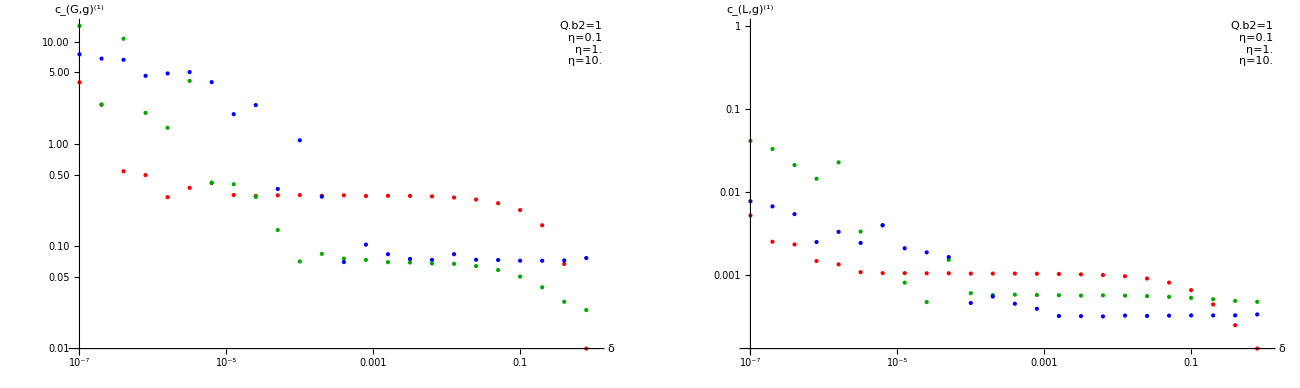

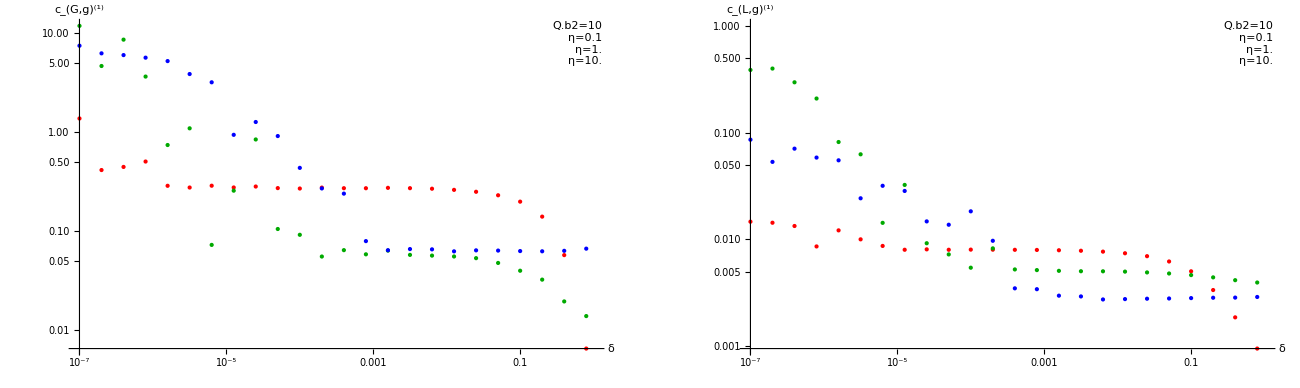

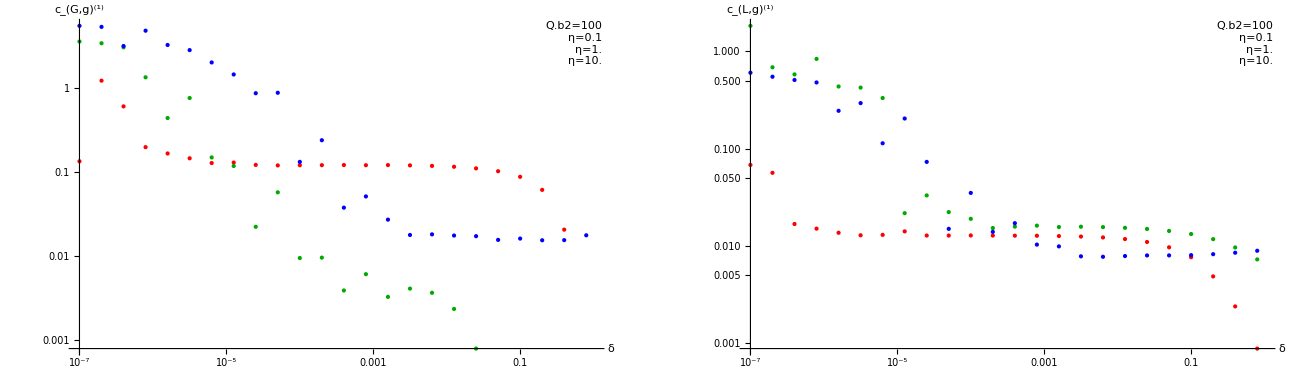

```mathematica
Module[{Q2s,ηs,m2V,δs,d,plt},
Q2s={1,10,100};
ηs=Table[10^k,{k,-1,1,1.}];
m2V=4.75^2;
δs=Table[10^k,{k,-7,0,.3}];
d=Get["~/Physik/PhD/MMa/data/c1g/deltaTest.m"];
plt[Q_]:=Module[{lG,lL,ins},
ins=Inset[Framed@Grid[{
{"Q.b2="<>ToString@Q},
{Text@Style["η="<>ToString@ηs[[1]],Red]},
{Text@Style["η="<>ToString@ηs[[2]],Darker@Green]},
{Text@Style["η="<>ToString@ηs[[3]],Blue]}
},Alignment->Left],Offset[{-2,-2},Scaled[{1,1}]],{Right,Top}];
lG=(η↦Table[{δ,({G,η,Q,δ}/.d)},{δ,δs}])/@ηs;
lL=(η↦Table[{δ,({L,η,Q,δ}/.d)},{δ,δs}])/@ηs;
Show[GraphicsRow[{
ListLogLogPlot[lG,PlotStyle-> {Red,Darker@Green,Blue},Epilog->ins,AxesLabel-> {"δ",Subsuperscript["c","G,g","(1)"]}],
ListLogLogPlot[lL,PlotStyle-> {Red,Darker@Green,Blue},Epilog->ins,AxesLabel-> {"δ",Subsuperscript["c","L,g","(1)"]}]
}],ImageSize-> 1300]
];

Print@plt[Q2s[[1]]];
Print@plt[Q2s[[2]]];
Print@plt[Q2s[[3]]];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00497882, 0.523606}. NIntegrate obtained -0.000201486 and 2.36877×10^-8 for the integral and error estimates.

2: {L,0.01,1} 27.0433

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00498508, 0.3903}. NIntegrate obtained -0.00152312 and 1.01407×10^-7 for the integral and error estimates.

1: {L,0.01,10} 55.52

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00486744, 0.594809}. NIntegrate obtained -1.76634 and 0.000125505 for the integral and error estimates.

7: {G,0.1,1} 67.15

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.810849 and 0.0000365432 for the integral and error estimates.

8: {G,0.01,1} 74.0833

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00488193, 0.568676}. NIntegrate obtained -0.00339639 and 2.59465×10^-7 for the integral and error estimates.

2: {L,0.1,1} 61.64

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00426376, 0.974152}. NIntegrate obtained -2.11255 and 0.000111578 for the integral and error estimates.

6: {G,1.,1} 105.53

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0153797, 0.0829785}. NIntegrate obtained -0.73761 and 0.0000815745 for the integral and error estimates.

8: {G,0.01,10} 50.5933

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0262209 and 1.10727×10^-6 for the integral and error estimates.

1: {L,0.1,10} 88.6967

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.57396 and 0.0000578727 for the integral and error estimates.

7: {G,0.1,10} 93.84

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0042674, 0.590396}. NIntegrate obtained -0.0785334 and 0.0000152262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00426119, 0.944985}. NIntegrate obtained -1.88646 and 0.000276385 for the integral and error estimates.

8: {L,1.,10} 41.5233

6: {G,1.,10} 62.01

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00425533, 0.799986}. NIntegrate obtained -0.00912673 and 5.60224×10^-7 for the integral and error estimates.

2: {L,1.,1} 101.593

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.203088 and 0.0000560272 for the integral and error estimates.

5: {G,10.,1} 231.587

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.267139 and 0.000108176 for the integral and error estimates.

3: {G,100.,10} 326.793

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00324968, 0.000961829}. NIntegrate obtained -0.203815 and 0.000121236 for the integral and error estimates.

5: {G,10.,10} 107.767

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.286691 and 0.000114768 for the integral and error estimates.

4: {G,100.,1} 356.89

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.0000918945 and 2.15×10^-7 for the integral and error estimates.

1: {L,10.,1} 413.613

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000570361 and 1.51863×10^-6 for the integral and error estimates.

7: {L,10.,10} 407.07

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00067906 and 5.08954×10^-7 for the integral and error estimates.

8: {L,100.,1} 495.027

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00597116 and 4.12896×10^-6 for the integral and error estimates.

6: {L,100.,10} 497.527

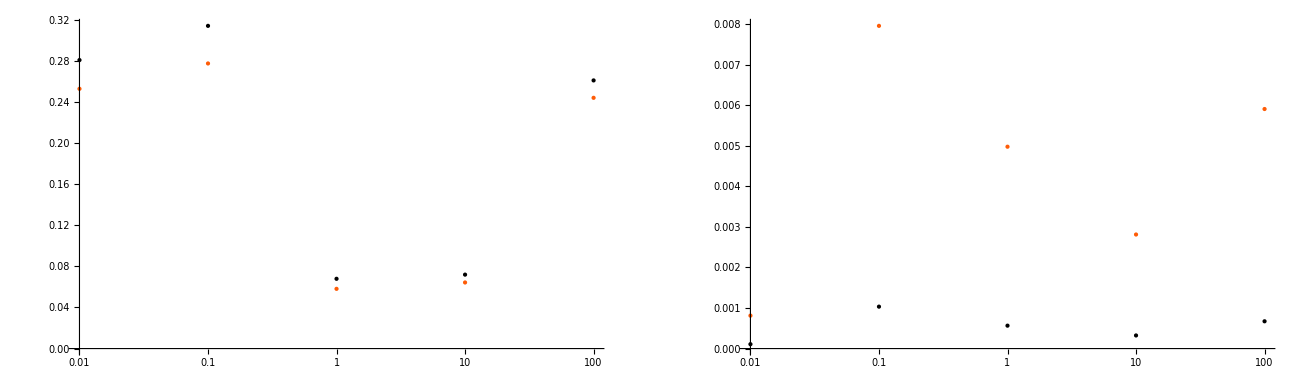

```mathematica
Module[{m2V,δ,Qs,ηs,ps,m,r,d,lLs,lGs,lTs,lPs},
m2V=4.75^2;
Qs=(*{1*^-2,1,10,100,1000}*){1,10};
ηs=Table[10^k,{k,-2,2,1.}];
ps=Tuples[{{G,L},ηs,Qs}];
m={};
SetSharedVariable[m];
(*ParallelDo[AppendTo[m,p-> c1g[p[[1]]][sOfη@p[[2]],p[[3]],m2V]],{p,ps}];*)
ParallelDo[
r=Timing[c1g[p[[1]]][sOfη@p[[2]],p[[3]],m2V]];
Print[$KernelID,": ",p," ",First@r];
AppendTo[m,p-> Last@r],{p,ps}];
d=Dispatch@m;
lGs=Table[{G,η,Q}/.d,{Q,Qs},{η,ηs}];
lLs=Table[{L,η,Q}/.d,{Q,Qs},{η,ηs}];
lTs=lGs+1/2lLs;
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,Full},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,Full},PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```